```mathematica
3^6
```

729

```mathematica
3^7
```

2187

```mathematica
3^8
```

6561

```mathematica
3^10
```

59049

```mathematica
3^3
```

27

```mathematica
3^5
```

243

```mathematica
5&5
```

5 (5&)

```mathematica
5^10
```

9765625

```mathematica
Module[
{deep=5000,cut=200,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo]
]
```

```mathematica
Blue
```

```mathematica
RGBColor[0.18, 0.27, 1]
```

```mathematica
Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]
```

{0→RGBColor[1., 1., 1.],1→RGBColor[0.8, 0.8, 1.],2→RGBColor[0.6, 0.6, 1.],3→RGBColor[0.3999999999999999, 0.3999999999999999, 1.],4→RGBColor[0.19999999999999996, 0.19999999999999996, 1.],5→RGBColor[0., 0., 1.],6→RGBColor[0., 0., 0.6666666666666666],7→RGBColor[0.2, 0.13333333333333333, 0.6666666666666666],8→RGBColor[0.4, 0.26666666666666666, 0.6666666666666666],9→RGBColor[0.6000000000000001, 0.4, 0.6666666666666666],10→RGBColor[0.8, 0.5333333333333333, 0.6666666666666666]}

```mathematica
RandomRuleMutation[{n_, k_, r_}, num_:1]:= Module[{digs = IntegerDigits[n, k, k^(2r+1)]},
{FromDigits[MapAt[RandomChoice[Delete[Range[0,k - 1], # + 1]]&,digs, List/@RandomInteger[{1, Length[digs] - 1}, num]], k], k, r}
]
```

```mathematica
ClearAll@RandomRuleMutation
RandomRuleMutation[{n_, k_, r_}, num_:1]:= Module[{digs = IntegerDigits[n, k, k^(2r+1)]},
{FromDigits[MapAt[RandomChoice[Delete[Range[0,k - 1], # + 1]]&,digs, List/@RandomInteger[{1, Length[digs] - 1}, num]], k], k, r}
]
```

```mathematica
RepeatedTiming[ReplacePart[Table[0, 10^5], Thread[RandomInteger[{1, 10^5 - 1}, 10000]->RandomInteger[{1, 10}, 10000]]]]
```

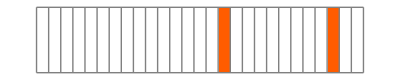

```mathematica
RuleSequencePlot[RandomRuleMutation[{0, 3, 1}, 2]]
```

```mathematica
{{"[◼]", "TestCALifeTime"}}
```

```mathematica
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#], 5],
life={{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru,{{1}, 0}, 200]],
If[life>=Last[#],{ru,life},#]
]&,{{0,10,2},0},1000];
```

```mathematica
Position[IntegerDigits[evo[[-1, 1, 1]], 10, 10^5]  - IntegerDigits[evo[[-2, 1,1]], 10, 10^5],Except[0]]
```

{{0},{15355},{24533},{25589},{47661},{94075},{}}

```mathematica
ArrayPlot[CellularAutomaton[evo[[-1, 1]], {{1},0}, 10], ColorRules->Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]]
```

-Graphics-

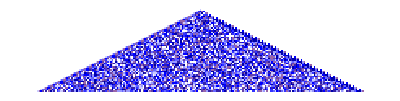
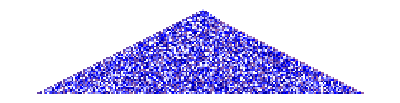
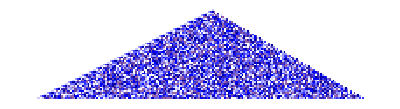
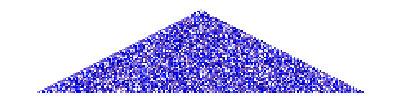
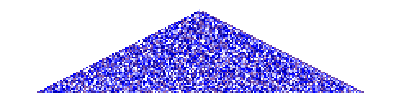
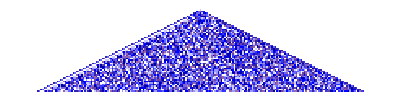
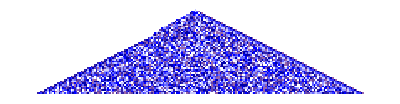
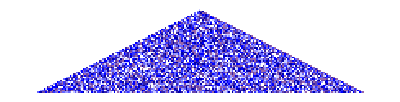

```mathematica
With[{colrules =Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]},  Table[ArrayPlot[CellularAutomaton[ResourceFunction["RandomCA"][{10, 2}, "Quiescent"->True], {{1}, 0}, 50], ColorRules->colrules], 10]]
```

```mathematica
10^5
```

100000

```mathematica
9^7
```

4782969

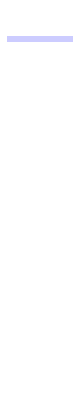
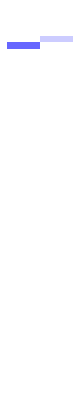
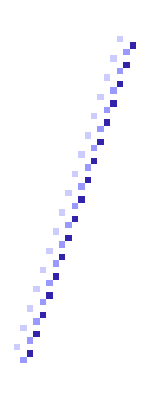
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{colrules =Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]},  Table[ArrayPlot[CellularAutomaton[RandomRuleMutation[{0, 10, 2}, 10000], {{1}, 0}, 50], ColorRules->colrules], 10]]
```

```mathematica
With[{colrules =Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]},  ParallelTable[SeedRandom[333222 +i];ArrayPlot[CellularAutomaton[RandomRuleMutation[{0, 10, 2}, 10000], {{1}, 0}, 5], ColorRules->colrules], {i, 100}]]
```

$Aborted

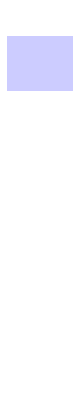
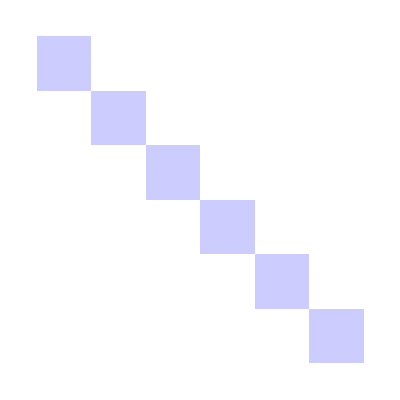
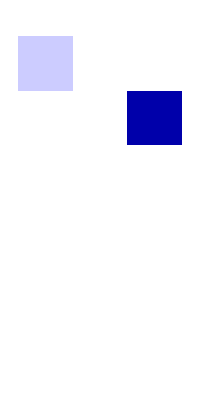
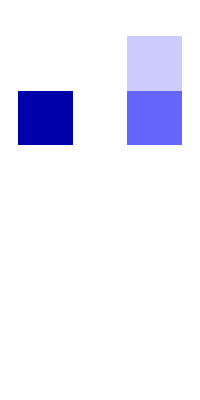
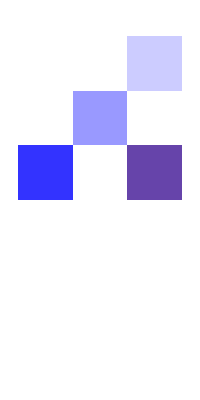
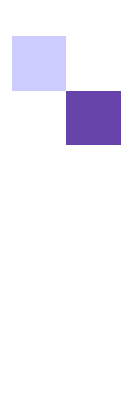
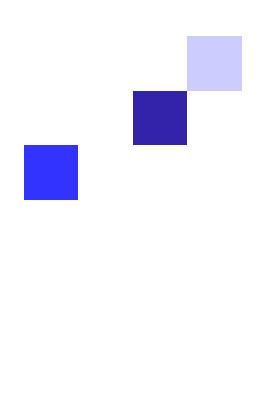
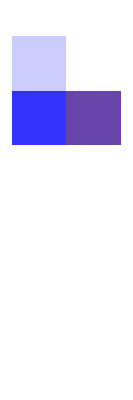
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{colrules =Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]},  ParallelTable[SeedRandom[333322 +i];ArrayPlot[CellularAutomaton[{FromDigits[ReplacePart[Table[0, 10^5], Thread[RandomInteger[{1, 10^5 - 1}, 10000]->RandomInteger[{1, 10}, 10000]]], 10], 10, 2}, {{1}, 0}, 5], ColorRules->colrules], {i, 100}]]
```

```mathematica
RepeatedTiming[CellularAutomaton[ResourceFunction["RandomCA"][{10, 2}, "Quiescent"->True], {{1}, 0}, {50, {-50, 50}}]]
```

{1.11004,{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,9,5,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,8,1,3,3,3,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,7,1,4,3,2,6,4,9,2,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,5,5,0,6,0,0,9,6,5,1,3,5,9,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,0,1,9,2,6,3,7,9,5,2,2,7,0,5,5,5,8,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,4,3,6,0,8,0,1,3,3,8,2,3,2,5,1,1,0,7,2,8,9,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,0,7,2,8,0,5,5,4,6,5,9,8,6,6,0,7,8,5,7,7,8,1,9,6,8,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,4,1,8,7,0,0,7,0,7,7,8,1,7,7,5,2,8,8,2,8,1,8,1,9,2,1,9,1,9,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,0,7,3,9,2,8,0,4,7,9,6,1,0,9,9,2,5,2,0,0,8,4,2,6,2,4,1,7,9,6,5,1,8,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,4,1,2,4,1,9,6,4,0,7,0,2,7,0,0,4,2,2,5,2,7,0,8,3,4,3,1,4,8,9,2,1,9,2,4,5,9,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,0,7,5,6,1,2,5,9,1,7,6,1,3,1,6,1,0,1,7,1,6,1,5,8,5,6,9,9,3,8,5,6,9,2,8,3,1,5,1,5,8,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,4,1,4,2,2,9,9,2,3,5,7,8,4,2,3,8,1,2,7,8,6,3,0,5,1,4,6,7,5,3,1,2,6,4,6,1,7,0,3,7,4,4,1,8,9,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,0,7,3,9,6,8,3,9,4,0,8,8,7,5,1,9,6,6,6,9,2,4,7,2,2,6,6,0,1,0,6,3,4,8,4,3,0,0,3,6,4,8,4,7,4,9,9,6,8,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,4,1,2,4,7,4,2,8,5,2,4,6,0,1,8,0,3,4,9,8,3,6,0,3,2,5,0,8,1,7,7,8,0,7,7,8,4,0,7,8,4,9,7,7,2,7,2,0,4,0,9,1,9,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,0,7,5,6,6,3,5,5,1,7,5,9,9,9,0,6,7,9,6,3,9,0,0,7,9,5,2,8,9,4,4,9,2,5,5,6,9,1,6,5,6,9,4,2,0,3,7,4,8,0,9,4,5,3,5,1,8,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,4,1,4,2,9,6,5,9,9,2,8,4,3,0,7,6,8,6,3,7,7,7,1,0,7,1,5,9,5,6,4,0,2,3,5,1,0,0,6,2,0,1,9,7,0,3,6,2,6,8,9,1,6,2,9,8,7,3,4,5,9,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,0,7,3,9,9,3,8,9,6,8,7,4,1,4,7,7,0,8,2,2,3,3,0,8,9,9,9,8,5,5,5,9,5,0,3,3,6,8,1,5,1,2,6,4,2,3,5,4,3,0,7,2,8,6,8,4,6,4,4,1,1,6,1,5,8,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,1,4,1,2,4,0,0,6,2,4,8,9,0,5,4,0,0,5,7,6,4,4,3,2,5,7,2,1,6,8,1,5,1,9,2,0,2,6,3,9,5,6,9,0,5,3,7,7,5,4,1,4,4,0,1,9,1,9,9,9,5,6,8,7,9,5,7,1,8,9,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,8,1,0,7,5,6,1,1,7,6,6,6,4,5,5,6,8,0,2,0,0,3,3,2,8,4,5,4,7,8,4,4,7,6,6,0,9,8,8,5,2,1,6,9,9,5,8,6,5,8,1,1,7,5,0,8,7,6,6,6,7,5,4,7,5,0,3,3,0,0,7,9,9,6,8,2,3,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,8,1,4,1,4,2,2,2,7,4,5,3,7,6,1,2,1,5,7,2,8,6,2,5,3,5,5,4,6,2,8,5,8,5,5,5,4,1,5,7,9,2,8,2,0,1,7,5,0,9,2,6,1,0,5,7,7,4,1,3,9,8,5,0,0,5,9,6,2,7,1,1,7,0,7,0,9,1,9,2,3,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,8,1,0,7,3,9,6,7,2,7,6,4,5,0,4,7,3,7,4,2,4,2,1,5,8,9,7,7,6,1,8,3,2,6,4,4,7,1,2,6,2,3,9,4,3,8,1,8,2,0,4,8,0,2,6,5,1,2,0,8,5,8,2,8,7,2,4,0,8,9,5,1,0,0,0,2,6,7,4,3,5,1,8,2,3,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,8,1,4,1,2,4,7,9,2,8,9,3,7,4,4,6,6,6,5,6,1,0,9,3,5,5,9,4,4,7,9,7,3,6,2,8,3,6,9,9,5,0,3,0,1,8,6,4,5,5,7,4,1,0,1,8,5,1,4,2,7,8,1,4,7,7,1,1,4,3,7,2,0,3,3,4,9,9,4,7,3,4,5,3,4,5,9,2,3,0,0,0,0,0,0},{0,0,0,0,8,1,0,7,5,6,6,2,6,2,6,6,4,0,0,8,6,9,0,0,5,1,3,7,5,2,5,9,7,7,7,1,0,1,0,1,4,9,6,8,5,7,7,3,3,7,7,8,4,2,2,3,8,3,9,2,6,2,2,0,7,3,7,7,0,4,4,0,9,1,5,7,9,0,4,5,8,8,4,1,7,3,4,8,9,4,0,6,1,5,8,2,3,0,0,0,0},{0,0,8,1,4,1,4,2,9,7,9,3,9,3,3,7,4,7,2,4,9,5,0,6,4,9,7,6,4,8,0,7,6,5,8,3,0,4,1,5,6,4,6,6,3,7,3,2,4,8,8,7,8,1,5,3,3,7,5,8,4,2,0,4,3,0,5,1,8,7,2,5,0,9,0,7,4,0,8,2,1,1,1,6,0,7,8,9,2,5,2,9,9,7,1,8,9,2,3,0,0},{8,1,0,7,3,9,9,5,6,2,7,4,7,1,6,1,7,2,4,5,9,2,2,4,2,9,8,4,1,9,3,6,4,9,6,5,8,7,5,3,3,0,9,7,1,2,1,2,0,9,4,1,4,6,4,0,1,8,8,0,4,6,8,7,7,3,9,2,0,7,5,7,1,8,0,1,2,4,3,8,9,4,6,2,0,6,2,2,4,8,8,9,3,6,6,9,9,6,8,2,3},{4,1,2,4,0,0,9,1,2,0,0,7,1,3,4,4,7,8,6,5,0,3,9,6,7,7,2,8,2,2,9,7,5,8,9,5,3,1,1,2,6,2,3,0,6,2,3,8,7,3,8,9,2,2,0,6,1,2,5,5,8,7,5,6,4,9,7,3,8,6,9,3,8,7,6,8,7,0,5,3,8,5,0,5,0,1,1,7,4,2,4,3,2,2,3,6,1,0,9,1,9},{5,6,1,1,5,4,4,8,4,8,2,3,6,1,9,4,1,6,2,6,8,8,0,9,4,5,7,4,9,7,4,4,9,3,2,0,4,3,8,1,0,6,2,9,2,2,8,7,4,9,8,5,7,0,1,1,2,0,0,7,8,2,0,7,8,7,6,6,6,0,4,7,3,4,8,8,2,2,9,4,3,0,1,1,4,3,2,7,6,7,4,6,1,1,6,6,5,8,4,3,5},{2,2,9,2,0,0,8,3,3,2,5,9,2,2,9,3,6,8,6,2,2,1,7,6,5,3,2,5,3,4,0,7,8,2,3,0,7,1,3,9,5,5,1,1,5,0,4,9,9,9,9,8,6,3,9,3,7,8,2,0,6,7,0,4,8,4,3,5,7,4,4,0,6,6,5,2,3,8,5,4,2,8,2,4,6,9,3,0,6,9,8,3,8,4,8,3,9,5,9,6,5},{3,2,3,8,3,2,0,8,1,4,5,9,3,9,9,2,9,9,0,8,0,8,4,5,8,2,2,4,7,7,1,3,8,3,4,7,3,2,4,3,0,3,5,8,9,7,3,9,9,1,5,5,2,4,9,8,4,7,5,6,4,4,9,6,9,8,8,6,0,8,7,2,4,7,6,8,1,5,5,8,2,1,0,4,5,4,3,3,9,0,3,6,6,4,4,2,1,2,9,9,7},{6,7,6,1,1,1,1,9,5,5,1,3,1,4,2,0,5,2,5,7,0,4,1,8,8,4,6,3,7,0,4,0,0,0,1,4,2,3,0,3,0,1,7,2,7,4,6,4,0,3,9,9,9,2,5,5,4,1,9,4,6,1,8,6,2,3,1,1,4,8,9,6,2,9,3,7,5,1,7,7,2,6,8,0,8,5,3,8,3,8,3,3,5,8,9,6,2,1,4,5,8},{6,7,1,3,1,2,3,5,1,6,9,5,9,5,3,3,4,7,5,1,7,3,8,2,2,2,7,5,9,4,6,7,9,9,4,7,9,1,5,1,6,2,8,6,3,9,8,9,8,2,6,9,1,6,3,9,2,4,7,3,1,6,4,6,2,0,4,6,8,7,8,4,0,0,6,1,4,7,8,4,3,9,3,3,6,4,6,8,2,9,0,8,7,9,5,8,3,4,4,0,8},{9,9,0,1,7,9,0,1,9,0,2,2,8,9,4,0,1,1,5,6,5,0,4,5,0,9,9,0,6,9,2,2,0,6,0,9,3,2,6,9,9,1,3,2,6,3,4,4,3,6,8,0,8,4,7,6,4,3,2,7,7,7,7,8,3,6,7,7,7,2,2,8,7,7,4,4,5,6,3,5,9,7,3,0,2,2,4,2,8,6,1,6,1,7,3,6,0,3,8,4,1},{7,7,3,4,8,6,8,1,6,5,2,7,0,1,0,1,0,2,9,1,2,1,9,3,5,3,5,0,0,1,5,0,8,4,5,2,1,2,2,0,7,0,6,3,8,2,5,2,9,7,7,7,2,8,5,1,4,2,4,1,4,2,4,2,2,6,6,3,3,9,7,2,6,6,6,5,2,6,8,6,0,8,3,1,9,6,1,9,0,3,9,3,6,1,7,9,8,3,4,2,1},{6,1,4,5,7,9,0,5,8,0,2,6,7,6,9,2,5,0,9,0,2,4,4,6,2,7,4,4,5,0,2,4,4,7,4,9,5,0,8,4,4,9,5,4,8,2,4,3,7,9,3,7,0,9,8,0,0,1,3,3,0,8,8,4,8,7,5,9,1,6,8,3,5,8,0,9,7,2,3,8,0,4,9,8,3,3,2,8,7,5,0,4,0,4,9,5,6,5,2,3,5},{3,7,7,7,6,8,7,0,2,7,1,0,8,4,0,2,7,1,5,7,8,7,9,3,3,3,0,6,6,1,3,0,1,6,2,9,8,6,4,3,2,2,8,5,0,6,6,3,3,0,5,4,3,0,7,8,9,2,0,7,1,6,1,4,8,8,5,7,4,3,6,3,9,0,6,0,0,8,0,2,7,6,5,1,9,6,0,9,7,5,9,6,9,3,6,0,8,1,7,3,8},{3,2,6,0,3,8,9,0,2,4,0,3,1,4,6,3,7,7,9,4,7,1,8,7,8,6,4,6,4,1,3,0,3,9,4,4,7,4,0,6,5,1,0,7,5,3,4,2,2,1,2,9,4,2,8,2,3,4,2,4,3,1,4,2,7,7,0,1,5,4,5,7,3,2,0,3,2,3,9,0,7,6,0,2,9,9,3,5,3,7,4,4,0,6,6,3,3,4,1,0,7},{5,2,4,9,2,1,2,5,8,1,2,6,6,2,1,9,1,9,1,2,2,7,3,2,3,4,5,8,2,7,8,7,2,7,1,7,2,1,2,6,6,6,2,6,6,1,3,6,0,2,4,1,3,8,2,9,5,6,1,1,8,2,6,0,8,0,7,5,9,2,3,4,6,9,7,1,0,6,4,0,0,6,4,5,8,9,1,6,2,9,5,7,2,8,4,5,6,8,5,2,3},{3,5,7,9,6,1,9,2,0,7,7,0,7,6,1,9,2,2,1,6,4,4,5,3,5,2,5,8,3,1,6,2,1,9,3,7,4,8,4,7,3,8,0,5,9,0,1,4,0,2,8,8,3,4,4,8,3,7,1,9,3,6,3,4,2,8,8,1,6,9,1,4,0,3,2,3,8,4,5,3,1,4,7,2,5,6,6,8,9,1,6,9,3,1,9,8,0,7,6,7,7},{0,3,2,9,6,0,2,0,3,6,9,6,5,6,3,8,7,2,7,1,4,6,3,2,0,1,3,1,2,2,3,5,1,1,1,4,7,7,6,4,9,4,5,1,6,1,3,0,7,2,9,1,6,0,0,4,1,7,1,8,4,8,2,0,9,5,5,9,8,8,1,8,8,1,7,5,8,4,4,3,0,5,4,8,6,6,9,8,8,4,2,3,2,3,1,1,8,8,2,4,3},{9,8,1,4,7,3,1,3,7,2,8,7,0,2,8,6,8,1,4,9,6,1,6,6,4,8,3,3,5,4,2,2,8,3,2,3,4,0,4,7,6,0,6,0,3,4,2,5,4,9,1,4,5,8,0,8,0,5,7,1,7,0,4,5,5,3,5,0,7,8,3,1,6,0,9,9,0,1,6,0,3,2,9,1,8,8,4,9,1,3,2,2,8,6,6,1,1,8,9,6,3},{4,4,0,8,6,8,6,6,0,1,7,6,0,2,8,7,9,5,8,8,5,6,7,4,1,0,1,1,2,4,7,7,9,9,9,8,3,1,2,0,0,2,7,1,2,5,0,8,1,1,5,4,2,4,8,1,7,9,7,6,5,5,1,0,4,1,9,7,0,0,8,8,7,3,1,1,9,4,2,9,5,2,0,1,9,6,4,3,4,2,4,6,8,5,9,7,3,5,1,2,6},{7,1,7,1,3,3,7,9,1,4,2,4,7,7,2,2,7,0,4,4,3,3,9,8,9,0,0,6,3,5,0,7,5,3,3,1,6,8,3,9,1,6,6,9,9,3,9,1,9,5,5,4,3,4,2,2,9,2,0,8,2,2,7,4,5,6,9,8,9,8,5,1,4,9,5,3,3,5,8,3,8,4,4,1,5,2,5,0,0,0,8,3,7,5,1,8,6,8,1,8,5},{4,4,7,4,6,1,8,2,6,6,4,2,6,2,0,3,9,7,3,2,4,0,1,3,8,2,1,4,0,1,4,4,7,0,2,4,8,0,0,5,7,2,5,3,1,7,8,1,9,0,3,4,5,2,1,5,3,6,5,7,9,6,6,1,6,7,6,2,1,7,2,5,2,4,4,3,5,4,7,7,1,0,7,6,6,9,9,1,8,6,5,6,3,1,4,1,0,1,6,9,3},{5,2,9,9,8,4,4,0,9,7,1,5,0,4,8,6,6,4,5,0,7,3,4,2,9,0,5,1,3,3,5,6,5,6,7,6,0,3,4,7,6,4,7,1,4,5,8,9,6,2,6,5,5,3,0,5,8,1,9,2,3,5,0,6,0,4,8,0,6,4,0,6,7,6,0,2,7,9,6,9,9,8,2,7,5,2,6,2,7,2,1,0,0,7,2,5,1,5,2,1,2},{4,3,5,6,1,4,5,1,9,7,6,5,3,3,9,3,7,7,8,7,0,3,9,7,8,9,6,9,5,3,3,0,9,2,7,9,0,0,5,2,7,7,5,4,6,8,2,5,0,1,6,1,2,3,4,3,2,8,0,7,8,9,0,2,8,3,6,0,6,9,6,0,2,8,2,7,3,0,1,0,7,3,7,2,8,4,0,4,9,5,2,6,8,7,2,9,5,2,4,5,6},{0,9,3,2,7,2,2,9,0,9,7,6,7,4,6,3,2,4,0,5,2,6,5,0,7,5,0,7,2,4,6,3,9,3,6,9,3,6,2,3,5,4,8,6,4,9,4,4,7,8,8,7,6,9,2,7,8,5,5,4,4,0,2,6,2,6,9,8,0,7,4,6,3,8,4,5,6,4,0,1,1,6,8,0,0,9,9,3,0,2,2,0,7,0,6,9,1,7,3,2,5},{4,5,9,8,9,4,2,6,3,8,1,3,9,2,1,2,5,9,3,7,5,0,8,4,5,1,5,3,2,8,8,3,2,0,5,4,5,2,9,0,2,3,1,8,4,3,2,3,8,2,1,8,5,9,0,2,0,2,8,6,1,3,1,0,9,6,0,1,1,8,1,3,2,4,9,1,8,7,7,1,2,4,4,1,6,1,5,7,2,6,3,4,4,2,0,6,8,8,1,3,2},{0,7,1,6,6,2,8,6,8,7,4,8,2,6,1,5,5,5,2,9,1,0,4,3,4,0,3,4,1,4,6,8,1,0,0,4,1,0,7,7,4,3,3,6,3,4,2,0,9,7,5,8,9,7,7,4,5,2,5,5,1,2,7,4,7,1,5,2,2,6,9,8,2,4,5,6,9,9,2,1,2,6,8,6,3,7,6,5,2,2,2,8,7,1,6,0,6,2,9,4,4},{0,7,0,4,9,3,8,4,9,5,6,4,7,1,1,5,9,9,6,8,1,7,6,3,2,6,5,7,2,3,1,9,0,1,8,3,1,7,1,3,2,0,8,9,2,9,4,2,5,8,9,6,4,2,2,3,7,6,1,9,3,7,9,7,4,8,5,5,6,9,9,7,0,1,6,8,6,2,9,9,3,0,2,2,9,2,6,3,7,9,0,4,2,3,4,4,5,3,0,8,0},{6,4,6,9,1,1,5,0,5,0,9,2,4,5,0,8,9,2,9,8,7,5,5,1,3,6,0,4,8,1,8,3,7,0,1,6,9,5,2,8,8,3,8,3,0,1,6,1,9,3,1,6,7,2,9,2,4,1,1,1,9,3,6,1,9,6,3,1,5,1,0,9,8,0,8,2,0,7,5,2,7,2,7,8,8,2,1,3,9,0,9,6,0,7,4,1,7,0,1,1,0}}}

```mathematica
RepeatedTiming[CellularAutomaton[ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True], {{1}, 0}, {50, {-50, 50}}]]
```

{0.00268218,{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,0,0,1,1,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,1,1,1,0,0,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,1,0,1,0,1,0,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,0,0,1,1,1,0,0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,1,1,1,1,1,0,1,1,1,0,1,1,1,1,0,0,0,1,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,1,1,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1,0,1,0,1,1,0,1,1,1,0,1,0,1,1,1,0,0,0,1,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,0,0,1,1,1,0,1,0,1,1,0,0,1,0,1,1,0,0,1,0,1,1,1,0,1,0,1,1,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,1,1,1,1,1,0,1,1,0,1,0,1,1,1,0,1,0,1,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,1,1,0,0,0,0,1,0,0,1,1,1,1,0,0,1,0,1,1,0,0,1,0,1,1,1,0,1,1,1,1,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,1,0,1,0,1,1,1,0,1,0,1,1,1,0,0,1,0,0,0,0,1,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,0,0,1,1,1,0,1,0,1,0,1,1,1,1,0,1,0,0,1,0,1,1,0,0,1,0,1,1,0,1,0,1,1,1,0,1,1,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,0,1,1,1,1,1,0,1,1,0,1,0,0,0,1,0,1,1,0,1,1,0,1,0,1,1,1,0,1,1,1,1,0,0,1,0,0,1,0,1,1,1,1,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,1,1,0,0,0,0,1,0,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,0,1,0,0,0,0,1,0,1,1,0,0,1,1,0,0,0,1,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,1,0,0,0,0,0,1,0,0,1,1,0,0,0,1,0,1,1,0,1,0,1,1,1,0,1,0,1,0,0,0,1,1,1,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,1,1,1,1,0,0,0,1,1,1,0,1,0,1,0,1,1,1,0,1,0,0,1,1,0,0,0,0,0,1,1,1,1,0,1,1,1,1,0,0,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,1,0,0,0,1,0,1,1,1,1,1,0,1,1,0,1,0,0,1,0,1,1,0,0,0,0,1,0,0,1,1,1,0,1,0,0,0,0,1,0,1,1,1,0,1,1,0,0,0,0,0,1,0,0,0,0,1,0,1,1,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,1,1,1,1,1,1,1,0,0,0,0,1,0,0,1,1,1,1,0,1,1,0,1,0,1,0,1,1,0,0,0,1,1,0,1,1,1,0,1,1,1,0,0,1,0,0,1,0,1,0,0,1,1,0,1,0,1,1,1,0,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,1,0,1,0,0,1,1,1,1,0,1,0,1,0,1,1,1,0,1,0,0,1,0,0,0,1,0,1,1,0,0,1,1,0,1,0,0,0,1,1,1,0,0,1,0,0,1,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,0,0,1,1,1,0,1,0,1,0,1,1,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,1,1,1,0,1,0,1,0,0,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,1,1,1,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,1,1,1,0,1,1,0,1,0,0,0,1,0,1,1,0,1,1,0,1,0,1,1,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,1,1,0,1,0,0,1,0,0,0,0,0,1,0,0,1,0,1,0,0,1,1,1,1,0,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,1,0,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,0,1,1,0,0,0,1,0,1,1,1,1,0,1,1,1,1,0,1,0,1,0,0,1,1,0,0,1,1,0,1,0,0,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,1,0,0,0,1,0,0,0,0,0,1,0,0,1,1,0,0,0,1,0,1,1,1,0,0,0,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,1,1,0,1,0,0,0,0,1,0,0,1,1,1,0,1,1,0,1,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,0,1,0,1,1,1,0,1,0,0,1,1,0,0,0,0,0,1,1,1,1,0,0,1,0,1,0,0,1,1,1,0,1,0,1,1,1,0,1,0,1,1,1,0,1,1,1,1,1,0,1,1,0,0,0,1,1,0,0,1,1,1,1,0,1,1,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,0,0,1,0,1,1,0,0,0,0,1,0,0,1,1,1,0,1,0,1,1,1,0,1,0,0,1,1,0,1,1,0,0,1,0,1,1,0,0,1,0,0,0,0,0,1,0,0,1,0,1,1,1,0,0,1,0,1,0,1,0,0,1,0,1,1,1,1,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,1,1,0,1,1,0,1,0,1,0,1,1,0,0,0,1,1,0,1,1,0,0,1,0,1,1,0,0,0,1,0,1,0,1,1,1,0,1,0,1,1,0,1,0,0,1,1,0,0,1,1,0,0,1,0,1,1,1,0,1,0,1,0,1,1,0,0,0,1,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,1,1,1,1,0,1,0,1,0,1,1,1,0,1,0,1,0,1,1,1,0,1,0,1,1,1,1,0,1,0,0,1,0,1,1,0,1,1,1,1,0,0,0,0,1,0,0,0,1,1,1,0,0,1,0,1,1,0,1,0,1,0,1,1,1,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,0,1,0,1,1,0,1,1,0,1,1,0,0,0,1,0,1,0,1,1,0,1,1,1,1,1,0,1,1,1,0,1,1,1,1,0,1,0,0,1,0,1,1,1,1,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,1,1,0,1,0,1,1,1,1,0,1,1,0,1,1,1,1,0,1,1,0,1,0,1,1,1,1,0,1,1,0,1,1,0,1,0,1,1,1,1,0,1,0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,1,0,1,1,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,1,1,1,1,0,0,0,1,0,0,1,1,0,1,1,1,1,0,0,0,1,0,1,1,0,1,0,1,0,1,1,0,1,1,1,0,1,0,1,1,1,0,1,1,0,1,0,1,1,1,1,0,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,1,0,0,0,1,0,1,1,1,0,0,0,0,0,1,1,1,0,0,0,1,0,1,0,1,1,1,0,0,0,0,1,0,0,0,1,0,1,1,1,1,0,1,1,1,1,0,1,0,1,1,0,0,1,0,1,1,0,0,1,0,0,1,1,1,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,1,1,1,0,0,1,0,1,0,0,1,1,1,1,0,1,1,1,1,0,1,0,0,1,0,1,0,1,1,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,1,1,0,1,0,1,1,1,0,1,0,1,1,0,0,0,1,0,1,0,1,1,1,0,0,0,0,0,1,1,1,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,1,1,0,1,0,1,1,1,0,1,0,0,1,0,1,0,0,0,0,1,0,1,1,0,1,1,0,1,0,1,1,0,0,0,1,0,1,1,1,0,1,0,1,1,1,0,1,1,1,1,0,0,1,0,1,1,0,1,0,1,1,1,1,0,1,0,0,1,0,1,0,0,1,1,1,1,0,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,1,0,1,1,0,0,1,0,1,1,0,1,1,0,1,1,0,1,1,1,0,1,1,0,1,1,1,1,0,1,0,1,1,1,1,0,0,1,0,1,1,0,0,1,0,0,0,0,1,0,1,1,1,0,1,1,1,1,0,0,0,1,0,1,1,0,1,1,0,1,0,0,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,0,1,0,1,1,1,0,1,1,0,1,1,0,1,1,0,0,1,0,0,1,1,0,0,0,1,0,1,1,0,0,0,1,0,1,1,1,0,1,0,1,1,0,1,0,1,1,1,0,0,1,0,0,0,0,1,0,1,1,1,1,0,1,1,0,1,1,1,1,0,1,1,0,1,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,1,0,0,1,0,0,1,1,0,1,1,0,1,0,1,1,0,0,0,0,0,1,1,1,1,0,1,0,1,1,1,1,0,0,1,0,1,1,0,1,1,1,1,0,0,1,0,1,1,0,1,0,1,1,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,1,1,1,1,0,1,1,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0},{0,1,1,0,1,1,1,1,0,1,0,0,0,0,1,0,1,1,1,1,0,1,0,1,0,0,1,1,1,0,1,0,1,1,0,0,0,1,0,1,1,1,0,1,1,0,0,0,1,0,1,1,1,0,1,1,1,1,0,0,1,0,1,1,1,0,0,0,0,0,1,1,1,0,0,0,1,0,1,0,0,1,0,1,1,1,1,0,1,1,0,1,0,1,0,0,0,0,0,0,0},{0,1,1,0,0,0,1,0,1,1,1,0,1,1,1,0,0,0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,1,0,1,1,1,1,0,0,1,0,0,1,0,1,1,1,1,0,0,1,0,0,0,0,1,0,1,1,1,0,0,1,0,1,0,0,1,1,1,1,0,1,1,1,1,0,1,0,1,1,0,0,0,1,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,1,0,0,0,1,0,1,1,1,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,0,0,1,1,0,0,0,1,0,1,1,0,1,0,1,1,1,0,0,1,0,1,1,1,0,1,0,0,1,0,1,0,0,0,0,1,0,1,1,0,1,0,1,1,1,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,0},{0,1,1,1,0,1,0,1,1,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,1,0,1,1,1,1,0,0,1,0,1,1,1,0,0,1,0,1,1,0,1,1,0,1,1,0,1,1,1,0,1,1,1,1,0,0,1,0,1,1,1,1,0,1,0,1,1,0,1,1,0,0,0,0},{0,1,1,0,1,1,0,1,1,0,0,0,1,0,1,1,1,0,1,0,1,1,1,0,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,0,1,1,1,1,1,0,1,0,0,0,0,1,0,1,1,1,0,0,1,0,1,1,1,0,1,1,0,1,1,0,1,1,0,0,1,0,0,0,0,1,0,1,1,1,0,0,0,1,0,1,1,0,1,1,0,1,0,1,0,0,0},{0,0,1,0,1,1,0,1,0,1,1,1,1,0,0,1,0,1,1,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,1,1,0,0,0,0,1,0,1,1,1,0,1,1,1,0,0,1,0,1,1,1,0,0,1,0,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,1,0,0,1,0,1,1,1,1,0,1,1,0,1,1,1,1,0,1,1,0,0},{1,1,1,0,1,1,1,1,0,0,0,1,0,1,1,1,0,1,0,1,1,1,0,0,0,1,0,1,1,1,1,0,0,0,1,0,0,1,0,1,0,1,1,1,0,0,1,0,0,0,1,0,1,1,1,0,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,0,1,1,1,1,0,0,1,0,1,1,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,1,0,1,0},{0,1,0,0,0,0,1,0,1,1,1,1,0,0,1,0,1,1,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,1,1,1,0,0,1,0,1,1,1,0,1,0,1,0,1,1,1,0,0,0,1,0,0,0,0,1,0,1,1,1,0,0,1,0,1,1,1,0,0,0,0,0,1,1,1,0,0,1,1,0,1,1}}}

### V2

```mathematica
ClearAll@RandomRuleMutation
RandomRuleMutation[{n_, k_, r_}, num_:1]:= Module[{digs = IntegerDigits[n, k, k^(2r+1)]},
{FromDigits[ReplacePart[digs,Thread[RandomInteger[{1, Length[digs]-1},num]->RandomInteger[{0, k - 1},num]]], k], k, r}
]
```

```mathematica
ClearAll@RandomRuleMutation
RandomRuleMutation[{n_, k_, r_}, num_:1]:= Module[{digs = IntegerDigits[n, k, k^(2r+1)]},
digs[[RandomInteger[{1, Length[digs]-1},num]]] = RandomInteger[{0, k - 1},num];
{FromDigits[digs, 10], k, r}
]
```

```mathematica
evos=
ParallelTable[SeedRandom[111111+i];
Nest[CompoundExpression[
ru=RandomRuleMutation[First[#], 1000],
life={{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru,{{1}, 0}, 20]],
If[life>=Last[#],{ru,life},#]
]&,{{FromDigits[ReplacePart[Table[0, 10^5], Thread[RandomInteger[{1, 10^5 - 1}, 10000]->RandomInteger[{1, 10}, 10000]]], 10], 10, 2},0},100], {i, 1}];
```

```mathematica
evos=
ParallelTable[SeedRandom[111111+i];
NestList[CompoundExpression[
ru=RandomRuleMutation[First[#], 1000],
life={{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru,{{1}, 0}, 20]],
If[life>=Last[#],{ru,life},#]
]&,{{FromDigits[ReplacePart[Table[0, 10^5], Thread[RandomInteger[{1, 10^5 - 1}, 10000]->RandomInteger[{1, 10}, 10000]]], 10], 10, 2},0},600], {i, 100}];
```

$Aborted

```mathematica
rus = Table[SeedRandom[222222+i];{FromDigits[ReplacePart[Table[0, 10^5], Thread[RandomInteger[{1, 10^5 - 1}, 10000]->RandomInteger[{0, 9}, 10000]]], 10], 10, 2}, {i, 100}];
```

```mathematica
prus = Select[
rus, {{"[◼]", "TestCALifeTime"}}[CellularAutomaton[#, {{1}, 0}, 5]]>1&];
Length[prus]
```

24

```mathematica
RepeatedTiming[RandomInteger[{1, 10^5 - 1}, 10000]]
```

{0.0000905361,{20412,61785,83397,67431,20466,96741,79542,69039,21382,71594,58121,29025,21280,41474,96244,53484,98356,98389,69346,32518,61426,58890,41165,50270,12465,69949,60007,27175,48913,35662,79577,33447,22197,71608,50835,15855,87370,45026,962,68432,92316,92839,28376,97159,63039,15822,85014,74955,82118,60500,51684,28763,43097,49690,22224,29541,28404,90822,52584,92441,6745,67855,98406,79634,22653,16563,17909,25072,21517,57787,60614,77083,42481,89450,56983,36019,88321,28294,15777,4494,28358,5338,29868,88317,99657,60245,13870,64974,36270,35860,92315,76507,25494,56863,60947,64878,76134,73752,63650,5533,47226,43132,32521,37659,64980,18145,56940,13991,38199,65237,18396,90310,60398,21428,16237,75343,39798,24831,27825,8323,42905,77014,61833,10494,97818,53218,30907,25822,13593,9789,81453,87137,49260,53897,90599,66929,56724,15293,53804,9978,30337,18447,95181,12802,18941,62283,73647,26801,13562,67451,250,35359,55936,58294,12546,25251,39834,58786,19059,76412,58748,65973,18469,37849,7757,92913,6242,96442,70838,3482,9386,54810,82121,57036,73143,94928,79248,52516,96929,89068,59351,11485,27999,23331,5056,55152,46110,89116,3875,64140,3586,92724,67311,20577,81584,7860,68901,62612,75076,43965,5809,39033,6670,47731,24094,38926,43007,8813,3817,93312,34462,21895,60446,49036,36197,62982,52977,18909,75728,9443,2572,79600,57151,33251,31084,68318,74339,93803,51590,89770,22514,79562,34216,1333,40238,46024,43496,58587,68692,30329,89039,28027,99700,6865,61154,73091,81410,58493,10387,24056,25958,51432,43952,41908,31100,81493,18570,68327,35399,69413,25098,80344,76435,74190,95108,20446,84381,6701,80831,90409,63006,94849,45488,4257,30561,64095,90852,93176,78008,95261,23379,92974,55791,72895,60445,75279,94825,74793,92277,35099,34852,11943,33105,10418,33010,54625,38859,17490,96800,67733,6262,14634,11015,95338,69522,9945,67716,30770,27346,59218,68564,67009,90123,70294,61098,70510,99971,7083,52360,77541,98834,12088,13814,74639,363,51231,65503,31143,28884,15279,17349,45434,52895,91952,73943,17759,40337,35412,41053,72809,6004,42524,55423,44790,58198,2116,10772,58740,24468,94464,12584,97215,50643,53512,6965,83312,11260,2157,87646,17555,12886,50954,10657,27792,38727,9903,98293,54787,5505,38905,25937,14566,95303,98343,20196,77710,57129,26760,49295,17448,58180,31366,29642,68625,52311,89943,11144,96600,71837,6615,6986,47177,62568,24830,17812,55851,90997,71300,56470,50573,34822,30736,91656,35032,31387,20965,15220,64084,65765,1204,73816,64280,95209,82428,4814,90256,82545,22290,18672,69929,54376,55982,50276,60190,6781,31671,94351,13900,75654,56072,34816,19057,81989,85048,6707,8567,79596,61673,69154,75861,81647,70841,14882,70571,34233,38975,5596,78486,99556,52006,97273,21239,19219,20996,53251,3859,11144,17313,44396,96425,88560,88,74239,27723,78120,74776,73150,75281,12080,75076,12179,21093,61308,35229,943,82409,25228,90455,96260,56026,68745,26496,68884,23041,11570,72015,16933,57484,61109,20730,92646,50572,63269,37909,84004,29335,69886,68334,88537,94687,47029,90531,4227,68935,85238,27694,2147,42123,8192,3895,95164,20369,65932,98441,55053,29081,8310,7730,39344,17714,31206,48528,7844,36381,34822,192,10800,15389,47259,39789,4492,86610,18296,65934,57058,53912,28808,76090,38098,82884,4192,10717,50979,29887,59130,39361,57296,73269,93003,72147,79173,77949,8147,14498,80313,48466,22183,30645,6283,69884,45376,98899,17397,10656,55527,7888,28919,26064,55760,56201,1118,75515,77391,93164,44260,20147,72276,45729,75532,73443,1227,3766,29298,91686,98048,27027,52161,25513,16278,49160,81817,74675,83801,30699,63900,57369,90457,44626,69325,96044,18074,41834,69518,58987,66184,90329,34083,37017,36506,11245,29692,83086,65143,69168,66479,21747,29981,72067,62303,71973,10369,21854,8650,45458,86041,67078,74932,25769,26435,21466,1579,53138,29257,6854,78116,57968,39489,7729,12525,69462,36766,9933,88279,25702,28517,58431,1265,9794,26216,76039,47644,30862,34957,96377,76679,95231,81126,50756,13270,29485,8632,16526,50614,91900,84768,67805,49782,1620,28128,78747,74536,45891,22614,24091,75527,18823,60147,93615,32676,77095,75687,74096,202,69877,84095,55714,79353,83772,45340,61609,64969,88766,13313,37476,27541,32438,67399,38078,84958,37524,75296,25116,51033,29766,54402,69009,36824,93485,72817,63632,39764,86278,4349,90367,95845,46007,34200,76257,70171,6992,95295,92757,92794,62485,10090,62065,99812,94710,41937,8328,70315,43,1878,26566,84557,1413,2487,281,41993,9198,91135,78167,64947,40198,86236,15900,34725,79336,6665,46467,45610,68865,32375,87367,69992,29347,89753,37917,78343,27184,93424,2441,88843,94396,61312,44767,24980,80274,88478,37595,11187,82094,28330,36846,75044,15120,58256,24498,515,46845,22379,88450,37959,76717,18261,39976,5815,44152,45256,13529,26364,55539,98405,87133,97710,90459,12853,52589,89078,79778,18617,980,88278,74522,15870,4201,78287,19392,19004,17261,8301,42149,86218,7655,36274,5084,32087,16528,3203,89263,32472,76040,22300,31217,63045,84222,98623,65888,85761,10155,51360,39386,36028,3981,27194,26693,83596,72747,20307,59000,13086,86645,99643,24602,62428,29612,71301,86181,69401,71088,45532,69796,52186,21615,85880,99692,15996,21243,96097,71881,50541,63819,53765,13902,57473,71310,61559,42419,31184,49986,2290,5533,51584,48752,8421,16060,42790,4488,36553,47976,59636,89759,78855,26889,69190,52920,69251,79443,43408,30416,91196,73043,43642,1927,67935,60237,78281,94776,8752,65968,34416,50716,82823,65193,75758,36498,97119,54802,69370,99710,88966,21547,67494,17659,91725,46625,76492,84084,91658,76802,26917,77079,42658,15891,39478,75755,52396,57399,1246,60473,68177,8789,64745,90227,69039,60671,35048,70655,34694,37896,60154,20725,36187,40202,61200,8418,5813,93580,23567,74333,39366,42634,8052,57544,92308,35775,19869,43656,44871,80463,65699,23416,79275,21355,27066,47790,56608,98074,16031,38810,58122,16242,23023,66003,63881,79423,38615,91387,11513,9258,80496,37626,80041,70428,14312,46169,63313,4119,30336,60385,72173,85542,17781,29342,3927,86913,30818,57858,1058,67253,71597,73622,82546,85279,24583,82754,46223,96035,75084,10636,87074,26097,66708,75285,95796,27904,90934,14014,53486,61652,61639,3174,32141,47553,93172,68663,48457,52625,17331,87173,96120,66889,52082,83240,84839,99183,21212,77201,15697,64712,46144,92519,60519,18286,10831,29578,34242,2760,79319,82834,24319,48726,83273,82407,92607,69607,84991,672,72226,95717,3203,23578,42807,1542,20368,70664,84800,65541,30085,51377,32341,43583,85469,16123,13717,11008,66210,65424,884,14107,89252,41057,86009,67584,70284,98403,28006,14368,79498,67433,86939,46260,39493,74347,51936,16046,80167,37661,62161,18545,18030,44143,84889,36438,3601,50272,41072,88554,86423,11755,9642,804,57586,86304,80475,49424,58590,26567,23456,66073,89778,31535,19171,21610,5286,57786,78238,93020,77924,88320,46927,40229,71631,5340,98907,39180,53883,11004,89071,56021,99978,45745,64886,55109,79620,96830,18929,43972,93606,98290,38780,78124,12180,79343,40703,66939,32322,71814,78841,6544,71496,16884,76503,49287,6560,46708,91241,1643,44548,18133,48593,78723,10441,36374,77097,44656,50958,17706,63617,1842,56568,52523,93406,52199,49818,79765,17049,68973,27321,12268,23076,69945,85894,44842,93736,28645,67995,5624,80558,81728,25278,90342,43655,79697,80382,16791,9386,75053,96267,39898,48094,92866,48156,36986,39882,30441,9571,68001,33053,42592,19406,19784,31532,85910,88638,92745,26719,72468,57601,63414,74124,65438,68551,529,9368,59323,9129,49280,550,18869,74343,92034,91015,13049,94673,50,55434,43494,80484,70324,67336,93568,34360,2847,96314,59546,14693,30126,43321,17707,78847,33613,77121,84955,741,91909,85162,93940,34101,34748,47170,88438,43550,544,86823,22277,42336,54266,95275,14643,13006,20959,42161,22815,53916,59636,83564,42715,96848,54728,4235,96257,90882,96984,25437,67581,4689,53799,56387,12115,45168,84603,65665,43360,79175,8593,68716,27297,30387,36545,50218,14949,84147,77181,58453,79318,28367,27977,54860,53328,89635,87292,30285,69699,2981,4851,41003,19624,37655,89567,50266,9291,65051,62284,75086,75835,18204,7723,46927,18321,789,47848,79741,10498,38020,66790,62706,58516,8177,97101,57210,74641,84909,8380,85619,69629,61058,20681,54645,49666,95087,11102,12282,67377,3604,67475,99251,3898,74656,82524,70445,67264,25572,7933,41847,56327,17514,12645,57372,15809,60402,76353,11220,88210,99118,67729,90783,84241,57777,45379,62704,44379,96779,49584,15807,97472,44972,73521,88617,69440,84295,98442,12882,27249,86140,3125,98534,97980,2884,30063,54867,31609,89853,71474,67775,44393,62257,28717,97865,67060,24893,2433,3991,12299,85105,12871,84470,47888,30366,60640,37695,86888,84440,2139,58140,40098,2076,64950,97151,12440,52214,17315,72811,94095,9535,28575,63013,41225,35040,68912,67926,94678,77314,55738,44802,23830,7471,63694,17735,4190,40513,298,56710,67948,4387,39152,74734,83710,1437,86580,1626,85877,80366,93655,67637,49740,22088,89248,77778,10715,83805,38313,52204,7139,56775,44785,65870,85908,71536,25047,57034,12017,43022,45025,11781,79105,39102,30509,51361,85184,55618,54479,80003,75738,84276,23812,21444,58492,13855,23947,26023,65424,4527,67172,84281,73932,7873,62424,36732,70696,28466,2654,9260,78349,91275,90771,5064,86568,80974,27902,69570,46792,95069,28495,26056,58137,84356,12538,37211,20492,32913,46653,46514,12141,79237,20157,3796,90488,55388,43798,22887,3100,44342,54695,76394,26392,78970,79024,75837,65326,49316,47290,26059,29882,52750,10155,25290,3552,22039,11967,50461,73578,65421,57167,65056,61249,53430,49214,95243,33290,11630,40773,3994,31443,31215,8108,5313,10222,80107,47378,91630,32792,67029,78059,83627,77624,65438,48084,31756,47912,83779,25990,57097,49752,88540,35393,53696,13401,79121,83920,81076,2980,15386,36761,66465,96465,25729,90120,47252,98075,83332,16066,83888,56435,35657,79667,50600,39513,53790,48420,47583,89302,81569,74697,65802,31165,79169,14430,96069,39426,993,94872,95232,22885,44415,1838,99377,52968,41915,55717,68612,92782,51381,64930,88679,33614,51352,37281,93737,36369,48913,96290,64830,60806,87580,57862,19477,9582,28154,91104,32462,85009,32728,49406,72897,64823,15806,91631,67457,32890,83978,96888,82545,74472,88,57115,71759,77766,3111,71916,90411,29016,51484,62363,89858,63189,54315,96952,25646,57365,63097,46790,77937,57797,43826,80746,28932,73923,86352,95124,60673,27796,54857,15085,31664,1591,92934,9633,52919,61033,10732,97498,42295,9557,46185,57055,79051,16625,76152,7291,75459,61695,73950,61788,51756,75137,5910,44905,50467,61096,79610,28275,50542,38991,83103,58657,4972,68557,38142,28247,96614,30818,80646,54834,26812,87572,5032,98765,34365,6085,654,6511,62204,77411,61780,25898,39466,15797,70909,5309,77329,85585,23892,48186,33023,47461,83766,13556,32145,26707,64010,68578,21026,98473,17281,46042,64312,76329,41903,10478,56327,96200,37076,76364,90448,67377,85365,55714,86836,83726,37098,69891,31044,57913,81500,48047,82998,47426,69856,29260,9656,39754,53465,22287,98258,80205,52347,54430,99445,53270,91014,95049,56927,58621,1248,61591,39983,68061,828,60671,66529,37391,63234,62910,73942,9723,95064,83202,16265,72744,82529,67229,35457,13398,69984,89988,83192,40990,99402,84863,32755,22988,1337,32575,45013,51155,13235,87429,94076,48254,35544,70684,94420,61485,92029,84418,8955,46568,46313,27425,65505,4702,61134,36591,12407,31599,21308,44111,41406,79112,97279,91082,21229,62365,78061,60315,54533,54010,13445,59764,76479,51279,67905,18375,98170,32656,95001,47454,59593,44944,77137,76203,99679,97631,73099,67854,41607,58505,18962,96103,97225,78598,70421,82657,1921,92437,30762,74805,10716,7922,58932,75100,96481,19128,2697,33811,78313,19000,50631,18616,80002,25949,36689,46178,46297,8348,94843,40521,44527,33592,53627,93230,55771,16407,96053,88441,89577,72545,42735,98638,99459,31968,80411,40774,64286,74833,66349,79982,68922,84870,12294,86806,60867,17057,95337,24631,4750,32366,74346,17703,68265,92176,48600,84689,85928,88092,95314,81098,15363,56155,26252,65322,70399,33813,58593,62644,39265,2510,36653,7332,71380,84924,73100,69459,42730,64529,9153,52674,49567,78769,18128,1414,4576,16106,26260,81852,50001,40170,20342,42616,89128,15157,84283,73860,69520,13151,72768,27041,11141,38898,57344,72212,63484,74653,51833,61001,94906,42974,50480,99967,34902,22712,91094,15279,97509,79592,42309,42018,33541,86092,10693,76293,95295,99227,44474,42375,83195,4516,73481,20091,95964,79378,4188,69902,9624,40912,9388,71678,77876,55229,20445,62467,67484,92250,15742,58003,52300,92590,90483,20724,25610,37317,4710,25970,27463,34981,76569,24077,36027,11631,3605,66937,10977,42943,51700,33203,91568,76662,17367,63252,91164,61780,96037,15327,2275,95653,53128,20867,59408,50391,91332,2452,20792,1000,39843,82217,81602,3861,2891,68221,82895,13069,89855,66513,33590,41160,57003,82217,1835,35802,29117,14898,87007,79623,79604,51816,88734,51047,67957,21243,77464,73010,98457,89785,7832,79404,20240,55947,19982,66882,84160,11821,69647,83002,3135,66029,81484,41091,13285,38678,67432,3792,51787,361,23691,75370,3519,49442,36560,50158,20632,48368,92721,27638,20819,64868,28790,31364,1122,37175,17047,23332,53172,99726,66045,85547,77873,99134,39990,73626,88537,42463,81410,17576,76520,4602,26617,95804,93793,72666,88870,27549,84333,59313,31419,10621,31586,9843,89077,96725,65211,12442,45522,67988,14109,66004,3809,59107,60499,15996,48220,77139,73456,89909,7221,81311,67864,30344,94023,56881,8711,12135,8668,63808,34014,402,36042,43600,66367,88124,17846,20669,76664,17884,68592,1756,54956,82133,13016,29893,36451,34442,35865,56167,48236,70593,89349,88173,31516,37569,71460,99866,22800,16801,51378,48670,46463,3287,23972,19189,62423,2266,33782,60953,74995,80200,81650,64186,35400,23803,4432,6990,61119,29859,91905,43832,22858,54631,16588,13638,13668,9048,31179,9589,63119,53398,16540,79458,5691,96617,79102,68100,15565,93813,80552,74974,55326,75541,94706,27463,40971,50915,98499,10478,8947,36715,38322,79263,48809,99849,63526,37543,86928,77842,65886,24138,26830,20544,92787,18169,17849,27240,59756,69600,41064,87435,86072,77078,59160,9330,99472,98229,99233,42398,77803,27685,6153,9799,82453,67375,60097,64124,2494,42336,46996,10685,27763,22275,69214,80081,35625,24632,48820,71609,67784,28699,13029,62746,68777,66547,26845,79780,25041,2947,60844,48988,97388,66405,30995,11256,75378,72555,43555,6888,32082,52080,78785,53917,67753,14765,53454,34276,13223,79716,87068,66021,57734,76408,20230,84754,79725,88841,43097,71074,2075,34836,35714,57583,70080,74966,40366,46332,57399,18261,47733,41815,71458,61455,75288,60574,66790,68515,58501,50846,79926,94029,56232,18700,19970,28307,2402,65367,52478,48838,40963,8848,72160,96211,86246,88141,32402,95902,96497,53132,55219,57921,36194,77077,75961,42089,51480,58544,45014,50148,87363,71722,17431,84077,56166,23584,78349,27630,97954,35323,63681,89771,31048,72494,17325,42685,26071,72786,76978,13016,93885,70825,74721,17130,79748,73628,12381,62791,70780,27366,65834,84775,14045,8702,23448,20463,70970,89078,41779,51700,70041,3081,44457,70641,58625,90231,71543,68255,27382,47790,50613,69705,80144,84535,81039,60665,97358,35199,47543,89069,12169,35324,33480,24119,27338,12417,89086,15736,21986,44827,8159,8364,29364,28629,24192,16000,97993,7002,35040,29570,5014,13682,25731,85957,58943,42660,91072,31732,46100,25464,96111,48448,81898,64105,30608,99501,6280,53099,26331,50924,72534,46411,63966,26737,22284,16866,48423,43974,56507,34240,25132,9940,26663,86168,26404,85203,6357,89622,84854,25783,55211,70925,35233,3982,59859,39128,53726,14897,39863,95605,96577,19003,90180,99616,83302,80579,24964,79074,92840,38769,17576,54011,7429,1153,62761,62774,27050,46617,7377,22784,14887,99712,45397,40905,2354,67815,9614,33104,88926,47186,72985,12295,69455,17023,57932,18903,80910,55090,1970,53373,85984,48208,1175,98797,73038,64518,3188,92981,64991,61973,95669,98251,38001,65521,89455,30903,48260,49991,80724,38440,51798,88502,90238,56954,49239,72906,68686,682,42716,91469,15834,42300,79329,11176,69151,2873,65847,28752,79881,72210,13221,16554,48926,66611,37391,43490,45855,69813,67244,32924,83467,14469,3406,25410,13311,51857,92578,63526,80806,31717,34855,43881,80969,827,34681,22409,77456,51757,46491,46781,98984,71058,37385,47951,18182,88985,93559,79772,83061,70612,73157,49832,69865,56071,2202,71574,95058,62984,29247,79043,12913,20620,36577,72631,21255,93343,3674,5713,98886,74410,15812,76262,63881,84899,26573,84758,23138,60383,84367,70327,97458,481,10488,97396,91999,89888,6651,72631,48515,2705,87198,30338,53581,44937,2202,58627,32149,2019,1705,69344,79272,83249,12449,43192,61382,71793,5153,85000,22161,63917,43666,29956,58494,12226,82169,97802,4571,20314,22026,42930,80803,80646,6917,27559,35775,40177,9467,19978,23014,6418,66563,32746,88678,5361,74283,65891,22033,76567,24212,80868,13661,85918,12527,72805,27287,61480,82311,92019,11816,72312,41146,83822,58027,18960,16909,72439,78490,95353,6214,49504,46290,62331,40699,87490,50564,54584,32601,1603,25587,74056,52995,20802,40725,12560,31991,66171,51870,53236,82932,80250,10305,71793,29983,84722,12314,85327,26709,14667,7971,20400,64318,63183,96703,80326,29231,99843,96858,20211,30752,19843,68222,64384,82764,22071,93452,87450,13550,9695,10119,40359,7932,87439,96993,83873,2528,64075,10334,5635,62138,7671,97521,57923,3939,56983,17683,14766,44460,52847,36557,5750,20995,599,18100,41404,87861,17401,97840,58191,58254,41921,16133,20587,1087,68970,91734,71822,11301,75351,60265,34246,85132,34432,50628,63454,33379,3363,79599,74866,12080,48685,80311,67097,88797,42196,8389,15576,83176,23952,99077,58983,21671,37689,65266,3283,55220,32885,76424,40317,93577,64706,68007,3647,73901,37968,69614,37191,59638,91352,91315,55689,2486,8385,77470,51235,55156,56066,8421,38550,1194,69234,5058,28064,59796,51803,20794,9129,20045,12738,34648,17812,17486,65439,57740,97939,16412,32201,20249,41602,2533,74920,26945,35527,93400,6875,65424,4221,95078,55651,52172,77193,20188,64722,64268,52190,95838,80038,30489,12535,37946,3690,51012,40384,12455,62661,41962,2432,76349,17249,21655,2187,79226,91629,75116,30620,90272,37524,41650,6156,18425,16529,57807,14119,25529,56537,40681,67366,85726,3767,65360,72848,33549,27678,14000,44429,56098,78863,53856,86965,82731,51912,95881,5032,72940,66239,65378,63753,9545,1589,74139,53705,36459,71242,20100,33340,18158,11996,48007,11732,95355,19486,78308,13241,36326,36882,51036,67991,82317,81207,52912,53489,82741,28292,59036,93900,12681,3482,31683,37987,97541,68119,11433,87553,82707,75052,35216,69826,58418,12279,78890,30300,34870,36468,68841,22105,98045,72042,56888,13423,93463,77604,15872,31731,33431,35415,25167,43013,96872,47562,4854,33251,31118,2073,61574,69102,87146,30239,58174,50370,11103,73098,35252,61389,30111,79335,86397,56725,37109,70667,4302,5556,30607,82395,68807,73960,44162,87155,66130,47689,99341,52943,96431,47758,60324,43043,86500,41265,10505,31384,6253,78864,11420,1492,20612,71117,26719,14261,24685,16928,7103,45177,8225,84199,89405,8061,83385,46465,84737,72039,96299,89267,45742,76087,2811,91102,20532,60001,69690,13210,31499,49844,41033,39656,61699,25184,83798,70211,52998,69401,96292,58878,99827,29146,7204,46751,6350,14487,64824,81208,82569,94385,44060,64433,51066,84288,44663,9735,80038,37106,34597,66244,45979,21940,57328,92570,76333,8753,54849,5096,73192,534,79412,9913,21505,44326,50031,22990,18553,5176,72424,43032,81083,84757,40923,77573,44812,3899,77099,1966,79539,51850,58456,67385,39156,36508,5238,50392,52228,62974,85906,96455,60811,93946,96665,48343,75520,96777,49520,53878,29106,90598,64311,11473,6335,54096,67065,12820,61303,50684,1060,89242,32253,15176,96659,31512,53826,17652,30140,40934,60496,66980,94216,72344,69594,44903,36617,93678,26292,3078,7070,9025,91455,92947,76011,12797,57180,57228,28038,81591,72182,83002,53587,95513,49101,36032,7638,96913,87548,27080,99978,27864,92807,96561,7565,36876,24926,36480,40705,34228,98446,70406,81924,26168,37011,58521,27846,58829,9044,69422,98308,58482,76304,66778,74771,51306,35822,87028,40978,54927,43507,93593,52386,8647,58184,78309,68358,61088,45913,57616,41157,53911,585,11647,9521,30139,96950,16335,85711,36821,50665,53967,17242,37245,38289,76043,92246,25995,1591,81977,51334,98554,72238,23030,87883,31908,81149,77019,13077,89585,40160,47749,69140,76521,55926,98655,71193,50600,99653,28844,80717,72611,45045,11089,47350,64932,24365,77849,19901,21179,51577,77976,9336,73102,8140,9864,36566,99381,29215,59874,82988,3943,94888,82104,54994,62414,83103,19193,33550,30801,6361,10418,91849,87530,59252,56801,57487,8595,91122,14961,36034,89864,44800,59261,49701,19611,83598,13789,86825,22604,97179,28609,33540,15889,95016,9841,88157,63167,53308,46707,74945,43161,22251,76823,18744,20846,73455,87778,21495,89411,75346,37318,94596,74822,13907,94340,98994,64057,1667,22070,82547,50966,65362,4778,97015,76906,40084,81046,38740,6547,59810,14546,24588,16446,42085,79041,9794,44166,3240,37239,5,83787,14164,77901,30740,50521,12147,16725,65950,45834,84707,50789,86712,22153,62269,41456,66795,97104,13768,66350,40072,32151,49025,26714,69253,32957,89471,78435,82674,86199,61208,14232,4870,86229,21630,94990,25677,32974,66282,39765,2923,79044,80529,58417,69314,38485,76329,74295,30904,7438,54411,3596,33749,52851,60173,80908,19378,71459,72187,95349,9669,39961,75930,40800,19631,46169,47528,68786,17905,79552,70111,83617,33139,91290,1452,29328,56381,41299,99125,33060,52961,74385,81900,55744,85377,36881,57795,3035,4492,94099,90471,56071,25681,52242,99647,59932,33174,32228,79817,42239,95264,32119,72523,2624,57311,9520,86788,68649,81455,19179,14878,50856,40363,79125,86741,47603,74935,18824,92749,9866,27471,95385,97398,6958,90877,30567,49709,36447,70601,80905,80202,80794,68758,75220,67576,90218,19828,45345,42621,21714,27721,96618,21330,41629,40519,25312,27436,55669,97762,71408,28661,97698,91093,87458,37736,57557,3049,28518,55999,94470,17726,16481,64347,16076,21752,78529,14007,77145,63698,20188,32060,94105,95919,81057,92777,39778,72234,26103,60888,83597,72281,99100,28298,18352,42717,45741,35433,11432,75479,41188,34296,40834,7972,24138,55554,27224,74988,55683,38480,87023,11083,9469,75465,57670,2948,32722,33326,84386,65544,92289,98738,6659,88343,8408,37586,31032,93435,83554,67762,22645,32255,47139,34910,22616,10922,80469,51984,56101,91264,81174,42621,66441,65020,72289,8176,97664,17640,19344,90210,60209,83031,75524,77139,66390,41136,14321,66303,7831,18591,87200,68740,99932,14076,52493,48834,62840,27364,13383,95725,16532,93343,79586,95191,9626,26300,64802,35089,20559,64739,46790,2134,63415,72150,60895,94024,74884,22624,65103,53235,53997,57876,27338,11200,68362,36852,24964,36638,59070,81208,87719,14618,62374,2197,4764,4630,44278,90295,44646,79651,94180,38001,71487,35206,61076,55424,65742,85431,88178,36138,10755,89787,61619,379,78952,47120,88888,81302,72172,67382,47403,95866,93564,22216,96016,32433,52934,59335,38901,40117,50538,97779,75287,58162,65698,60758,13307,39372,96778,326,13104,9185,68543,79347,3444,10729,87872,82330,37655,66351,45506,86238,20193,7767,26221,10490,7048,60405,14637,15581,15365,79870,62258,75175,86983,26823,5358,12695,35925,77408,24600,74588,83034,17031,11421,83979,58073,22824,95132,6851,70787,54273,7172,60199,74709,27604,94548,16418,73388,68652,70345,18947,20917,4188,71430,24732,28835,77650,82590,66288,32301,47878,80474,58232,56942,13631,17553,40014,73701,98222,6192,38757,50958,50489,42592,85950,36015,95828,38581,96297,33281,71651,52750,72302,31361,87802,17910,86684,17747,65914,28973,45716,3919,81907,54143,93312,12498,17724,66633,93870,95345,37859,16351,55784,75750,212,61458,90551,55542,79335,84926,26696,81926,4678,10545,95046,41761,97329,79757,82386,82961,69461,24988,79857,17962,58904,67266,26298,97532,67817,57016,87584,23483,11895,98301,49325,72033,97617,45494,32475,68229,70621,19377,96291,80548,7858,87008,42267,73326,83816,82075,13692,23743,12434,52806,15625,20123,99977,66858,95764,71307,75428,9753,40187,78377,8213,87796,77774,37890,68411,62616,79638,1577,33288,44898,310,5326,35347,52974,48298,52192,14881,10017,32364,46092,76635,96519,27063,90715,38750,45236,78910,41714,25118,28330,956,37973,66296,73306,87916,81120,69981,63337,19520,2259,83757,93739,51749,47746,79407,20885,89060,42325,22193,93217,1194,44295,11688,15336,38688,23461,3781,83581,49897,41849,34912,1919,97596,15252,28357,42392,79963,47821,14423,86137,96069,6354,47809,36101,90927,63832,99248,7335,17422,2930,92425,46975,24170,67364,71169,37681,68224,22490,82521,73482,25569,84888,66391,96001,63297,84651,69199,34494,58912,33428,77252,67045,16728,20365,54225,90707,24343,38138,33284,80725,54009,50869,39018,77099,97706,78307,43334,8957,20512,15940,39463,12567,90909,1319,25999,22100,17636,19250,83282,80608,41183,67978,20908,13115,56047,19687,85235,73026,22952,29270,56930,30996,61716,22262,68830,78776,91494,57800,94013,78961,84042,85661,84272,41173,34882,72030,42856,34611,89993,38238,81205,51343,42410,33234,84287,24507,4043,13925,91717,43755,66419,93064,72823,80702,15745,33918,9937,49526,18439,68123,77942,62015,99598,78836,9519,23574,3310,9783,51480,27616,81107,67572,6076,64204,50564,66598,92188,29161,1630,66241,64081,2940,38916,49705,75353,62468,12652,86624,50050,42934,38558,7158,54046,69352,41567,42170,60584,24552,56617,9044,78614,68794,68586,41464,12201,93842,70008,20128,19122,25622,49883,46942,27037,96549,27538,40867,30947,57640,61107,95776,66970,74749,63991,49835,34085,77992,70077,30392,29304,13975,61882,34394,11958,73239,994,16836,30152,3927,91124,99781,38032,11774,37595,4800,7857,67615,50754,47700,69330,67324,52673,12876,61134,44569,40253,55371,21660,26970,2854,94699,64982,45635,93090,5657,20053,64881,35098,2492,4009,73310,56734,36020,64950,79021,37261,3612,16866,86890,12728,35849,3463,6153,62512,85906,39678,64320,55307,92194,46342,38898,63229,1777,36946,76154,63447,19135,43560,69601,92115,35525,95870,83115,60996,95520,13687,46802,99233,50873,65252,83894,79020,69571,87191,14115,16893,13847,45609,16475,26417,18248,63799,38815,72837,13829,89867,86335,26353,16452,40971,55846,6455,80686,95220,63420,43729,71513,66027,28451,77622,44399,46377,51794,75471,53900,60048,26502,13697,77165,2537,64359,73512,85813,62929,26493,60889,47002,59386,66960,61485,47262,27328,83290,58030,11863,44867,79034,21580,15085,98386,80405,24417,56537,47217,8720,68354,92698,14752,69276,5932,91756,28583,45573,53872,99818,86070,49658,50437,82814,73792,11449,82357,9271,91507,25546,84741,78634,56010,93335,46660,78928,92616,18724,34295,44762,87338,56895,6942,21774,34599,11858,35723,51323,83349,47382,60183,32269,91409,74554,84494,77709,16389,74208,12347,53033,96809,2790,43647,76748,1092,39959,44387,24652,49906,28979,27312,19271,33130,72787,76292,14293,7579,62000,96497,26662,89575,27299,57555,83583,80142,28013,85240,967,99325,7811,47130,17583,14681,82396,21170,88118,73586,83588,18324,65556,64930,87327,22006,66034,60448,47170,70474,45360,55202,56329,61345,4491,95080,31691,3660,85883,72045,64558,34919,42322,21013,42581,46564,18772,96532,22605,44130,32775,14250,93283,19925,19632,34017,45527,68458,15240,38781,3701,27874,45674,49075,44481,56915,2929,68048,86360,84602,97325,49167,79634,14508,50621,75219,11880,53225,89630,20777,30965,15872,70027,57699,33849,52437,24318,75220,61100,3531,79995,59114,44863,44288,90855,18511,95280,97695,73627,43617,86460,47463,42223,90045,96772,45916,55660,59637,32054,44444,49714,16753,38471,32507,23865,31555,31235,18208,19269,41023,99232,26982,20591,39817,73910,41985,11316,50370,77208,61547,38443,67300,57469,29338,48507,39719,3429,10177,8220,16263,33620,90769,42290,4237,39590,41145,53034,53541,14767,12931,72917,62133,41566,22540,10251,24215,70375,28933,2948,29709,10369,50615,84772,78929,59934,8451,86930,91715,28416,88727,89128,99692,48055,41148,86517,11805,92917,71475,89600,31492,87409,84819,28428,64241,25977,96045,7642,30489,37592,33943,28010,62181,36978,57090,65193,85353,22090,22491,48578,47276,72615,15734,14580,78618,8974,16974,55677,6174,21999,20075,19474,71717,57549,86820,15984,64034,68121,72975,11514,59203,83363,47567,67034,3834,75200,67991,11675,2027,83831,4556,78781,6115,74211,77656,17286,96472,87286,71750,27155,54769,20355,96830,52516,58382,22016,26770,44777,18432,25032,863,47415,49772,94228,72735,45536,96506,504,3966,4158,21857,85044,55040,59943,26567,38826,87330,45242,12842,91129,55672,15453,95804,28224,92472,90715,54866,83436,55752,81349,17054,16311,88911,40905,68949,63182,22941,2227,32130,16425,16086,54557,98673,38497,68858,18670,99684,66167,33704,52285,20495,28542,27551,80797,99249,58502,37033,640,40430,21735,43879,64715,79498,98621,59874,25644,77896,69024,12250,31556,21181,10202,64270,43469,40251,15370,3710,6316,33974,36530,88395,48437,28519,48958,23345,76824,72704,11896,27063,94242,44921,93812,13994,36775,77698,39347,28662,37446,87223,20018,12348,31368,11161,53523,38475,20891,40004,58448,99383,43535,28119,43677,9860,44776,64725,13573,9944,58565,95936,6845,53591,27763,76820,5344,20703,59312,45637,73813,53557,33789,12335,51402,93756,87235,23643,22019,98729,12148,64486,64634,25225,2913,60141,64111,43926,91749,79555,64699,97492,2462,43251,68105,70046,33300,25584,83680,96998,60833,602,52781,49426,28366,75454,75213,78938,30801,35547,72841,49993,31845,81442,19379,17472,320,20673,39875,10770,62751,91455,95514,99544,41200,92971,98455,17199,72888,94808,63381,4027,39069,40420,54018,89185,9543,57163,43350,77339,93302,75665,99822,1531,97789,52337,34843,54448,64873,93751,65028,17456,98368,77036,89380,55433,60241,36855,23372,32440,79876,28998,28376,72205,64459,31960,58138,96333,88570,50544,22613,76530,27974,37076,55584,3951,25042,35304,58115,24766,70529,34619,49872,24154,35098,20972,94289,20891,13617,76214,61338,7315,57790,27621,85204,57045,30735,87854,47401,40543,3868,68727,30264,532,74259,97637,90429,9412,63725,66555,7155,36841,63140,45332,69214,41236,88966,79574,33299,42667,10659,72545,95047,25612,22214,50036,21151,68120,80884,46502,13301,3702,47292,29032,20795,39785,75689,67250,77183,4702,45217,88238,64592,83406,96571,25951,74045,93249,43876,80150,4041,19803,68568,1433,33926,61225,10585,18827,17726,22477,40001,77201,6644,56983,78724,28714,69237,68437,71431,45864,92663,41323,57568,94416,92377,43968,52845,69274,75354,8613,32353,30307,23030,85708,2043,35608,57453,51803,34410,90174,93260,53446,35110,92154,37268,10721,89903,70146,55347,61501,79967,42998,8738,84,58174,12933,15067,22513,51562,99777,10060,99259,74389,76322,3321,91657,75476,30644,3557,92047,81197,39682,22189,76004,2218,28945,94428,45267,61381,80192,57836,65343,51434,6773,16678,70319,59198,49810,87219,21523,63668,26751,91732,51376,3498,94620,26854,8243,34336,38798,86095,31169,85799,33919,6679,74277,17636,83711,60995,54570,7494,44879,50995,32644,63052,58944,5928,75258,87060,97132,15435,53864,68062,58890,21956,60139,47461,23401,76420,22987,54736,39638,61683,67733,12329,22097,82354,93604,31341,63205,39898,3769,24934,96012,17949,99023,32749,79734,18830,15525,18740,7303,18969,81322,56089,44877,84742,61426,28626,46022,19445,30402,62208,59549,1898,37503,28956,70111,44539,51707,47025,82756,57431,36657,25256,43374,4282,98476,33137,12360,73893,96613,64457,98195,15843,83913,46526,80618,23485,85935,16444,32665,45157,37598,34818,49576,61302,29810,37786,62101,49384,99058,57370,95650,586,12112,64977,13558,17971,9745,37645,59639,86230,5599,68071,37838,77617,5364,34659,95554,84011,25505,28923,3490,84955,41761,14570,8970,55284,19581,25157,7223,36468,7826,2202,41075,9125,65984,28117,73197,88441,50863,91500,29004,46212,76871,43469,45692,26843,72391,66377,16618,55721,45549,68610,46850,28408,92653,33453,84453,95272,14084,70437,81835,14953,32162,98928,748,99398,9946,63229,18825,54967,86206,34477,19835,86300,68844,90532,4827,30971,78465,82444,12437,47168,5160,32468,75992,76124,68445,1442,19559,72042,31784,328,14516,68431,6612,52114,14497,51080,15804,81627,19776,10820,32656,87900,4081,23823,74732,73205,37529,79280,69130,17588,62775,88722,28931,95003,70133,96789,63937,82392,711,61083,65781,80447,30807,2490,22020,89139,19220,81660,90944,99616,83450,21905,81638,34847,17891,89048,18376,51051,75469,91048,57504,33453,18062,46229,90697,97559,38621,21098,44150,9946,31357,25028,75005,52989,50350,27643,47230,9506,77920,81950,33711,8218,98954,82941,13043,83994,53576,59442,67775,54723,23451,47840,4786,47547,53673,83569,33618,49966,70058,66336,71099,20290,35335,43478,6756,57566,59817,14488,66563,71893,86592,32200,31308,60670,37915,61269,38194,55289,50243,92150,94063,88758,43776,94278,87366,50505,99366,38754,19919,15315,92694,10625,69511,78552,50961,26723,55505,45672,50259,38239,27383,25157,53294,36493,90532,17237,92447,62638,89197,11989,22479,26129,106,99570,78879,95285,3245,40188,86189,30382,41256,18673,38232,60057,63940,16360,26436,56466,75300,44668,38370,10955,82742,67698,98884,43568,27201,84699,93244,75617,94838,90517,97044,87608,42153,27779,48128,70132,40529,81986,23256,79554,49009,97199,25536,63095,59026,85357,8222,88834,5627,49936,35292,61407,74105,37118,38863,49912,58992,90257,91546,90806,98464,66771,84133,4571,303,54255,6471,59225,25137,34106,54011,51502,66585,19850,15810,55949,73166,99132,65349,7862,10489,27897,52782,17276,906,4969,38602,94765,24826,54578,54302,99983,61903,57016,9619,99718,43117,53393,62888,34965,60558,57830,69650,76127,85047,561,19124,34417,12810,18323,6899,46898,42990,31421,4866,55768,65132,46523,46425,14162,14098,35881,44064,45411,2421,97636,29498,98602,70764,27610,71389,73283,11359,85372,53685,21480,74573,21359,46728,43474,82199,88094,38998,41575,35174,60343,78174,61511,48983,15051,90993,66475,59126,24699,9977,13141,1413,44824,95963,26187,79458,55486,49364,90885,812,99004,54105,23611,49853,53854,67604,32526,2412,47687,43178,56442,87774,70927,33747,99516,42607,75530,58140,16109,10978,96405,45558,60935,45999,29681,74176,47706,12099,93436,76589,23449,25271,26765,58167,17340,60267,78107,89543,93554,97385,24857,69821,97149,79440,60229,96532,87570,52626,77686,97823,39778,71454,82486,96914,6364,37789,29099,24776,99915,84151,70037,67033,9778,98933,31455,52733,94663,26948,15015,41698,93174,1888,33329,68089,79766,32959,31496,41921,56999,24274,35941,83772,26918,23149,68213,51144,62494,86477,10923,20114,67780,94967,57755,28760,14961,86631,44503,32908,72536,49489,42433,53882,44241,75216,38886,81063,46532,29060,17064,39186,21710,79498,55535,37870,44614,31697,41353,2336,13242,28074,64418,54550,88525,55690,67599,17166,39502,30017,87482,38432,44394,68284,46695,89598,70912,56997,40784,25702,49958,35711,91219,18018,73331,31750,66133,33309,49084,32705,75076,65868,9729,98802,41285,64601,72388,13478,59321,5973,394,15100,75766,22523,53426,88467,74937,16888,52042,7465,87612,51226,91825,41042,73514,3358,86360,44411,597,77236,45420,64963,58169,20300,59238,21094,36464,74052,46000,59961,41278,94530,83763,85608,41639,9446,23515,14413,77200,75652,99185,6876,50681,77208,58971,26152,13373,73718,86181,97122,89212,4089,71484,27795,79817,48840,7600,65568,9775,85256,87831,13146,96749,58336,90512,67727,56587,19662,97971,33661,9783,28153,23534,64733,91174,74984,89664,30714,79007,68778,17208,82944,69085,194,10842,49317,82057,27055,56688,83947,71945,5415,77481,15190,28591,9128,68567,75208,95028,11997,6630,41761,69949,68426,95571,40907,81222,26458,9939,82859,27867,38531,27963,49687,68071,32748,66189,17254,91371,62270,65428,23248,82886,30202,6338,3256,18983,62743,58789,78805,54098,63988,49306,5676,76073,99568,23977,8323,25207,89355,86113,20867,26599,34562,37479,63246,91223,38912,9705,68221,70153,31510,16772,31810,39290,76614,65243,16124,54802,58906,27394,61077,85428,43717,2372,63415,46792,12588,51008,99045,31006,62221,43442,69116,99203,35032,77618,67253,26603,11424,45851,79442,64464,79415,41730,81182,98491,84418,84817,76200,73278,72265,33398,85981,42857,44762,66800,16616,84068,10713,68513,89454,90143,96347,94966,37008,41229,68339,92525,97848,12206,44896,5261,33983,20958,95528,57504,82433,63085,34719,18267,24263,12138,87013,81524,89227,49964,33796,5880,71846,43264,86223,51724,6383,8054,71576,50686,78740,63799,75817,11209,39750,45398,1812,54396,26528,94559,93301,27984,60745,10316,33446,34580,32600,4493,85703,32283,39980,44572,27723,74192,18693,11106,61884,94327,3546,88077,24684,65021,35724,97695,30518,27938,28690,79293,31816,53965,87828,99435,35782,71802,25366,16205,16806,31617,60104,54291,20401,33755,86253,27375,97288,7764,68503,88214,83342,68828,87363,42698,21433,39696,28315,24567,27261,90261,2364,78061,95230,80672,86764,2349,95679,8045,14277,11085,70957,19239,30074,38091,18919,50064,70095,31325,56428,60188,29694,59956,16947,86256,84955,5250,60710,38024,67860,23854,95464,19554,94231,87874,89757,79799,8179,69430,20898,53097,55841,23667,82459,20641,1488,93646,29473,7128,14327,92008,57965,85928,90587,50107,20546,61755,92679,14282,23026,99314,43182,66741,40071,76330,74661,55345,60655,8361,10920,14144,58510,49964,57759,73536,24945,77832,17193,99355,13933,35482,30355,24284,80585,67197,13008,59803,27908,64883,52963,80288,25589,66396,53578,8069,37207,19887,77497,38739,2817,1767,18525,50155,45382,40771,21317,26272,69577,36604,76344,17717,70477,30682,52761,51801,6262,74025,14469,93371,67425,61046,9336,99039,46776,59264,91836,61928,69297,97205,82584,51401,34134,72766,35192,88531,38371,92651,82243,53564,22266,38241,17419,27846,64273,70274,99589,19980,69213,32769,56669,71847,59771,40286,71874,41762,99821,53844,66607,9332,58110,18866,65146,43482,66566,28682,34711,36078,66325,44727,21503,19710,86373,46697,62057,2327,4691,49511,24370,24273,77564,17933,75313,69238,39772,79243,82167,94731,76373,26669,46001,45224,61152,75982,23389,29181,55285,27799,79703,58092,8159,41216,71009,69941,7093,49569,48937,32783,10424,20512,8953,12002,5089,99601,53972,42882,88031,87375,6978,34940,18030,14331,90981,29505,46742,44721,94341,70730,30930,57808,71249,75472,9134,87829,19398,17644,55673,85961,6221,63947,67495,84663,59121,52088,76889,21012,62461,22071,24146,19369,6121,94461,23793,7094,30473,30312,14568,86495,34831,49798,68073,9788,45563,43148,77812,6367,69832,84108,54477,91864,30458,95462,22773,18493,32349,82975,37661,76224,55184,82319,95354,57599,47139,4610,57895,73886,5538,61540,34729,19066,66698,83673,3887,56331,61490,27726,49349,83452,96518,78277,92518,98717,4239,31702,54522,11034,40671,38753,98456,35631,43898,94174,78415,8365,89074,23460,41963,43079,73152,68755,47126,9332,53410,26740,81676,62746,71244,47057,36127,91620,47821,16893,18088,56819,20,63565,74594,71281,49672,35307,64128,58384,38025,629,59593,71678,40223,91150,5090,15693,55051,14611,98235,75000,17024,72462,22685,18474,17978,98878,3254,80208,28211,78658,32587,98796,39136,96285,71299,56613,69480,61009,90481,42425,96000,75219,48221,81838,87916,70564,41748,77058,44345,47574,16789,57894,54749,18171,33854,25786,99720,15702,26834,82673,10838,16225,65012,30425,52698,61209,83429,25050,12208,41895,53639,33733,24,90312,79305,98737,21303,53896,70613,66931,35858,20108,46355,37130,26939,5844,29186,89476,29196,84682,68773,75379,29344,12573,6509,80710,55680,23739,98484,59599,37606,41093,95203,70344,57198,61366,94199,65834,62153,57037,77456,34298,21021,81557,41580,57262,30859,10995,81411,16889,87190,66977,51744,19614,78250,92914,26033,34728,26415,41421,99155,1935,24197,32610,52738,96013,10763,21328,40231,3565,40779,70035,75589,74808,81740,38963,92893,6438,39917,34274,17627,51513,85792,17315,64658,55782,80181,79628,66701,35273,60933,73685,32700,54835,38245,64237,53215,62843,64324,75896,32961,53245,52174,95830,75227,48263,39034,12776,85326,84017,24591,2460,60909,60541,86489,50734,52551,57754,40433,13727,38127,25757,21323,20086,96861,30894,5154,14746,71433,52008,42673,74349,56129,18055,42071,83457,47301,95127,11204,87564,49936,4438,43076,40948,91959,81030,2818,89492,96747,14339,69314,30596,50319,70935,88866,69447,27087,73268,7182,8246,61866,1747,85364,80501,31153,90684,71210,92244,65756,14999,55762,26834,89025,68499,76433,3531,18776,68161,99257,63744,15809,9321,21405,45529,77763,57005,30599,12213,86002,44825,37140,85370,24200,82658,15674,19606,87115,47957,73486,26376,38773,67880,70846,30869,89503,82985,83537,87226,77853,44220,53438,21857,12233,43507,54821,7320,94774,26616,55580,40789,92557,51616,96052,26262,10249,62216,73520,85509,99794,21691,21958,64776,95568,58095,95804,91656,41947,33535,10106,46116,88058,67984,66377,77046,47299,81858,73225,78176,93467,41758,2933,53092,24514,9279,84793,83815,88084,74198,62827,40489,31394,27525,1205,95318,41678,40498,76001,47198,99501,71805,77039,56635,18941,23563,28850,72341,56392,42089,38299,94800,17897,70386,54230,15916,82531,34533,47172,43324,83173,28994,83046,3185,71176,5214,39031,57599,96868,56212,12503,57652,71396,55027,31296,83809,20502,47444,43790,34103,4068,98176,23125,77255,77501,2527,24692,60438,52929,4125,42677,78165,59026,39350,99023,38639,65233,69379,42786,27673,92204,6244,57820,10155,18692,25744,57672,79518,75119,57550,97855,7441,84192,14874,10802,8918,52951,24917,96357,59842,46549,69796,27439,66008,36163,18109,77364,92587,28614,18952,94417,88637,6701,48277,81354,71414,96625,8834,21292,85465,38390,44949,43009,53277,52588,84333,8320,64467,48180,38007,33013,6579,59760,35476,95683,54121,66083,2226,25025,56153,41351,97675,36877,9587,85398,27721,26013,44998,51057,5357,35960,39031,94756,48962,16903,51673,26473,45339,66957,14635,18058,76612,66768,72451,36858,4044,76071,18793,50691,28422,31148,7866,36922,87682,10854,29281,64434,94817,60985,78800,3871,36779,86296,49371,95651,93062,4895,77681,3185,14149,88853,75532,69643,50668,29542,84737,93488,81807,62269,33494,61132,45317,54948,87245,60539,77836,42725,59987,73170,76749,18203,84691,76585,17220,18222,7876,71943,46370,7334,64640,28202,40936,39352,18667,37299,41083,74125,78171,1868,42435,4702,65501,51312,54127,30671,5409,7063,80601,98314,93252,4270,92329,96911,60680,76428,20846,19735,53672,61659,3342,6162,73852,92453,78139,51389,94254,77672,62366,74448,58725,7670,82306,56560,35678,98367,67848,28177,60562,7924,9114,76254,93723,67302,134,15145,60557,49453,47766,52613,82714,88339,39616,63844,39126,53558,98932,57572,79124,13400,20095,18533,57662,45278,30471,64545,66917,40631,55248,38996,69298,26627,59621,65999,32374,35582,24950,78540,19220,25161,90212,57323,60543,76737,55512,54240,27336,62134,91397,54519,7311,18951,57806,8352,10595,72278,33812,99010,60790,77986,33971,50303,14432,34736,34169,41242,80260,13562,29494,39638,86897,76967,14631,49615,53240,81223,40466,64270,28261,89326,5697,38187,47511,36449,2322,5458,59035,1341,37194,57464,7866,59736,4601,32617,18523,4886,16236,41716,75956,56185,44819,959,90758,9974,53138,72979,41534,77769,56452,20087,57533,39743,52615,42536,17818,24150,22496,5272,28903,94686,40374,6782,97423,71837,25686,47558,49376,94198,11164,17621,85849,29943,25399,34345,26888,73384,65410,2315,88258,63871,63874,84342,79873,67498,30037,69081,26348,62308,20750,67908,12681,8413,15089,44514,54362,31738,58534,83438,69404,25969,98695,61284,22777,3635,59233,11191,27359,14974,59123,71567,34325,63178,63741,91564,6577,20458,91200,74293,46755,40024,72654,68842,40448,58793,17289,55214,84637,42763,56110,96294,63346,21808,15285,19734,26552,59048,78810,58010,58134,98598,36102,96113,52285,99863,75865,31910,13450,36854,39223,55868,85282,58822,58466,50332,63028,82550,1719,1925,27117,72801,66965,35716,84346,84330,7797,63416,53322,69785,62177,31822,61285,6227,96087,63356,4029,34572,40209,85281,19787,55667,8939,97686,36219,92454,45835,97470,44651,34811,41917,22520,91865,21546,74917,24732,96673,82772,1167,5718,39197,40093,91832,91720,92233,62285,52275,72652,44675,59970,91221,88115,2050,97212,35153,15571,58963,46987,78251,32077,11738,68689,27842,59517,47702,22150,58354,76064,33681,15519,19269,90925,50752,83755,30525,92761,43513,82466,92021,59310,88643,12602,55797,9823,28177,40799,264,20334,73986,59681,12194,62972,51725,75307,37550,83193,26241,34435,99853,79318,65073,41209,77486,33276,42910,29822,15220,33418,20083,67712,88770,64471,53866,90879,44560,16806,40962,10381,46764,27703,15333,70355,27316,44686,9225,86784,23668,86706,80191,73051,89322,53711,44307,93050,63311,83251,74725,68605,69802,86682,67018,99535,83304,37187,57780,56634,55348,28060,44675,45761,79530,31872,63110,79533,27972,46230,13058,68345,60636,25604,98235,57669,91416,96572,87323,54468,51279,3759,78519,38606,96919,17736,85724,67,12621,37397,39480,30402,23631,25212,9121,61364,74705,28950,67898,86413,12337,85925,11669,90967,64213,39990,40355,80846,58074,36751,58802,37832,56852,54474,18076,91572,8931,13638,30859,33969,85235,38560,49889,86885,64805,8442,14457,70672,90324,41783,62909,64183,32325,64732,90270,77358,67783,10644,32658,98436,6114,22696,31468,57035,34361,66106,61142,15629,3804,71915,85803,68184,6059,89348,15348,1964,63737,29184,51584,85844,52477,53720,54833,55464,91104,17860,70733,50992,84917,97562,11989,16101,95566,26266,87117,55163,58101,62511,41691,76783,89023,30150,54778,68543,68699,66773,21724,48344,42548,93570,64113,93220,92819,92392,55896,61161,48005,28373,67828,67096,35693,93320,44714,31393,83243,27187,90690,69509,2318,54020,83808,40424,99457,57360,84438,14982,76777,62470,53766,79495,24466,45980,7436,14219,20854,12616,2253,71330,81408,2757,30802,86193,71924,2505,11052,99258,29225,25499,97011,44619,59669,29713,66815,99889,26388,8837,97875,40690,7193,9659,95333,38551,17799,86000,46552,86370,95015,39422,20363,77569,72746,41223,5564,76390,91688,13369,29226,32057,41382,69974,55050,12248,44409,83689,30753,26498,38440,82164,88818,36872,17322,68370,13021,40909,67211,3452,85406,27617,89935,98957,29303,66322,12746,95077,27147,69836,90753,27587,30521,56142,62149,7041,81642,116,94041,42843,82165,41119,17605,23514,12140,12456,97935,4497,40653,11773,34873,37949,3188,79976,31300,17389,14680,48672,80635,26816,60568,73039,10867,31162,93254,34287,8355,74553,18309,7715,86369,85838,83826,10258,26883,23038,17067,62861,25471,46204,54195,75887,91717,2603,77045,80232,95945,27597,94542,18600,95217,19057,64702,13105,84299,11800,39930,46170,33306,68261,44780,69566,64813,90578,52543,52481,15856,98031,37996,75126,27692,92723,42355,22965,52593,16665,36332,42260,29026,69404,18791,451,2782,11298,55739,36104,43009,92552,47283,11212,85674,49291,48594,25654,40369,20693,46958,86057,18549,89233,63925,80033,40968,72122,34687,73672,94721,49848,82141,40551,42125,45105,78765,53819,41783,27066,27118,66112,19253,95542,18576,36948,80026,80093,77946,45016,56319,24359,73435,14953,93429,9527,70934,35891,52355,17839,3706,35230,67010,28241,77195,40755,65559,58938,10887,11379,45874,41012,4663,66954,71751,81239,51893,35999,1330,16254,9354,70675,35620,3562,85777,19646,31055,92463,85839,97356,26456,48305,20353,10765,6373,94004,85998,51033,46561,16329,95320,19663,34409,54400,51307,96306,39309,43166,94194,89495,30674,79133,31489,28885,14479,98955,99311,27078,32559,703,35194,43941,1359,68241,72900,86954,33289,18386,97976,9899,89709,98730,65583,36127,84201,6400,16712,3917,27937,52992,14299,78270,76871,68670,89261,17609,56741,82640,71672,60998,11413,91654,81173,38618,98271,31195,30089,76822,78901,75443,11522,90237,93166,43986,59644,5501,94359,46906,55485,64400,11666,40939,64931,6279,82826,60646,56208,31353,41236,68626,37669,75100,24978,37876,19022,67688,40008,55514,8691,72447,75834,42861,41677,36083,62596,98935,65317,6224,32289,54330,85881,42201,78024,17798,4067,22337,39937,28101,67097,35431,41340,84996,82550,35649,96899,70200,19695,11808,88573,44359,80479,80101,5639,73810,85744,12475,43235,12372,20081,64504,71417,46257,25839,7767,83538,68535,30796,51292,93541,21364,83860,70227,48431,55640,90459,27805,477,87746,95029,32367,11885,11233,42764,19754,44230,99865,10361,60493,90647,25926,12740,72545,52387,55777,564,43655,25053,47631,18045,98269,25493,71555,79187,44660,19834,55734,49034,3360,64426,65660,51378,5429,18978,92616,26961,17275,19519,9732,98129,21326,96094,80958,70135,76282,36007,55724,41056,57784,33820,20733,50477,76010,30690,97612,19664,90866,64832,52860,78932,63373,5820,48090,63285,65922,80125,89493,11278,40680,51978,12082,13102,52521,3588,95130,73117,88867,83522,31498,17909,56939,89354,63886,18348,37067,35563,20088,64773,31733,62802,77895,21123,79388,1793,55210,25812,60069,66107,26885,8755,36678,20766,46469,24274,79770,16096,12710,72431,35193,26680,93160,30360,26762,13254,9317,31737,80003,46346,33887,87179,19052,16112,44067,95292,56358,3927,59654,39285,47677,95047,5604,92300,30434,16098,29710,75698,77542,88360,12220,94615,49175,72622,63441,90378,48049,52167,86937,63316,40469,52328,61471,38522,47835,16035,40620,662,91448,75394,8602,77338,97842,26640,71710,2626,69024,74256,84015,72568,69346,83456,23568,10607,74034,38902,71702,77929,54151,58987,81835,39743,18744,47329,6076,26173,94195,44247,45922,74153,74262,79912,287,39052,12114,35218,87199,11830,54014,76852,82041,64796,97849,57678,76551,26116,46904,31033,57571,1721,36895,8611,47621,67451,7994,63249,58168,51411,19825,42897,67765,57911,9628,85799,9621,11702,18139,8007,35631,79103,6386,36745,34315,15092,27891,62070,8520,94973,45204,73491,32543,48638,96773,39935,59514,88789,72749,47136,84437,55530,4906,54924,23559,6525,97440,38158,84119,45849,63138,70758,47888,27704,23327,40789,48917,25538,31183,78712,78345,46389,56209,16710,56735,78850,69896,57533,12586,46481,93942,18086,73278,9361,84007,75103,89064,46595,82358,92045,57958,68623,54925,13054,79276,80538,46458,16351,16605,11390,10193,30997,72706,31993,42593,35145,92533,35247,1042,12011,25445,34405,13027,99684,72486,19854,82235,56504,2765,23826,3322,7939,1694,41805,15593,9303,4281,78927,38770,30105,99939,66220,87713,76899,46344,52373,92718,63940,77986,53518,24024,79605,43324,17513,29080,74398,41218,64021,58594,9962,78376,34504,86852,93001,74635,68470,39026,26062,51739,18012,79166,31327,21628,55018,1556,30914,64346,80220,3631,77779,18350,61394,47446,89064,98188,56471,51970,23383,39757,86797,75782,41637,38724,74609,28907,13381,11121,69780,75003,89154,79503,17014,1780,17895,68799,30450,94297,18574,69927,60105,19101,21311,35564,21778,33500,88623,89747,61109,66897,9821,74792,21739,25785,10278,49686,94133,21641,13936,7291,29238,75122,50330,79250,34790,89890,45046,35821,67877,53522,28895,71341,9206,21239,15763,99192,44323,22718,84773,79962,2126,11816,29077,76143,34694,35236,4058,152,72337,73092,18909,88651,70471,36104,81310,87443,70873,33873,837,14017,9525,10213,34236,37039,21152,80670,29803,41277,55060,81701,28759,81678,70828,90535,75301,38594,33975,67867,35522,49559,27060,92958,50671,46300,47058,51652,44627,97366,30906,83137,17394,99678,75500,42185,86070,15334,10855,75438,90434,15158,3651,98738,59511,15183,78865,76115,50491,88982,70367,67864,96856,751,31552,93477,53578,24179,8672,77161,27293,18588,36820,85832,1812,48666,47939,10027,53806,43891,30236,32495,20089,76510,11480,94053,92510,58778,23244,25333,17100,74632,51375,32407,86846,63434,99871,47949,93478,62473,91382,82954,91430,5677,90978,53823,4890,41642,71612,9595,61393,42543,26383,2274,93574,27675,65067,53367,77583,31158,84043,36713,20514,45653,94120,1406,20919,9196,49593,47993,27352,10212,59620,62457,61556,37151,13638,51917,57471,79245,67407,80096,35773,24638,51443,12586,71945,28644,82055,22249,89255,64724,29567,81534,3022,77160,39615,82049,71544,98706,45813,96364,74538,3060,15121,51612,28254,42655,66228,6098,8383,64173,257,52855,67982,61570,88319,97044,69940,50142,87077,91165,25688,47188,59754,80150,7454,93236,96938,38729,44454,78589,4854,498,96168,70118,27888,8384,11082,99928,3304,65818,65118,81027,60064,62148,78356,77783,31013,25754,28711,51331,8115,29741,56534,37321,26732,53453,51150,63900,40274,26919,54036,77811,17498,21495,6076,61925,93142,54371,16285,60480,15593,87274,99382,39653,15475,97240,99519,48799,15940,44916,85223,54859,85224,94236,21074,86908,29702,76052,42125,51211,59667,6808,44995,27404,90170,23508,3798,76513,73142,75988,26195,64807,12656,61897,53945,3684,12798,74229,18229,10791,46515,40113,59205,99330,69728,21895,50507,94236,56789,54816,48800,28199,25518,34165,6176,52262,3014,96804,983,69478,60319,61089,84730,34116,58005,335,65058,99729,23745,23320,44029,813,2850,10933,58922,24181,64965,16123,87500,70621,82959,66551,97288,67335,66582,51497,62771,32030,49048,42195,42636,10201,18129,9512,44436,44647,65586,72560,61404,12374,8857,21552,79831,88447,36332,84269,30415,50848,24416,10405,67585,94722,91043,4209,52454,39252,19175,41530,84926,89517,94803,74074,92548,1091,19488,95207,35588,74913,59429,62761,51874,48895,96406,55234,75570,21381,93252,83999,28917,72947,7381,89439,38159,37041,94639,41630,46712,15786,17577,1097,65939,47278,3649,76976,10617,85548,95751,55316,23577,17434,63254,62236,12932,79589,11473,92251,94666,34283,56087,57793,96864,54060,51035,43774,84175,19265,50012,30708,89964,32232,24039,8812,81027,39456,74901,46652,34351,89085,59313,1709,65623,47231,41254,37885,73961,21145,75087,92287,45103,30314,20619,37630,69789,84699,80526,14963,3442,69350,48740,54802,87602,57891,61456,27567,37105,15909,33839,50151,54490,11840,5098,9494,17796,48275,99248,72288,7625,16333,94579,29486,66592,11566,37674,43828,29973,4993,12394,75316,67625,25459,80724,5918,11026,45575,43010,58306,55827,65196,15590,74689,51448,43720,20243,52995,52038,36666,72986,48499,70767,12394,98484,636,72307,26269,66369,35345,33765,85960,94893,65205,98728,66172,25709,45974,31723,45160,93192,25793,96189,11415,20722,74371,69275,78529,35871,94474,5657,56430,96492,51443,4470,61708,17777,50151,34634,90078,74484,21489,94518,77108,54966,28164,16298,68987,83306,57241,60297,19176,51280,79544,79073,75733,61234,44328,65103,69787,97336,61032,34988,37188,69766,49348,17968,75975,13104,59020,28646,84019,38690,20405,78129,63924,71602,15003,2871,76601,56789,43217,65274,56476,58726,43045,19065,63906,49338,69942,27981,78893,48248,83739,3423,54447,15834,12651,75673,89550,9222,3607,76299,80566,57290,7289,83173,75167,78285,16015,75590,97654,69358,25505,26944,98096,54933,6345,98235,36525,17604,97451,93431,3951,31351,77430,12556,7957,45561,17578,54127,34026,97613,41991,70543,42253,55702,17979,8747,20591,75805,51404,29033,86639,94507,54538,8618,87299,52301,78972,49152,2129,49764,64534,43872,1090,13622,10829,54782,78009,24200,20353,28515,98047,98235,23165,53551,12080,48922,2404,32500,34920,21780,88745,47244,89066,96443,57468,96635,3072,86296,58071,75487,46277,7886,40640,19337,50602,32716,93883,95992,74954,57859,60981,92664,70025,90880,93295,91491,91921,69753,35449,70796,37132,65728,18475,11419,280,35135,69320,94171,1791,85928,24250,22114,54877,32100,38065,10946,11536,83233,55498,17922,7085,65856,35461,83243,81835,47988,25870,73744,31080,47027,64346,21005,61806,9206,64205,54258,38224,79037,45120,44239,40792,47593,14897,6776,86511,62809,63312,94395,72936,12945,27691,64293,50883,15920,73089,65677,73145,31947,66711,40992,68823,78395,90515,78523,44597,75055,76923,40282,91778,98124,93247,97657,73268,35010,60169,19938,20743,27313,36015,89001,93733,23029,75124,43515,97801,70081,35731,9867,79366,20127,58715,12719,35168,58558,20924,93515,3447,20131,1582,70621,18461,17043,70609,57554,64098,64937,82431,65325,94289,70376,95457,20099,40487,22416,3285,50048,50575,46801,78606,96839,84394,75320,8510,67889,83359,88097,79050,88566,35747,55107,12618,21703,31984,28806,79537,57079,43629,96821,96520,95505,84419,43601,49318,64120,68335,27978,32569,61539,9082,70391,90628,98630,55385,88760,77749,8580,64154,24146,23689,44838,82835,95355,44459,7704,61810,72649,58667,95858,91563,83222,94864,91457,56060,20544,88698,96721,24581,89398,64527,47589,82189,1390,248,55724,25543,96548,13380,14867,22439,77336,74911,61102,10199,84261,84257,34098,37966,39357,58052,66922,39363,69108,33114,63280,90368,93537,44263,71072,17447,95616,6657,47035,74267,67318,74561,77824,98453,30329,63353,75815,57211,1090,15213,52627,34782,78600,55638,90740,65908,87195,55913,56184,8218,61568,34827,86567,15910,25178,47613,53910,29049,71926,21445,94549,32294,15018,12203,48743,66681,8256,4772,93668,73538,86405,89361,31240,10822,13584,69711,68931,44974,86603,93728,15896,35759,76241,81840,51457,98983,21095,70733,92507,71171,52648,77385,68244,13358,80959,52502,85535,42716,42616,7292,83449,99265,74280,79251,28949,26936,35816,6068,90458,60852,77764,52067,1484,4086,83413,44295,10132,26312,78788,47609,12133,12343,70829,50386,55625,41027,50207,80001,10420,29070,51641,46936,4503,22729,53616,47650,25133,25810,53587,72194,23041,2646,42680,19612,53969,98432,39177,53660,33993,39342,3023,2897,27799,9103,52744,41296,73779,29732,87284,9054,12243,12407,29312,60032,61939,75874,53557,16291,86170,60930,94461,53241,96799,20583,2649,43490,94945,43957,22838,12591,2625,4347,92968,95571,46432,98938,8046,89061,56756,95952,67508,9260,79963,86720,87170,16083,77799,21937,42162,55093,46325,52866,19637,46098,26525,26969,90170,90615,22876,904,84556,40260,73904,31036,87781,63968,46231,56767,913,46994,15276,60536,27615,60187,17187,9530,97406,49614,20998,6347,94234,30670,2780,44434,46613,45586,54161,99606,29052,90322,41270,39097,73879,14572,31574,45088,9052,71578,81044,95680,7003,46463,38011,18346,9250,98413,7866,62810,14981,98277,96777,98220,89910,81227,35262,96284,77086,79297,94118,53696,94548,17773,12094,59925,99498,18912,66282,73549,21033,7542,45138,76765,73122,15531,1587,71671,66297,94915,49509,58235,81248,98557,31841,38478,95508,65186,80387,33307,99593,20963,4542,44290,39092,84384,56691,44818,49574,82467,89379,39728,33238,60049,34102,2077,8200,45418,87595,26629,58787,46366,62414,10370,78980,46046,71296,50382,31912,77016,35954,48141,56788,39279,19255,75404,8509,82076,90061,55977,22254,81937,36486,77961,5671,18103,3245,19162,80166,17048,62849,65176,80206,98019,38075,12630,98582,59554,41105,83955,40750,44073,97098,46080,44670,26728,72830,46474,84877,68128,10176,1120,19150,22061,78094,98933,43673,40528,91260,35858,28047,73217,63434,1973,72200,65626,17427,54183,31498,2913,3912,12244,58380,11903,4450,56487,61281,54903,3949,98505,4615,9284,98229,63263,59788,9584,78936,89392,24202,51872,25842,47367,4094,29813,95743,26489,5310,14008,61826,7531,41252,62859,78521,95795,84507,92188,20095,41204,47507,17877,38074,98502,64971,64909,7381,13814,42520,49664,82063,38425,73217,88259,80397,10373,91536,40030,80133,34693,35804,53156,28288,21798,87556,54954,98350,7775,87059,27044,45913,76153,77497,89078,84609,16554,20724,93593,25893,15127,58970,10582,71669,35278,67590,81728,70533,60300,14001,36262,88209,98132,74609,49530,22375,94156,81564,35041,78712,85054,78993,66484,54195,12677,92286,87490,28230,56682,91755,40312,40567,30720,73720,63262,16654,44995,83017,68542,88994,44680,67312,32168,91096,90297,65773,17490,40998,44385,22992,84464,45919,55249,12718,11831,14536,72951,78223,505,90239,27290,43432,36828,99438,20119,40571,26952,18872,66353,62599,11062,81511,32970,9353,72041,51510,61273,41234,2769,14208,9150,21514,53944,98461,73215,94799,40398,16413,3238,49450,13257,32348,34925,76694,31995,74835,99755,75150,47185,16328,25479,10178,1464,98174,45859,45225,54663,93921,88971,18729,53126,97662,66331,87583,58498,33894,30991,41731,42798,36969,43353,59044,57257,68927,59928,72955,68095,83392,28407,29662,80387,23713,4588,30922,66483,93708,65770,10199,53118,96191,351,76262,8321,8406,68813,45811,89717,49809,56574,90405,67564,58942,93046,33283,43417,97713,18773,11662,17691,98819,62967,97805,36880,25217,99795,83604,64818,85967,37013,52096,73777,97724,18425,27102,30960,84544,8711,71776,9926,98094,93270,14750,22024,39564,98420,9916,33956,65794,37139,75356,62608,73369,47136,33452,56455,63718,85856,3916,72049,43967,39870,90774,81308,77355,10302,53719,24417,67940,33238,96100,11282,6672,74363,55731,71022,70398,71100,4704,93810,86751,26432,84239,98255,86359,12466,23840,2718,81756,96262,15725,58416,45595,62244,18282,26610,38193,26975,25119,30827,51799,86221,24009,75723,3964,96769,61787,82478,52727,41780,47357,41593,47872,60098,952,96942,64184,23124,17622,9857,243,68167,81772,22690,83267,86205,33428,52622,18020,1193,90868,18623,66488,74193,52239,10113,76506,66175,58141,69754,70361,25972,54796,47757,66343,13639,6800,2376,23718,36669,31491,31261,44985,44141,401,5361,68254,68036,26395,16690,62072,32865,34957,8336,85797,12991,4672}}

```mathematica
RepeatedTiming[RandomInteger[{0, 9}, 10000]]
```

{0.000126041,{7,4,0,3,4,2,2,5,4,2,4,2,8,4,4,3,9,3,1,8,4,4,5,5,3,1,2,1,8,9,8,8,7,5,3,7,6,0,7,3,5,1,7,1,8,2,1,5,1,8,3,4,4,9,4,7,5,5,2,2,2,2,8,5,2,4,8,2,6,5,5,4,3,2,7,6,8,4,5,5,7,7,5,1,7,6,5,4,1,7,3,6,3,9,9,0,8,8,3,9,2,3,3,8,3,0,6,2,0,1,9,1,9,5,1,1,9,8,2,5,9,0,8,5,3,4,5,2,6,1,3,6,1,6,5,7,5,3,4,3,9,6,5,7,1,8,5,5,0,5,3,8,8,9,1,0,5,3,0,7,2,7,8,4,2,7,7,3,3,4,6,2,1,8,9,5,3,2,0,3,6,1,1,5,4,8,4,2,5,6,3,6,6,7,4,2,9,0,2,5,8,3,2,6,0,8,7,8,0,7,1,4,9,1,1,0,5,5,0,8,6,9,3,8,3,4,5,2,8,0,2,3,7,7,0,7,4,0,8,2,9,6,8,3,9,2,7,1,6,1,1,1,3,1,8,0,7,0,7,6,9,8,5,3,8,0,0,7,2,2,4,5,0,8,8,6,4,2,0,8,5,8,9,4,0,4,4,7,5,0,5,0,1,3,3,1,5,8,5,5,4,4,2,5,6,5,1,8,3,5,9,3,7,4,8,8,0,3,4,5,1,5,0,3,6,3,3,3,7,9,1,4,2,5,4,1,4,2,0,1,9,9,8,3,8,4,7,0,0,0,5,5,1,7,7,3,8,0,9,0,8,0,1,0,9,2,7,5,4,0,2,9,2,9,5,0,2,4,2,6,3,3,0,2,5,9,6,1,4,0,2,0,5,5,5,2,8,4,5,3,0,5,1,6,4,1,3,7,9,8,1,6,0,5,1,8,7,5,2,4,4,2,3,6,3,5,8,4,8,3,8,7,8,2,5,9,4,1,0,6,0,5,8,5,4,6,9,7,5,5,4,5,7,9,9,8,0,8,8,5,9,2,5,9,2,4,0,8,2,2,0,0,8,3,4,7,0,8,8,5,2,6,9,2,5,4,0,3,0,0,2,0,4,9,9,9,7,7,3,9,6,9,6,9,8,6,5,9,7,3,1,0,7,8,7,8,0,8,2,2,7,8,0,6,9,3,9,1,9,8,2,7,3,6,9,1,9,6,2,9,2,0,2,5,2,2,9,9,1,2,9,2,6,9,9,6,5,8,5,9,9,2,4,4,3,8,7,3,7,2,5,5,2,5,2,2,7,5,6,5,8,5,0,4,3,0,1,7,3,5,3,1,9,8,6,6,2,8,7,3,1,4,0,0,6,0,3,3,8,0,8,9,4,7,8,3,2,2,8,3,5,2,8,5,1,0,4,9,5,3,8,3,2,5,5,5,7,0,0,9,6,1,4,5,3,7,4,4,5,3,7,2,0,9,8,9,1,4,7,0,0,0,5,1,8,7,7,5,4,8,9,0,7,8,8,4,0,1,9,2,8,4,7,7,8,4,4,1,7,9,5,2,9,8,0,0,9,8,7,1,4,2,1,8,1,5,0,7,3,1,8,6,6,1,6,9,7,8,0,5,8,9,3,9,9,7,8,3,2,3,2,2,1,9,6,3,2,5,7,0,2,9,2,5,2,4,9,3,9,4,9,1,2,0,7,7,3,3,3,8,7,0,0,7,3,4,3,6,4,6,2,1,1,3,1,0,7,9,0,4,9,7,0,0,6,9,9,1,8,8,0,3,0,8,9,4,3,1,2,9,8,5,7,8,9,7,2,0,9,2,9,8,5,8,1,4,9,9,3,3,2,3,7,2,0,5,9,0,9,4,7,3,9,8,7,0,7,2,9,5,4,8,1,2,6,5,6,4,2,0,6,1,2,6,5,1,6,1,1,2,9,8,8,9,6,0,9,6,2,0,5,5,1,7,6,4,9,8,2,0,6,0,7,3,9,4,6,5,4,8,9,4,2,9,2,0,8,9,1,5,6,5,9,4,3,0,5,8,7,5,9,4,8,6,3,7,5,0,1,6,9,2,1,0,6,9,0,5,0,7,4,1,0,4,7,9,9,8,9,4,1,0,3,2,2,8,6,8,6,9,2,9,6,4,7,3,3,4,5,2,6,0,7,1,9,4,4,4,7,2,2,5,9,1,6,0,7,8,9,3,8,8,8,5,8,2,7,3,5,7,6,6,4,8,3,8,7,8,8,4,6,9,4,0,8,2,3,9,7,0,9,8,5,6,3,6,4,6,4,3,0,3,8,4,8,5,0,0,3,6,8,3,6,3,8,3,1,3,8,4,1,3,1,1,6,8,5,8,2,7,0,0,9,0,6,7,5,6,1,7,8,5,6,9,6,6,3,7,3,3,7,5,8,3,5,6,4,3,6,2,2,2,6,8,3,4,5,0,7,4,9,5,1,2,1,3,1,8,7,7,5,1,8,1,5,4,6,8,8,0,1,8,5,6,9,8,2,3,9,5,1,9,1,6,4,8,2,8,3,9,4,0,6,8,4,3,6,5,4,0,3,6,7,4,6,7,2,9,8,4,4,6,4,9,9,2,0,2,4,1,1,0,9,3,4,5,7,0,0,8,4,7,0,6,5,1,5,9,3,1,3,2,7,3,9,9,9,1,9,8,3,4,3,7,8,5,7,0,2,6,3,8,4,6,2,9,2,0,0,3,9,9,1,1,3,3,2,5,9,3,1,7,4,8,7,5,4,5,8,4,3,8,3,5,7,2,2,4,4,6,3,7,7,8,0,3,3,7,0,0,4,8,2,4,3,1,6,6,8,9,3,3,2,4,0,3,0,0,1,4,5,5,6,6,4,2,7,0,6,2,1,9,9,4,2,3,2,1,5,8,4,1,1,9,0,2,6,0,5,9,2,1,6,5,9,7,0,8,8,5,3,9,2,4,3,2,1,4,3,0,3,6,0,0,2,3,6,2,8,0,6,3,1,5,7,8,6,2,3,8,6,8,1,3,9,5,7,7,9,6,0,4,0,1,1,0,0,2,6,0,0,9,2,2,6,6,7,0,4,1,5,6,3,4,9,8,7,3,4,0,0,0,8,0,5,1,8,4,7,5,5,7,3,2,8,6,9,4,2,3,1,8,6,9,0,1,8,7,1,0,1,8,7,7,9,0,1,9,4,0,1,5,8,8,9,9,9,4,9,6,3,6,6,7,6,5,4,8,6,7,3,2,6,8,8,8,3,3,0,9,4,2,4,0,3,5,6,8,5,8,0,3,7,5,7,7,2,8,2,1,4,8,7,8,9,0,9,5,8,1,7,2,2,0,9,0,0,7,3,5,1,5,3,0,8,6,4,8,0,3,7,4,6,6,7,0,5,4,0,5,6,9,9,5,2,1,6,4,9,2,4,5,7,4,8,9,8,8,0,9,7,2,8,9,4,1,4,7,5,2,4,0,0,6,4,7,2,8,3,3,6,6,8,8,3,7,6,3,8,8,1,2,1,3,6,9,9,0,8,8,1,6,9,2,6,4,2,0,6,1,1,2,4,3,8,5,3,6,2,7,2,6,8,4,6,7,2,9,7,0,8,2,0,6,3,6,5,7,3,9,6,7,9,4,9,9,8,5,2,6,9,3,7,0,4,9,6,3,9,6,2,9,2,3,5,2,0,4,9,8,2,2,8,3,9,5,0,7,7,5,1,8,4,7,9,4,6,0,1,1,0,2,5,0,5,8,3,3,3,4,6,0,2,6,7,1,3,3,0,6,9,9,7,2,0,2,3,6,9,1,9,6,3,4,7,4,0,9,4,7,7,9,2,6,1,7,1,1,8,6,8,5,4,8,5,4,4,4,9,6,2,9,2,8,4,8,7,7,0,4,4,3,6,2,8,0,1,1,3,1,6,6,5,9,5,1,8,8,4,5,2,1,8,4,7,0,2,8,7,0,0,4,5,0,1,8,7,0,9,5,5,3,0,7,0,0,1,7,5,0,8,5,3,0,3,4,1,8,1,1,1,7,7,1,5,7,0,7,7,2,3,5,7,1,2,8,6,3,3,3,5,1,7,4,3,6,6,0,6,9,6,0,5,8,6,7,3,0,7,2,8,1,5,7,3,2,9,0,5,5,0,3,1,7,5,0,2,0,2,7,2,7,1,3,0,6,7,0,2,1,9,2,5,5,0,2,5,4,3,2,4,2,4,8,6,6,6,3,6,3,7,0,2,3,8,1,5,9,2,6,3,4,0,4,9,0,8,1,2,8,3,0,5,7,0,8,1,4,9,2,6,5,0,0,1,1,9,7,3,8,8,8,2,8,3,7,4,7,4,4,0,4,5,1,5,4,5,1,5,6,3,4,7,4,6,2,0,9,5,0,0,3,0,9,3,3,8,7,4,3,9,9,5,7,3,1,0,0,1,5,9,8,0,1,1,4,3,7,9,9,8,4,1,9,3,6,8,8,7,5,3,7,2,8,4,2,6,6,8,4,2,0,2,7,4,2,4,3,6,7,7,2,0,1,0,0,8,6,3,7,6,3,9,9,3,1,2,5,6,1,1,8,5,4,2,9,4,3,4,3,0,7,2,4,4,1,2,2,7,4,8,4,4,5,0,9,9,9,2,9,0,8,1,9,1,3,8,7,9,3,9,0,0,7,4,4,2,7,3,7,5,0,2,5,6,4,5,3,9,4,4,9,8,5,5,7,0,8,0,1,6,5,8,3,1,7,1,1,5,3,9,7,4,0,7,4,6,8,4,6,9,9,9,4,2,7,1,3,8,9,0,2,6,8,4,4,5,8,1,8,2,0,1,1,8,3,3,5,5,4,1,7,8,8,9,2,8,6,6,0,4,7,7,8,6,6,3,9,6,5,6,5,0,3,9,1,0,0,1,8,6,9,5,3,2,3,3,8,5,8,1,2,3,7,0,0,8,6,0,2,2,7,8,8,4,2,7,8,1,3,1,6,9,6,9,7,8,1,3,1,9,7,9,8,0,7,6,6,5,7,9,9,4,9,1,8,1,9,9,7,5,4,4,1,1,8,7,1,4,4,9,1,0,3,6,3,1,7,0,5,4,1,7,1,2,6,8,4,7,6,6,4,3,7,6,5,7,6,8,7,0,6,1,1,5,2,2,4,3,2,1,5,9,4,0,3,7,1,1,6,9,7,3,5,4,1,1,1,3,7,1,0,0,6,1,6,1,4,2,0,3,2,9,1,3,0,5,7,9,2,8,2,7,0,7,0,1,0,6,1,5,5,2,2,2,5,8,2,1,9,0,5,8,8,2,3,6,7,7,5,0,5,8,9,4,7,9,1,4,8,0,1,7,5,2,8,1,2,9,8,1,3,9,9,4,5,9,2,6,7,8,0,4,6,7,2,6,1,1,5,9,0,2,5,0,7,9,4,6,1,1,7,9,0,4,7,8,8,6,8,7,3,6,5,1,3,9,5,7,3,7,6,3,3,7,4,1,7,2,7,4,3,0,4,2,6,2,7,3,3,4,8,7,0,4,0,5,5,8,2,3,3,2,5,5,9,5,1,5,1,3,3,5,8,8,9,8,1,6,7,0,8,5,0,6,4,4,8,4,0,9,2,1,4,6,7,3,8,3,6,9,3,2,0,7,3,9,7,9,0,8,8,2,7,8,3,7,8,9,7,7,5,0,8,0,1,2,3,8,9,2,0,0,7,9,1,9,5,7,6,4,5,4,1,2,2,7,5,0,3,8,8,5,5,2,8,9,5,6,8,0,8,8,0,9,6,3,3,3,7,5,5,5,3,2,9,9,4,0,5,2,7,7,1,0,0,0,5,8,2,3,2,4,9,5,0,0,2,9,7,4,3,6,0,1,7,0,9,4,4,0,8,3,9,4,0,6,1,7,7,6,7,0,2,7,1,6,0,0,1,1,8,9,4,8,1,6,1,9,0,2,2,8,5,3,0,5,2,3,1,8,4,8,6,9,6,7,5,0,4,9,3,9,2,1,3,0,5,4,8,8,4,9,6,8,1,2,3,4,9,8,1,3,8,8,1,6,4,0,2,0,8,2,5,8,5,2,5,2,7,8,6,4,5,2,5,7,9,1,2,5,1,8,7,5,8,7,7,0,5,2,7,5,9,3,7,8,1,4,1,1,4,9,2,1,8,2,1,1,1,7,0,6,4,6,9,3,3,1,9,0,6,3,4,7,6,6,7,1,2,1,5,0,1,2,5,2,5,3,0,3,4,4,4,8,0,9,6,7,0,7,5,4,1,1,3,2,7,1,3,1,2,6,8,4,6,0,2,5,0,7,1,3,1,7,5,4,2,6,8,5,5,1,6,2,4,6,6,6,4,7,1,4,9,8,4,9,5,3,4,3,1,1,1,9,3,2,3,6,4,0,9,0,5,3,6,5,7,3,0,5,8,8,8,3,2,6,2,4,1,1,0,8,6,1,3,0,4,9,0,9,6,6,2,6,9,9,0,4,7,3,0,6,5,9,7,1,2,7,8,7,4,9,8,6,0,8,0,9,8,9,3,0,0,6,7,1,6,2,0,0,2,2,2,2,3,3,0,2,2,3,3,9,7,0,6,0,6,9,1,5,1,0,1,3,1,0,8,0,1,3,3,2,1,9,3,5,8,0,4,8,7,9,5,5,8,3,1,1,2,5,7,0,7,1,0,8,2,2,4,6,2,8,8,6,2,8,7,8,4,5,9,8,5,9,5,5,6,6,6,5,8,1,0,0,5,6,8,2,0,3,6,2,1,0,5,8,5,1,0,9,5,4,9,8,0,7,9,4,0,4,0,3,2,3,6,7,8,8,6,5,1,2,0,0,6,6,8,3,1,8,1,3,0,2,0,3,5,1,5,6,1,8,7,6,2,1,1,6,5,0,4,8,4,1,7,6,8,0,8,6,3,8,4,9,4,3,8,0,5,6,7,8,6,1,3,2,1,1,8,6,0,9,6,8,1,9,8,7,5,3,8,5,4,1,3,0,9,3,2,6,4,2,3,3,1,5,1,5,9,5,1,7,6,6,4,4,2,4,5,8,7,0,2,8,1,8,6,5,8,7,8,8,7,0,2,7,0,0,2,7,0,1,8,9,1,0,0,1,2,2,2,6,6,5,1,0,9,5,8,7,3,3,6,6,0,8,0,7,0,1,1,4,0,4,4,5,4,5,6,7,4,9,6,0,6,0,9,5,3,6,1,5,8,5,4,3,1,4,7,9,2,6,9,6,5,1,7,5,7,5,7,5,8,7,8,8,8,7,4,9,9,4,4,9,1,1,7,1,8,5,4,0,8,1,8,4,3,8,9,4,2,1,6,1,8,1,4,0,2,7,1,5,5,3,5,5,0,1,5,6,1,5,3,4,8,3,0,0,7,0,7,7,0,9,0,4,7,0,7,3,3,1,1,7,4,3,5,8,2,1,2,2,7,4,0,3,8,2,9,0,8,7,1,4,5,1,8,6,0,0,6,4,1,6,2,7,1,0,0,7,0,1,4,1,5,0,2,4,0,8,4,2,4,7,2,3,0,7,8,3,0,6,2,9,3,5,6,1,7,2,0,0,9,3,1,4,7,5,1,7,0,2,0,5,5,9,0,8,6,4,6,4,4,5,7,7,5,2,8,9,1,3,1,5,5,9,5,4,5,1,0,4,5,1,2,4,1,1,4,8,3,8,8,9,8,5,0,7,2,7,4,6,6,1,3,2,3,0,1,8,3,8,0,4,9,6,4,2,9,1,9,7,9,4,2,1,5,7,0,3,3,5,4,3,2,6,9,4,1,7,4,8,4,7,8,1,2,3,8,4,1,1,2,8,7,4,9,9,6,4,3,7,8,4,9,7,0,5,9,7,7,2,5,8,1,3,1,8,6,8,3,2,3,0,9,0,7,9,7,0,4,3,7,7,6,4,6,4,0,4,9,3,2,6,5,1,1,3,5,1,9,8,6,5,6,7,6,2,9,2,0,7,4,5,8,5,4,7,1,2,0,3,2,3,2,2,6,7,9,0,3,8,5,7,5,7,7,0,7,8,1,1,7,6,1,0,9,5,7,6,7,1,1,5,8,4,7,6,6,4,3,1,2,6,8,2,4,4,3,1,5,5,9,6,0,1,8,7,5,2,1,5,6,8,7,6,1,9,1,5,7,5,0,7,6,7,7,1,1,0,7,8,2,0,1,7,5,2,9,8,0,6,2,3,3,7,0,4,0,4,4,7,2,6,4,4,7,3,4,8,1,8,0,4,6,2,8,2,7,2,5,8,0,9,7,5,9,6,6,2,5,5,4,7,2,4,5,6,8,9,9,4,5,7,6,8,1,5,9,9,4,7,4,9,6,3,2,9,9,6,7,9,0,6,9,5,7,8,0,0,7,2,4,3,8,8,3,4,0,3,1,5,6,8,9,0,1,4,2,7,4,4,8,1,4,9,2,7,6,7,7,4,1,1,1,6,2,2,1,4,3,0,9,1,0,1,6,3,5,6,1,8,9,1,4,2,7,4,9,0,7,5,5,9,7,7,9,3,5,2,7,3,0,1,0,9,9,1,3,2,5,2,4,8,2,5,5,8,9,9,6,6,3,3,8,8,9,6,8,5,5,3,9,8,5,3,8,9,4,0,0,1,7,9,7,0,5,9,4,2,9,7,3,7,4,7,6,1,7,2,3,2,3,3,6,9,9,0,2,3,8,3,9,2,7,8,0,5,4,1,1,5,3,2,9,6,5,9,7,7,2,3,1,9,1,8,0,5,5,7,7,1,9,6,8,8,6,3,6,2,8,6,1,9,0,1,2,2,8,0,6,0,3,4,3,9,5,7,9,6,3,9,2,9,3,3,9,0,0,2,9,9,6,9,3,6,7,5,0,9,9,0,6,3,6,3,0,3,5,7,2,5,6,6,1,3,9,1,4,6,0,3,3,9,7,8,0,0,6,2,3,1,6,8,6,3,5,4,8,8,1,0,5,0,7,5,7,8,2,0,1,5,4,7,7,2,1,1,6,0,0,0,6,5,5,7,3,5,0,0,9,8,9,3,0,8,0,5,0,5,8,1,9,9,2,5,3,9,0,1,1,2,7,4,3,5,7,7,1,9,2,9,5,5,7,5,9,3,9,3,0,8,1,2,1,4,7,5,1,5,7,9,5,8,3,3,3,3,5,2,8,1,5,1,0,7,4,8,8,9,7,6,2,6,5,8,9,3,8,2,4,7,4,9,3,4,5,4,3,1,8,5,9,3,0,4,8,3,7,4,5,9,1,7,4,7,0,2,6,1,7,5,0,4,1,6,4,7,6,0,7,2,4,7,9,1,9,7,5,0,4,5,3,7,3,4,9,5,3,0,0,7,7,5,3,6,3,3,5,0,3,6,0,2,0,1,2,1,3,7,5,7,6,5,4,9,1,8,5,6,9,6,4,2,1,4,1,4,1,3,8,4,5,2,3,5,4,6,3,2,6,7,0,3,8,9,4,6,8,8,7,1,2,1,9,3,0,2,2,7,6,1,4,0,5,8,1,7,8,9,4,1,1,9,7,9,9,3,4,2,7,1,2,9,7,8,5,5,4,1,8,0,7,9,3,1,5,4,3,0,8,1,9,6,4,0,7,2,9,6,3,1,2,7,8,8,2,7,8,2,3,5,0,4,0,1,1,1,5,4,5,4,6,5,1,2,8,3,9,9,6,9,8,9,6,9,9,5,8,1,1,6,2,6,0,7,4,7,9,8,5,3,6,8,1,4,9,4,5,8,0,4,0,0,4,1,3,0,6,7,2,8,4,5,3,0,1,5,0,9,6,2,8,1,6,6,3,8,7,1,6,7,0,8,5,7,2,0,4,8,1,6,9,9,6,4,7,2,7,6,1,5,0,4,0,0,2,3,7,1,5,0,4,5,9,2,2,7,7,0,7,6,2,3,4,2,0,9,3,7,1,1,6,4,7,7,4,2,9,2,0,3,6,1,8,8,4,4,7,0,5,2,3,4,3,8,0,0,6,9,4,6,5,5,4,3,2,5,4,9,8,8,2,0,6,4,3,5,2,2,1,8,9,0,2,2,5,2,3,8,9,6,5,2,1,9,0,7,8,8,4,2,2,4,0,8,5,7,9,2,1,2,7,3,4,9,5,4,0,2,1,9,9,9,0,3,2,0,8,9,3,5,2,9,4,7,9,2,1,3,9,6,6,5,8,8,8,3,4,0,2,8,3,3,8,4,5,4,3,3,9,5,7,7,3,8,2,1,2,5,8,2,1,1,7,0,2,1,5,4,2,7,7,5,9,4,7,0,9,7,1,4,0,2,4,2,9,9,6,0,9,4,5,2,7,9,1,3,1,0,9,6,3,7,3,2,4,0,7,3,6,3,1,4,4,8,5,8,8,7,5,5,3,8,3,0,7,4,4,2,4,0,3,5,2,4,5,1,5,3,2,0,9,6,0,6,2,4,4,3,0,0,4,9,4,1,8,8,5,7,1,7,2,3,7,7,4,3,8,8,0,7,2,3,1,0,3,6,4,2,5,5,0,6,7,4,8,1,8,0,1,3,3,7,6,7,2,4,5,6,1,7,3,6,5,9,4,3,6,1,3,9,8,3,8,3,0,7,8,1,5,7,0,1,3,9,2,3,3,9,1,7,7,0,9,5,0,0,0,7,3,5,1,9,6,7,4,8,1,0,2,4,2,5,6,3,1,4,2,2,4,9,2,0,7,3,9,7,3,8,4,5,9,2,0,3,0,7,1,6,6,0,5,1,2,3,9,4,0,6,3,9,3,0,5,8,4,0,4,2,7,2,7,8,9,9,8,2,0,3,0,8,7,2,3,8,1,6,1,5,2,9,3,7,4,1,0,3,0,5,3,7,4,9,4,0,3,1,1,4,7,0,3,5,9,3,0,7,2,1,5,4,2,7,1,6,0,2,2,5,5,5,1,4,4,8,0,2,6,0,2,6,7,3,1,7,2,4,9,6,4,1,9,0,0,9,7,2,7,0,1,8,4,1,1,5,2,1,6,9,0,1,0,6,6,2,9,6,0,0,6,8,7,5,2,6,0,9,6,4,8,8,0,8,3,2,6,5,6,1,7,6,8,4,0,1,0,6,0,6,5,8,5,7,4,7,3,0,6,0,7,0,9,8,5,7,6,8,5,9,9,7,1,2,2,5,6,1,2,1,2,5,1,5,6,6,0,0,6,2,7,9,1,9,1,5,1,9,7,4,6,2,2,2,0,6,4,1,0,5,2,2,4,0,2,0,9,9,3,0,0,1,2,0,5,0,7,3,4,4,4,7,1,0,3,1,3,8,1,9,2,3,6,5,8,0,7,7,9,7,5,6,6,7,2,3,3,5,7,4,0,5,0,3,2,8,0,0,4,2,6,4,5,0,1,2,5,3,9,2,8,0,2,7,0,2,2,1,8,7,4,6,4,1,8,8,7,2,1,8,1,4,8,8,5,9,6,1,9,5,5,6,3,9,7,8,8,1,8,9,6,1,3,1,1,6,5,2,8,5,0,3,0,0,5,5,2,5,7,6,7,8,7,4,1,6,3,3,6,2,0,9,1,2,0,2,2,8,5,0,1,5,2,6,3,7,8,0,1,8,7,5,7,4,1,8,4,4,6,9,8,8,6,8,5,7,2,9,3,5,6,7,3,6,6,3,3,4,4,7,1,1,5,8,0,1,3,8,5,9,6,2,9,7,8,1,3,1,1,0,9,5,4,0,9,1,7,0,2,7,2,4,5,6,9,3,1,6,1,5,7,8,7,2,8,2,2,7,1,3,5,2,3,9,8,5,9,6,6,8,4,5,4,6,1,3,2,6,4,2,3,6,8,6,6,4,3,8,8,7,9,0,9,1,4,5,3,9,8,9,2,5,0,0,8,9,7,6,4,4,6,0,4,1,0,5,3,2,1,8,2,3,6,4,8,7,8,6,8,7,5,6,2,5,2,8,9,6,5,4,4,4,2,3,5,2,9,1,4,7,6,4,2,4,6,3,5,3,5,1,5,2,7,8,0,5,4,6,0,4,7,6,4,2,4,3,5,6,1,9,4,9,0,6,9,0,1,3,3,9,1,0,4,6,5,0,3,9,4,4,3,8,3,3,8,3,8,6,2,8,9,7,1,1,2,9,6,0,8,7,0,4,3,7,1,7,1,9,5,3,6,5,5,8,3,6,2,8,9,4,6,4,4,3,6,0,8,0,3,4,6,5,3,2,5,2,6,4,5,3,5,5,8,3,4,3,1,5,6,2,9,3,7,4,4,3,1,4,5,3,4,5,3,9,5,3,1,1,6,2,2,8,8,4,4,8,9,3,4,6,3,4,7,2,5,9,0,3,8,8,1,0,0,6,4,3,3,9,3,6,9,3,5,0,7,9,2,0,2,0,0,6,9,5,7,1,9,0,1,6,9,6,6,4,7,4,7,1,2,1,9,2,9,0,5,1,3,9,4,4,6,4,6,3,9,5,5,4,3,0,5,5,7,3,3,9,1,3,5,3,5,3,8,3,0,7,0,0,9,5,0,8,1,5,6,3,5,1,0,3,9,1,0,8,3,3,6,7,0,0,2,0,0,1,8,2,2,2,3,0,8,1,4,6,7,5,2,1,9,9,6,7,3,3,5,6,5,8,0,8,8,0,6,0,2,2,4,4,3,2,3,3,6,0,1,3,9,6,5,5,7,9,2,5,6,1,9,7,8,4,0,3,6,9,7,0,3,6,2,0,0,4,8,5,1,7,7,8,8,5,3,5,5,4,6,0,2,8,1,0,4,8,8,6,8,6,3,9,3,9,3,8,5,4,3,9,5,2,8,0,3,1,0,6,8,1,8,1,2,4,7,3,7,2,8,3,7,5,7,7,7,8,0,7,6,8,6,7,5,5,8,9,9,1,2,0,1,9,0,6,0,8,2,5,5,5,0,7,0,5,6,9,4,3,8,9,4,5,2,4,7,5,3,9,6,2,3,9,6,8,8,2,8,6,3,8,9,4,7,7,5,6,2,5,2,3,9,7,9,2,8,7,5,8,9,7,0,1,3,4,3,1,7,6,6,9,6,0,6,9,5,7,0,0,2,6,0,6,4,3,8,3,0,0,8,2,4,0,3,1,9,2,5,0,5,3,0,7,6,2,5,3,8,5,3,3,2,5,1,9,9,5,1,4,2,4,0,3,1,0,1,6,8,2,2,8,1,4,0,1,6,2,5,9,3,8,4,3,4,3,2,0,1,9,7,6,7,6,2,0,2,9,3,2,3,9,3,8,7,5,0,7,6,7,5,7,2,3,1,4,1,2,7,6,1,5,2,1,2,0,3,1,6,2,0,8,4,6,5,8,6,8,9,2,3,8,1,9,1,8,1,2,1,7,8,6,6,3,9,3,8,2,1,7,0,7,5,8,6,3,2,0,5,1,0,3,4,8,7,8,5,7,1,9,5,1,1,2,2,9,9,7,7,0,3,0,7,1,5,7,9,6,0,2,9,9,3,6,5,3,9,0,2,7,9,0,5,0,0,0,6,5,2,1,4,0,0,0,4,5,5,2,8,1,8,1,2,7,5,3,1,3,4,6,9,0,4,5,9,1,7,6,0,0,4,9,2,7,7,4,6,7,9,1,2,9,8,0,2,3,7,4,6,6,7,5,7,5,2,4,6,3,2,4,1,0,0,5,0,6,0,1,9,1,3,1,2,3,2,6,8,9,9,4,9,8,1,4,3,8,0,6,7,2,1,3,6,3,3,7,2,8,4,0,7,6,4,3,6,6,9,7,9,7,9,9,5,5,4,9,5,4,1,8,1,5,2,2,1,2,0,9,9,0,6,5,5,4,5,0,2,8,2,2,8,3,3,4,4,0,3,4,1,5,7,7,3,8,6,7,4,0,4,6,6,8,9,2,8,3,8,7,3,4,4,0,6,7,8,1,8,2,0,9,0,2,3,2,8,0,1,1,8,1,5,2,7,3,9,4,4,3,6,2,2,7,9,0,5,3,0,4,6,4,1,3,5,2,5,0,4,5,5,3,7,4,8,1,8,8,6,1,3,6,1,3,9,3,2,2,5,7,2,4,1,4,3,6,6,3,7,6,3,4,1,6,8,8,3,4,6,1,9,9,3,7,6,0,8,8,0,8,0,3,1,0,6,3,9,1,7,1,2,3,2,6,8,5,5,9,1,0,5,7,2,6,8,8,8,4,6,9,8,5,5,6,4,1,5,9,0,0,4,8,5,5,7,3,4,3,4,3,0,3,7,2,7,3,7,3,3,7,9,7,4,5,5,8,5,0,6,5,8,9,5,9,4,8,7,8,0,4,8,9,1,5,0,0,3,7,9,7,6,8,4,0,8,3,6,5,8,1,1,6,4,1,6,2,3,6,4,5,5,2,8,3,6,3,6,7,7,2,8,1,9,2,7,7,4,1,9,7,9,5,1,6,1,4,1,4,9,6,2,5,6,1,5,0,1,6,0,1,8,7,5,9,4,9,4,2,9,9,9,7,6,0,3,5,4,4,3,4,2,6,9,9,0,6,9,6,7,5,1,6,1,4,6,1,7,4,4,9,3,9,1,7,4,3,7,9,3,8,1,9,0,8,4,9,7,1,5,9,5,9,8,6,6,7,8,3,7,1,8,8,7,5,7,9,9,2,1,5,4,6,8,6,3,6,5,2,3,1,8,6,2,7,0,0,4,9,8,6,9,2,4,5,7,3,6,0,0,0,7,8,1,6,9,9,2,7,3,6,3,9,3,8,7,0,6,7,4,8,3,5,7,6,6,0,4,8,9,1,2,5,8,5,8,5,4,8,7,7,2,5,0,8,3,0,9,8,4,1,5,7,6,8,6,9,2,5,0,2,3,5,8,1,6,3,9,7,0,8,3,1,9,3,1,4,0,1,9,6,4,6,0,5,0,2,3,4,1,8,8,5,8,6,0,7,6,9,0,8,7,3,5,6,8,3,5,2,7,9,9,9,3,6,7,4,9,8,2,2,1,0,2,7,0,0,2,9,5,7,5,3,5,7,3,0,6,7,5,0,6,1,7,3,5,7,4,7,7,2,9,6,4,2,5,8,7,9,7,4,7,1,9,2,3,9,8,9,7,8,9,1,4,0,4,0,9,1,5,3,8,5,2,6,6,8,9,3,9,1,4,7,5,2,5,9,2,7,0,7,3,4,1,5,5,0,3,3,6,1,4,0,4,4,7,4,2,9,7,2,9,6,7,1,6,2,2,6,2,2,1,6,7,6,8,3,5,2,8,7,1,4,5,6,4,1,4,7,6,5,8,6,5,0,3,0,3,4,6,2,9,7,4,3,6,7,2,0,9,2,7,3,4,4,8,3,0,2,9,0,3,5,6,7,7,4,3,5,4,0,7,0,8,3,6,9,7,1,5,0,7,4,9,3,6,1,4,2,7,7,5,8,4,6,1,4,5,1,3,0,8,4,0,6,1,9,0,8,7,5,6,2,9,1,1,9,0,4,9,0,6,5,3,0,3,1,7,4,9,6,2,3,7,1,1,2,1,7,5,7,4,8,8,8,0,5,0,1,0,2,8,0,8,5,7,2,4,5,6,1,8,1,8,6,4,7,6,5,7,0,1,0,3,2,2,7,4,3,0,3,8,0,5,9,9,2,6,0,8,8,1,5,5,9,4,0,3,8,8,5,8,5,7,4,4,7,2,2,4,7,0,0,5,6,1,1,6,6,4,6,7,9,4,9,1,0,3,3,3,5,1,6,5,9,7,2,8,1,7,2,5,2,9,0,2,5,8,2,5,8,7,1,6,0,4,5,6,9,0,8,4,3,1,0,4,5,6,1,9,8,6,0,3,6,8,5,1,2,1,8,4,5,3,7,9,8,6,8,1,2,2,0,3,7,0,1,3,4,2,6,0,6,4,1,0,4,8,1,2,8,5,5,9,9,3,4,3,0,5,3,4,9,6,4,9,8,4,7,0,9,2,7,8,6,8,1,2,7,3,8,6,7,9,8,4,1,0,1,4,3,7,6,1,6,6,4,0,4,1,0,5,1,2,2,7,3,1,4,7,9,4,1,5,3,8,8,7,2,2,0,6,3,4,6,1,2,1,6,9,2,0,0,0,7,0,3,6,7,0,7,3,7,9,8,9,3,1,6,6,1,6,1,7,2,9,2,3,3,6,9,9,7,3,2,8,0,2,7,5,3,9,1,2,4,2,8,6,9,9,1,8,2,3,3,0,4,6,3,0,9,0,0,0,0,8,0,1,9,8,6,4,8,9,6,8,5,5,0,2,0,6,7,6,6,8,2,6,1,9,1,8,9,1,3,0,0,2,5,8,3,9,2,2,5,7,8,0,3,2,8,7,5,0,1,6,3,8,9,7,5,1,3,6,3,7,6,6,8,9,0,2,1,0,2,9,0,5,3,3,3,3,6,8,7,0,1,9,9,5,8,6,1,6,7,4,3,3,8,0,0,7,5,3,0,9,6,0,5,8,7,8,3,4,0,6,8,7,3,3,6,0,8,0,0,5,4,1,3,1,2,5,5,8,3,1,4,4,4,8,4,9,8,1,6,3,9,7,5,8,2,8,2,9,9,0,1,9,0,9,9,2,6,1,1,6,4,9,8,0,3,5,8,4,6,3,6,8,0,5,3,6,4,6,4,6,1,4,7,7,7,7,1,6,8,1,8,6,4,2,1,1,1,2,8,0,3,9,2,8,6,8,5,3,2,9,1,7,4,3,1,0,2,8,0,4,3,0,8,9,1,1,7,0,6,2,7,4,3,7,4,4,7,1,5,5,5,9,4,3,4,7,8,6,4,3,6,8,0,2,1,2,1,6,2,0,1,4,7,7,3,7,7,6,8,7,1,0,0,1,6,9,4,8,0,5,2,9,6,5,6,5,6,5,7,4,0,2,1,6,4,0,5,4,5,7,3,7,6,5,7,7,8,8,0,8,0,4,8,0,9,7,1,2,4,5,6,6,1,0,9,9,2,9,4,5,5,0,7,6,5,1,6,8,7,7,9,0,9,5,5,7,6,4,8,8,2,5,1,8,3,7,9,1,2,1,4,8,3,5,1,8,6,1,4,4,4,5,4,0,6,1,6,4,7,5,0,0,8,8,6,7,3,6,4,1,9,3,3,9,6,8,9,1,0,5,3,0,2,9,6,0,2,4,3,0,5,3,2,6,3,1,9,8,5,0,2,8,7,5,8,3,1,5,9,6,5,8,4,2,5,8,3,3,9,7,1,0,1,0,3,7,7,1,0,4,2,6,4,0,7,7,0,8,9,1,6,1,6,6,1,2,7,8,0,3,7,6,1,7,0,8,1,1,6,6,5,7,9,2,2,2,5,7,7,9,1,1,9,6,2,3,3,4,5,1,3,7,8,4,8,0,4,1,8,8,1,4,6,5,7,4,7,7,7,3,6,8,1,4,7,3,6,1,9,7,0,1,7,8,2,9,1,8,5,4,9,7,1,5,8,8,7,0,4,3,5,6,3,1,4,2,7,3,9,4,3,6,9,4,2,7,7,2,7,8,2,8,1,3,4,7,9,5,3,3,4,5,9,7,0,3,6,1,6,4,0,2,1,0,0,5,2,9,4,2,6,5,0,0,7,0,2,0,1,2,1,0,8,8,7,1,9,1,1,7,1,1,1,3,8,1,6,7,9,0,2,3,9,6,9,9,8,4,2,4,0,1,7,5,3,9,2,4,7,3,2,8,3,5,5,6,4,9,8,4,1,8,2,6,2,9,8,8,3,2,2,5,4,4,8,7,3,8,1,4,3,8,0,0,9,1,9,4,6,1,7,7,4,7,8,8,8,2,3,5,6,4,5,0,7,3,7,6,5,8,2,9,7,8,9,4,7,5,6,1,9,1,4,2,6,4,2,9,3,2,6,9,0,3,5,9,3,2,7,8,2,0,4,3,9,4,4,7,5,0,6,1,2,8,6,1,9,0,1,7,2,6,0,4,1,6,6,7,2,0,1,0,4,4,3,9,2,1,1,5,3,4,9,7,8,6,8,2,0,5,9,4,0,7,7,2,6,9,8,6,1,7,1,7,5,6,7,5,6,1,4,1,7,9,3,3,0,4,8,0,3,2,1,2,1,8,6,1,6,7,1,2,1,8,5,1,6,6,8,0,6,8,5,3,3,6,2,5,0,2,6,2,1,2,3,9,6,6,0,9,4,1,3,5,4,1,4,5,0,0,6,9,2,5,1,4,0,4,5,9,2,9,0,2,0,7,7,6,6,7,7,3,2,1,0,9,1,8,7,2,7,3,3,6,0,2,0,0,7,6,4,0,3,8,9,1,6,3,0,4,6,8,1,4,7,2,8,9,7,0,8,0,7,5,3,9,2,1,0,1,1,5,6,3,5,1,3,2,4,6,0,8,9,8,9,7,1,0,9,6,1,4,5,3,6,8,0,8,6,8,8,0,4,4,8,2,9,3,0,7,8,3,9,0,7,7,0,9,7,5,2,8,5,2,5,9,2,4,2,4,4,5,6,5,4,6,1,0,5,9,6,2,6,2,1,2,6,9,7,6,0,1,2,4,5,5,7,7,9,2,4,9,2,2,4,9,5,3,0,2,9,1,0,4,7,9,8,6,0,6,3,0,2,6,2,2,7,6,9,4,4,4,7,5,2,4,5,4,7,7,6,2,0,8,6,8,4,0,5,0,6,8,4,3,3,5,1,3,2,4,9,1,8,6,2,7,7,3,0,3,6,0,0,7,1,4,1,3,1,1,7,8,2,1,9,1,5,7,4,6,5,6,8,2,9,2,5,4,6,6,6,3,6,7,8,8,2,8,9,3,5,7,6,4,5,5,4,6,0,0,4,6,2,9,4,9,9,7,6,4,3,7,0,0,6,3,4,4,9,2,7,8,2,0,1,3,8,0,3,4,1,3,2,7,8,2,4,4,5,7,7,3,9,1,7,5,4,7,5,7,6,5,7,7,0,0,2,5,2,5,3,8,9,3,5,9,3,0,7,6,9,1,2,9,6,4,0,3,7,2,3,4,0,5,1,8,0,5,5,7,4,7,3,4,2,6,2,6,2,6,6,7,7,8,3,9,8,0,4,1,7,5,6,6,8,6,5,2,6,7,5,5,1,1,5,0,4,5,1,8,3,6,1,1,9,7,0,3,6,7,0,6,4,6,2,2,3,9,1,4,7,9,7,9,6,4,6,6,4,2,0,3,6,7,5,8,6,6,5,7,6,2,7,8,6,6,8,4,2,1,6,5,4,0,8,1,1,8,0,8,9,9,2,8,5,4,3,3,2,1,5,3,5,3,6,3,7,5,6,5,2,3,6,3,5,4,8,0,0,6,5,0,8,2,0,9,7,4,6,7,2,8,6,4,1,2,3,2,9,3,9,7,3,8,5,0,0,6,9,3,7,4,9,7,0,6,4,5,5,8,8,8,9,1,5,7,3,2,7,5,9,0,5,2,6,0,5,8,2,6,3,2,0,6,4,4,1,8,9,7,0,0,6,7,7,7,3,1,5,5,3,6,4,8,8,2,8,0,2,5,5,0,5,7,8,8,9,4,4,4,8,6,2,8,5,4,6,3,5,9,9,8,6,7,0,9,1,8,8,3,1,8,0,0,6,3,5,8,6,8,9,2,9,4,8,0,4,4,7,1,9,0,2,5,5,7,3,6,4,6,7,4,3,8,4,7,4,6,9,8,1,0,9,2,0,4,1,7,5,0,2,7,1,3,2,6,0,7,1,4,9,8,8,6,0,5,6,9,5,7,0,1,5,5,0,6,4,4,6,5,4,9,7,5,8,5,4,1,7,0,0,1,9,4,9,7,7,3,6,9,0,2,1,7,2,4,5,5,8,5,8,8,5,4,3,7,0,9,8,2,5,8,0,0,9,9,3,4,1,4,7,9,8,5,3,6,8,7,8,9,3,3,1,4,9,8,9,9,7,2,0,8,4,1,1,4,1,4,2,6,6,6,9,5,1,7,2,4,8,8,7,8,1,1,8,3,6,0,9,8,5,4,8,6,5,7,3,2,9,5,4,0,9,7,1,7,0,7,7,0,8,3,2,2,7,3,3,7,2,3,3,6,2,8,3,7,4,5,8,5,9,1,3,5,1,8,5,7,2,0,4,4,6,1,1,8,2,7,5,9,1,3,2,2,9,5,4,2,6,9,3,1,8,3,3,3,5,8,9,5,5,0,7,7,8,9,7,6,8,2,2,6,4,9,9,1,5,9,3,0,1,5,5,8,3,9,8,7,6,5,0,4,7,0,8,1,1,5,1,4,6,4,7,5,7,6,8,3,0,3,6,1,4,4,9,6,9,1,8,0,2,7,8,3,7,4,3,8,8,0,3,4,5,4,4,3,5,1,2,8,3,3,8,4,7,9,3,9,8,6,6,3,8,0,9,1,6,0,9,6,6,6,3,5,5,6,6,6,2,1,3,0,5,8,1,3,1,5,3,5,2,1,0,6,9,8,9,4,0,4,3,5,1,3,6,7,8,3,6,2,8,0,5,2,3,1,5,8,6,3,2,9,1,7,4,2,2,7,4,3,2,2,8,7,4,4,7,7,7,8,4,5,8,6,8,6,6,7,6,6,9,5,5,6,6,0,0,9,6,3,6,6,4,4,9,5,8,5,3,1,5,0,5,9,2,6,2,2,1,6,9,1,3,5,5,9,9,2,8,6,9,2,6,6,8,5,6,6,1,9,0,7,3,0,6,6,2,4,3,2,7,7,4,7,7,6,9,9,3,4,9,2,7,0,3,9,9,2,5,8,6,1,9,7,9,0,7,7,1,5,5,9,9,8,1,0,2,2,7,3,5,9,9,7,7,5,2,9,5,8,1,9,1,9,7,1,9,0,0,1,2,0,2,8,8,1,8,4,4,0,8,4,0,4,6,8,3,9,7,9,6,4,6,7,6,4,1,7,6,1,5,0,8,8,6,4,0,0,4,6,8,5,6,9,3,5,6,3,4,6,3,3,0,9,8,5,5,3,2,5,7,0,2,5,2,5,6,8,0,6,6,2,8,0,7,4,2,2,2,0,6,2,6,4,9,6,6,2,1,1,0,0,1,5,1,2,0,1,3,3,1,1,6,3,8,5,1,3,3,5,9,9,1,5,4,3,2,6,4,9,2,6,0,7,4,8,9,3,4,5,4,1,4,4,5,9,1,3,1,1,7,2,2,7,6,8,4,1,2,5,5,0,9,2,1,5,7,0,7,5,9,0,6,4,4,2,2,1,8,8,7,4,4,4,2,8,4,3,7,1,6,2,1,2,7,6,9,5,5,0,1,9,3,9,3,2,2,9,3,5,7,8,6,7,5,9,3,9,6,3,6,1,5,5,8,4,1,3,4,3,7,1,1,5,1,8,0,6,0,6,0,3,7,8,3,0,4,1,9,6,5,3,4,3,3,2,7,0,9,1,1,0,3,8,7,2,3,4,7,6,3,8,5,5,4,4,8,4,3,7,5,7,8,2,2,0,1,6,1,6,1,2,1,8,5,4,2,3,5,8,7,7,7,8,4,5,2,5,2,6,8,1,8,2,2,7,5,1,9,0,4,4,3,1,9,0,9,9,8,0,7,4,1,5,9,0,5,6,3,0,8,5,0,2,6,4,6,1,8,1,8,1,5,6,0,5,1,5,4,7,3,9,0,5,6,3,1,9,5,9,6,7,7,6,6,6,1,1,8,2,5,4,9,8,5,0,5,0,5,8,5,1,7,1,4,7,8,1,8,3,1,9,0,7,9,6,9,8,8,6,0,1,2,6,5,7,2,2,9,8,4,9,8,8,5,5,7,2,3,2,3,4,5,9,7,8,1,4,2,5,1,5,8,2,1,7,4,3,0,7,1,7,7,2,2,0,8,5,9,9,9,6,6,8,7,5,4,8,5,3,5,6,2,6,1,4,5,7,0,7,9,7,5,5,6,7,2,1,0,7,2,1,4,3,0,4,1,0,9,2,1,7,3,0,9,8,4,2,0,0,7,6,6,4,0,3,6,7,1,8,1,3,0,2,1,6,6,8,8,5,4,0,6,4,3,4,4,3,7,9,0,7,2,5,4,1,6,8,5,3,6,3,4,0,8,5,1,6,4,5,4,5,5,3,9,0,0,2,8,7,3,8,3,5,4,7,5,6,1,2,6,0,8,0,5,8,2,1,9,2,1,8,4,9,5,1,6,2,2,7,3,5,0,6,4,0,4,9,3,1,5,7,1,6,7,7,9,1,6,5,9,0,5,7,0,4,5,8,8,1,5,1,8,9,2,5,3,8,4,4,4,3,7,4,3,0,3,8,9,9,0,4,1,7,1,1,2,9,0,8,0,9,6,8,9,7,5,0,5,2,9,2,1,6,0,7,2,2,6,3,3,2,8,5,0,4,8,4,5,2,9,7,7,9,4,8,8,7,6,9,8,3,7,4,6,3,1,3,3,9,7,3,6,3,8,0,3,7,6,9,2,8,2,5,4,2,9,5,9,5,2,8,8,8,0,5,2,5,1,7,5,4,9,5,3,6,5,5,4,8,0,0}}

```mathematica
RepeatedTiming[Thread[[[2]]->[[2]]]]
```

```mathematica
RepeatedTiming[ReplacePart[Table[0, 10^5], Thread[RandomInteger[{1, 10^5 - 1}, 10000]->RandomInteger[{0, 9}, 10000]]]]
```

```mathematica
RepeatedTiming[o =ConstantArray[0, 10^5]; o[[RandomInteger[{1, 10^5 - 1}, 10000]]] = RandomInteger[{0, 9}, 10000]];
```

```mathematica
[[1]]
```

0.000316505

```mathematica
RepeatedTiming[o[[RandomInteger[{1, 10^5 - 1}, 10000]]] = RandomInteger[{0, 9}, 10000]]
```

{0.000227152,{6,1,8,6,1,8,6,8,3,8,1,5,0,2,5,9,3,6,6,9,7,0,0,6,7,1,0,3,0,2,4,6,9,6,7,3,5,1,3,8,1,1,2,0,0,4,2,1,4,7,1,0,2,9,4,9,1,2,2,1,7,9,1,8,1,0,6,7,0,3,2,1,8,8,4,5,5,9,4,9,5,9,8,7,3,4,1,9,5,1,3,2,9,1,0,3,4,8,6,3,4,7,0,7,0,6,5,1,7,2,5,3,4,1,5,5,0,8,6,0,6,0,2,3,4,6,6,2,9,1,4,9,3,8,0,9,5,3,0,7,0,3,9,7,1,6,3,7,2,9,2,1,6,2,9,6,8,7,4,6,2,4,5,7,9,6,6,3,9,8,0,6,3,0,4,2,6,5,6,3,3,6,5,1,1,5,2,3,7,9,6,1,3,0,2,1,1,4,9,0,3,2,2,6,6,7,7,0,1,7,8,2,8,9,6,2,2,0,5,5,8,9,7,5,6,5,5,6,8,1,3,6,5,9,3,2,5,4,6,9,1,2,4,1,4,4,8,7,6,0,1,3,6,5,0,6,6,3,7,8,6,1,2,7,6,5,6,0,5,9,3,5,1,1,5,9,3,0,9,6,1,8,4,9,1,8,1,5,4,0,4,9,4,1,6,9,4,9,5,0,6,2,0,5,1,5,5,4,2,2,3,9,9,1,4,8,8,9,5,7,1,4,0,4,0,0,3,6,0,5,2,1,5,2,8,3,8,7,5,8,4,3,7,9,1,7,8,3,2,0,3,9,9,5,5,8,7,5,4,3,9,2,3,2,0,9,9,8,9,3,8,7,7,4,6,6,4,0,1,8,7,6,3,4,6,6,0,2,1,7,0,9,3,4,7,2,6,0,1,5,5,7,6,0,7,1,4,5,3,7,5,8,8,4,9,2,5,8,6,5,7,1,2,2,5,1,2,3,6,9,3,2,5,0,7,0,7,5,6,5,6,9,0,8,7,2,6,2,9,0,6,3,4,4,9,5,7,7,2,5,9,2,9,6,2,4,0,3,6,4,0,6,9,8,3,0,2,8,7,4,5,7,9,2,1,2,8,8,4,5,4,1,2,7,6,3,4,2,9,1,7,8,7,5,0,9,1,5,8,4,4,3,9,7,7,0,4,0,6,1,2,8,0,5,8,5,0,6,8,9,3,2,4,5,6,6,9,6,2,4,0,8,7,2,2,2,7,2,3,0,5,1,9,0,0,7,3,5,1,5,5,3,8,0,2,4,0,2,6,4,4,8,3,8,0,2,3,1,5,7,6,0,0,3,0,3,1,9,0,7,5,9,5,6,5,6,5,3,7,5,6,9,5,9,0,7,0,5,2,1,2,1,4,7,9,9,6,9,1,5,7,9,8,9,4,6,6,9,6,8,7,4,8,3,3,3,6,3,7,9,9,8,9,9,1,4,5,6,8,2,6,8,3,7,2,8,4,1,2,1,4,4,8,8,6,9,5,1,8,0,8,8,5,8,1,6,8,7,4,8,1,8,7,5,2,1,1,1,3,2,6,3,6,2,6,9,3,5,6,7,0,0,2,9,6,0,5,3,5,3,6,6,9,4,1,7,0,2,6,3,7,5,5,8,5,0,6,6,8,4,0,1,8,1,5,8,8,1,0,2,8,3,9,0,1,0,9,1,3,4,3,7,2,9,1,8,2,8,0,2,2,4,0,8,1,6,6,9,9,7,3,4,8,1,5,4,7,0,2,2,7,2,8,9,9,9,7,2,7,7,8,1,1,0,3,7,8,0,2,4,7,7,2,0,6,5,3,3,0,9,4,0,8,9,0,1,2,5,8,7,6,9,8,5,7,9,3,3,3,3,5,3,5,8,5,4,9,9,3,5,0,1,9,0,5,7,2,5,7,9,6,4,7,1,1,9,7,3,5,2,3,7,8,9,0,0,4,2,1,0,3,0,8,4,9,6,9,2,2,4,7,8,3,2,3,4,8,2,4,0,7,3,6,8,9,9,0,2,8,3,9,4,9,3,5,7,8,3,3,0,7,9,9,0,3,3,4,1,4,2,7,6,3,1,0,2,8,2,9,0,1,5,2,5,0,0,4,1,1,4,3,3,1,4,8,9,8,0,2,1,6,9,7,6,6,0,5,1,7,8,9,3,2,5,9,1,9,8,9,7,6,9,7,7,7,4,1,2,1,6,6,3,7,2,1,4,7,1,0,5,3,6,8,6,7,2,4,2,2,8,6,3,8,0,3,2,7,1,4,4,6,3,2,2,8,5,6,6,3,3,0,9,9,3,8,0,6,9,3,8,3,9,9,7,6,8,9,6,1,9,0,4,7,5,1,4,7,7,2,2,4,3,3,1,2,0,8,4,5,5,8,4,0,7,9,8,4,0,8,4,3,8,5,6,0,3,1,0,1,1,3,9,5,7,5,8,6,1,5,6,2,0,5,2,8,8,6,8,7,4,4,5,8,9,6,6,7,0,3,4,9,8,8,8,2,3,2,9,5,2,4,0,9,0,7,2,6,0,9,4,1,7,9,6,4,8,7,0,4,5,5,0,1,9,8,1,5,2,8,9,2,6,4,7,3,8,8,3,5,0,1,3,6,8,9,3,6,4,1,0,2,4,9,4,9,5,6,1,1,5,1,7,1,3,4,6,3,2,7,4,3,2,9,9,5,0,9,5,5,4,7,0,6,5,4,7,9,0,8,9,0,4,7,9,3,6,4,9,4,7,0,1,9,4,0,9,2,8,4,5,6,7,2,5,8,9,5,9,9,5,3,9,6,2,7,6,2,0,7,7,8,5,6,6,4,9,1,8,4,9,6,0,8,8,5,0,3,5,7,7,2,3,6,0,5,1,0,9,9,8,1,8,5,0,8,0,2,4,8,1,5,1,3,2,4,0,8,4,5,2,0,8,8,5,8,5,6,6,3,2,2,7,4,0,5,3,9,5,1,9,0,8,2,7,7,5,2,5,5,2,6,3,6,4,2,1,4,5,0,1,0,0,4,1,9,1,0,9,8,8,4,0,3,9,8,9,8,2,5,6,0,9,7,8,7,8,5,1,9,4,0,3,5,7,7,4,5,9,8,2,0,9,8,5,4,3,8,9,1,1,0,9,5,0,4,7,5,2,9,5,7,7,2,6,7,4,9,8,5,2,1,9,8,5,7,3,3,9,4,8,5,7,0,4,4,5,5,4,6,5,1,2,3,0,5,3,8,7,6,9,7,5,2,7,7,5,4,2,2,3,2,2,3,2,7,8,2,7,8,8,8,7,5,9,4,8,2,6,6,9,0,9,4,4,5,2,7,7,8,0,1,0,4,5,1,1,4,7,4,4,1,6,6,3,0,7,7,7,6,0,8,8,5,5,7,8,4,7,2,7,2,9,9,2,9,2,1,1,8,2,7,0,3,9,6,1,2,4,3,0,6,7,3,6,4,1,8,2,3,3,0,4,3,7,3,2,7,0,8,7,7,4,5,8,2,9,1,2,3,7,4,7,4,9,4,0,7,0,7,5,7,2,8,9,7,7,0,7,0,7,5,3,3,3,3,6,8,8,8,4,0,5,2,6,2,5,3,7,9,8,7,5,5,0,0,2,0,8,4,9,3,7,3,3,5,6,0,7,7,8,0,5,8,3,2,3,1,5,4,6,3,5,4,8,0,7,8,7,0,0,8,0,6,9,0,3,9,4,5,6,6,5,9,1,9,3,8,6,6,1,9,9,5,9,5,9,2,5,6,2,6,0,7,4,8,7,1,1,1,8,6,7,7,0,9,6,9,0,9,2,2,2,7,2,0,0,4,7,4,3,9,0,1,3,7,3,4,7,6,2,1,3,0,0,0,3,0,9,7,5,4,5,9,9,8,9,4,1,1,7,6,4,9,6,7,3,2,7,1,5,1,1,2,1,0,7,6,6,6,8,4,2,8,9,3,7,8,1,0,9,2,2,4,5,8,5,0,7,0,9,6,5,7,6,7,3,0,4,5,6,9,7,5,3,3,7,3,2,6,6,0,9,9,4,7,6,8,4,1,9,1,2,5,9,3,7,4,4,8,0,3,9,4,8,6,9,3,5,6,0,9,3,2,8,9,9,7,0,2,2,2,8,0,1,2,9,1,7,7,2,5,0,7,6,8,9,9,9,2,8,3,3,8,6,2,2,6,9,9,1,7,8,2,1,3,9,9,6,8,7,3,4,9,7,2,0,4,4,5,5,4,8,4,8,9,7,3,4,5,8,8,5,0,6,4,4,3,5,7,3,0,5,3,5,5,1,0,3,2,3,9,3,3,8,7,2,4,6,2,2,6,3,0,3,2,1,1,0,5,2,2,4,9,8,0,2,9,6,8,2,5,5,0,8,4,4,3,2,3,4,3,1,3,5,1,1,8,0,0,7,2,7,6,5,3,0,4,9,8,3,9,6,2,8,5,3,5,8,5,4,3,2,5,7,5,5,7,5,4,2,0,0,3,8,3,7,2,2,0,1,8,9,2,9,2,6,0,2,1,9,8,5,8,2,5,8,9,4,7,8,9,7,2,8,0,4,9,1,0,1,1,5,1,4,5,1,3,0,7,2,5,4,9,7,7,0,7,6,8,9,3,1,3,7,7,6,2,2,4,4,7,8,8,8,3,4,6,9,6,4,6,7,4,7,0,8,9,3,0,2,5,2,7,6,2,8,1,8,8,9,2,4,9,2,0,9,1,7,4,7,9,8,8,9,8,2,9,1,8,2,3,1,2,8,5,4,0,9,4,5,7,9,3,6,0,4,5,9,0,5,5,1,6,1,3,6,7,2,7,7,1,9,2,1,9,0,4,6,4,5,4,7,2,5,8,1,5,8,4,6,3,8,8,6,9,1,5,6,4,3,5,1,0,0,5,6,3,8,8,6,0,1,8,6,0,8,0,3,1,8,3,7,6,5,8,0,5,2,7,0,4,8,5,9,7,3,3,6,4,7,1,5,6,6,7,1,3,5,4,4,4,9,9,8,6,6,2,0,9,1,7,0,2,4,2,9,1,4,9,0,8,0,6,1,1,0,8,8,8,0,9,3,3,7,1,9,6,1,4,1,3,5,6,3,3,4,4,0,0,8,2,2,4,1,2,4,9,2,1,0,4,5,5,6,7,8,7,1,0,4,1,5,8,4,6,8,4,5,9,4,9,2,1,4,3,5,8,3,8,8,9,1,7,8,1,7,4,7,0,8,1,9,9,4,1,1,0,2,5,6,1,6,0,8,4,0,7,4,8,2,2,0,2,7,9,5,5,8,1,2,0,8,7,6,6,1,2,5,2,7,0,2,2,2,7,7,1,5,3,5,8,2,6,7,5,3,0,3,0,1,0,6,0,0,6,0,9,1,4,6,9,5,6,0,9,5,8,9,3,4,1,5,6,1,4,0,2,6,5,8,2,3,3,4,9,9,1,9,3,4,8,4,2,8,8,4,9,6,0,1,8,0,3,8,7,9,7,5,1,9,2,4,4,1,9,0,9,0,0,7,0,0,8,0,0,0,9,8,0,8,2,7,5,4,7,3,3,6,0,9,2,3,1,0,7,9,7,8,8,1,2,7,0,7,4,1,4,1,9,0,4,9,0,2,3,6,1,6,8,1,0,9,6,3,5,7,6,6,7,0,2,1,3,3,4,2,3,2,2,4,6,8,7,3,7,7,4,0,7,1,6,1,1,1,4,8,4,7,7,1,3,8,7,8,1,2,7,7,2,4,5,4,0,9,1,8,8,0,0,4,1,2,2,4,4,2,3,6,9,4,9,0,8,7,8,0,1,7,8,5,6,3,0,9,9,3,1,7,2,9,6,7,0,4,4,7,8,1,4,7,4,1,7,5,1,3,8,7,3,2,7,5,8,1,7,1,0,8,1,6,8,8,6,9,5,5,3,5,5,8,0,5,5,7,2,9,2,8,2,0,9,3,7,6,7,1,8,1,4,7,2,4,5,5,3,0,0,3,4,8,7,8,7,8,7,7,2,6,1,5,2,0,1,7,0,4,1,5,8,1,7,6,1,8,1,4,6,7,5,3,8,0,9,5,6,2,0,8,0,0,4,8,2,1,7,4,9,1,6,3,5,4,9,9,5,3,6,3,6,7,7,4,4,3,0,9,0,6,8,7,3,3,1,3,4,9,0,2,9,9,4,9,7,7,7,0,1,7,8,5,1,6,9,8,6,9,5,2,5,4,7,9,2,2,3,2,2,4,0,5,8,1,1,8,3,8,9,3,5,9,8,2,3,9,1,8,2,4,4,7,3,5,3,4,1,3,1,4,7,0,5,8,8,0,5,3,1,8,6,2,2,4,3,6,9,2,8,8,5,8,7,8,0,0,6,5,4,1,3,9,0,3,6,4,8,8,1,9,4,3,4,1,8,9,0,6,1,7,1,6,0,0,1,1,6,7,6,4,1,0,3,9,0,7,1,2,3,9,6,9,3,3,2,9,1,3,0,4,0,9,7,4,7,6,3,2,4,5,4,5,2,2,5,4,4,4,5,7,3,3,7,3,2,2,4,7,7,7,6,1,6,6,4,5,3,7,4,7,7,8,7,1,6,5,1,6,2,0,1,2,9,9,2,3,9,9,9,8,4,2,8,3,7,9,5,2,8,2,8,9,4,1,8,2,9,7,3,8,8,7,9,4,5,4,1,4,2,6,0,8,0,2,5,3,3,8,7,1,2,2,8,0,4,9,8,8,9,6,7,2,1,5,2,2,9,7,7,3,2,0,0,2,2,4,9,4,2,2,6,9,1,2,3,7,2,2,4,1,0,2,1,6,7,2,7,5,5,4,3,8,1,5,9,7,6,0,8,1,7,4,6,6,9,6,3,6,1,7,2,7,3,0,6,0,8,1,4,9,1,0,6,6,3,5,5,0,9,7,4,8,1,8,7,4,9,8,2,0,6,5,0,6,6,0,2,4,4,8,1,4,7,9,9,1,8,8,0,2,7,0,6,1,8,4,1,5,1,1,4,2,6,4,0,4,4,9,6,1,7,2,6,8,9,4,0,3,4,9,4,9,9,4,9,3,8,1,7,9,2,4,9,2,8,3,0,1,6,5,5,4,1,1,2,8,7,9,3,3,5,4,4,7,5,6,6,7,1,8,2,7,8,0,0,7,8,2,5,1,0,3,7,9,8,3,1,8,3,5,8,8,2,9,0,7,5,2,2,4,9,5,6,7,9,2,1,9,1,9,4,6,7,0,1,0,8,2,0,4,5,5,5,5,5,4,5,2,8,3,7,2,9,9,7,5,0,6,3,9,9,3,9,3,7,8,1,9,6,9,9,4,8,2,4,7,1,7,4,3,2,7,2,8,9,0,2,8,0,4,2,8,7,3,9,5,5,9,3,3,2,2,3,1,4,9,2,4,2,0,0,4,9,3,4,6,9,2,1,1,0,9,6,3,9,7,0,6,8,6,0,6,6,7,3,7,3,5,7,3,1,6,8,3,7,7,5,9,4,6,6,3,2,5,0,9,4,4,4,6,4,7,6,3,1,1,0,7,2,0,0,4,6,8,5,0,9,2,0,4,5,6,7,7,5,0,8,0,1,3,3,9,3,0,9,5,7,9,5,2,8,7,8,4,6,8,1,7,7,1,2,1,5,2,9,5,7,4,2,7,1,0,3,9,1,5,2,4,1,0,4,3,1,9,6,7,6,2,2,9,4,2,8,0,0,9,9,9,8,5,5,3,5,7,6,9,0,3,6,3,0,6,8,1,1,7,4,0,6,0,9,5,8,1,0,2,2,1,1,5,5,3,4,8,5,6,4,9,4,1,2,2,2,4,5,6,3,0,5,3,8,9,5,9,3,4,5,0,3,5,2,7,9,8,8,4,5,8,2,3,3,3,6,1,2,2,1,3,8,1,8,2,1,5,3,0,3,2,3,5,8,5,8,9,8,9,4,8,3,9,8,1,1,7,4,0,4,3,6,0,0,2,3,4,0,5,8,5,8,6,7,5,8,7,9,7,8,0,0,3,8,3,2,0,9,6,5,6,5,1,6,3,2,1,0,6,0,5,4,8,8,5,5,7,4,8,2,0,2,9,1,2,7,4,8,2,4,2,4,2,5,5,1,1,1,3,2,4,8,3,6,1,7,7,7,1,0,2,4,2,1,1,9,2,6,6,9,0,6,7,0,6,4,9,4,5,4,7,5,3,5,4,9,6,0,1,4,6,8,2,2,2,4,1,2,1,5,4,0,2,8,5,8,4,8,4,2,3,1,1,3,9,6,3,0,8,9,8,9,8,0,4,1,8,6,1,8,8,4,7,8,7,6,9,8,9,6,3,5,6,8,8,1,5,9,0,2,7,2,2,7,1,2,6,4,5,0,9,0,6,4,0,0,1,9,4,9,0,7,5,8,0,7,0,6,5,5,3,9,4,0,9,3,6,7,8,4,8,2,3,5,2,7,1,3,6,8,6,5,9,9,5,2,8,9,0,2,9,1,2,7,7,4,9,3,1,1,5,9,9,6,2,2,8,3,7,3,7,3,8,4,3,5,1,7,0,0,1,5,0,9,1,1,2,7,4,3,7,2,8,0,7,6,9,4,8,6,6,3,6,9,5,2,0,2,1,8,9,5,4,4,1,8,8,1,3,1,8,7,5,5,7,7,3,6,9,7,4,5,8,4,6,8,1,0,7,0,1,7,9,8,2,0,4,3,5,5,9,7,6,0,3,8,1,1,3,9,5,0,3,3,7,8,1,6,0,1,1,9,5,9,5,5,4,8,0,7,7,5,0,6,0,1,3,4,8,0,2,3,1,6,8,1,5,7,7,2,5,4,5,6,8,4,9,4,6,6,7,8,6,0,5,5,8,6,3,1,1,4,7,2,9,1,5,8,0,0,9,2,5,0,1,8,3,4,4,4,7,8,8,2,2,8,7,8,3,6,5,9,2,3,8,7,7,7,5,8,8,9,4,0,8,8,2,7,7,9,0,9,7,9,7,9,8,6,9,8,2,6,6,4,7,6,0,4,6,5,7,4,5,6,4,7,2,7,6,4,3,0,3,9,8,8,8,8,4,7,3,2,3,3,0,4,0,2,0,5,3,9,7,3,0,4,3,0,1,1,9,9,4,1,0,2,1,8,4,4,5,8,8,7,9,3,4,5,7,0,7,9,7,9,4,0,9,3,3,6,2,0,5,1,6,0,6,9,8,3,8,3,6,8,4,4,7,4,4,5,9,4,8,8,3,7,4,1,9,7,0,2,7,7,4,5,6,8,7,4,1,9,9,3,9,2,8,7,8,3,0,5,4,3,7,4,5,6,1,4,6,3,9,5,8,6,2,6,0,8,6,9,5,9,4,0,1,0,4,8,7,8,9,6,3,6,7,8,6,2,8,1,0,8,5,2,1,7,4,8,1,5,5,9,3,3,6,5,1,6,5,8,6,6,8,2,1,2,7,0,6,3,2,6,0,8,0,9,6,9,0,2,2,8,9,9,7,9,7,8,0,8,2,9,9,8,2,5,4,3,7,7,2,4,5,5,6,1,6,6,5,1,5,3,1,5,6,1,6,8,4,1,4,0,1,5,8,8,5,2,2,7,1,3,6,7,0,6,3,6,7,9,9,2,4,9,0,1,4,9,0,6,6,8,8,9,3,0,0,7,8,4,9,5,6,3,0,7,1,2,2,2,6,2,1,3,1,8,1,0,9,4,9,0,5,0,1,8,0,8,0,3,7,5,1,1,0,1,9,8,6,4,7,9,9,5,7,3,8,6,6,9,5,8,8,0,8,0,3,4,4,3,3,5,7,7,9,4,4,9,2,1,2,7,1,4,8,3,8,5,7,6,4,1,1,3,0,5,0,7,3,2,0,6,6,1,0,0,6,6,4,9,9,4,6,1,4,4,0,6,7,4,9,2,8,6,4,5,3,8,7,1,6,2,5,2,5,3,6,8,2,5,5,1,2,9,9,8,3,1,3,9,0,4,4,5,2,4,4,3,2,3,8,8,0,6,4,2,2,1,1,2,6,7,0,1,1,7,6,9,1,4,5,9,7,3,2,7,1,7,9,2,3,4,9,3,5,5,0,5,6,7,0,2,4,0,4,0,0,3,1,1,5,9,4,7,9,0,9,7,5,5,5,0,8,3,6,2,1,0,9,8,6,6,7,4,0,3,8,3,1,5,4,1,1,3,6,5,6,7,9,6,2,8,3,6,9,6,2,6,2,7,8,1,7,2,4,7,7,3,7,6,5,2,9,0,8,6,6,8,2,8,5,4,6,2,8,8,9,4,7,2,4,5,2,3,2,9,5,8,2,4,0,9,4,6,5,7,9,8,8,0,5,9,9,8,1,8,4,4,5,6,6,9,1,9,2,8,3,2,3,0,5,0,7,7,6,7,7,6,8,3,9,0,9,5,3,5,1,7,7,0,2,6,2,5,9,4,7,1,2,4,6,3,0,4,5,1,9,1,2,5,4,8,3,3,8,7,2,2,7,9,5,9,8,1,1,0,6,8,9,3,1,8,0,3,5,0,3,3,6,9,2,6,0,8,5,1,7,9,3,3,1,4,9,3,2,5,6,6,1,4,3,3,0,3,5,2,6,5,2,9,2,1,6,4,2,3,6,9,7,5,3,8,7,6,3,4,2,6,6,2,6,6,9,1,4,3,5,9,9,7,8,7,4,4,9,2,0,5,4,4,3,7,6,5,4,1,4,5,2,1,5,4,4,5,9,5,0,1,5,2,9,4,3,7,3,1,2,2,2,2,1,5,0,0,7,5,2,0,9,4,2,2,1,4,3,9,4,5,7,3,0,9,8,1,9,2,3,5,5,3,8,0,0,1,5,7,5,7,5,7,5,7,0,9,9,2,3,0,9,9,2,7,9,4,7,5,4,7,1,9,8,9,8,1,9,5,2,8,6,7,8,7,3,0,8,5,1,3,2,9,2,6,3,8,3,6,2,4,2,2,4,5,8,9,0,6,8,3,8,4,3,4,7,5,6,3,5,6,0,2,7,3,8,7,4,0,8,8,7,8,6,9,0,2,6,7,5,3,9,3,9,5,7,7,7,9,1,6,8,2,3,2,8,5,3,9,3,4,5,8,7,0,8,1,1,4,0,6,2,1,9,6,8,8,4,7,2,6,0,2,0,4,8,9,2,4,0,7,2,7,3,2,8,9,3,9,3,0,4,3,0,9,0,6,9,6,7,2,6,9,4,9,8,1,8,1,2,8,4,7,1,9,0,5,9,6,5,6,0,7,5,6,0,7,6,0,0,7,8,7,3,3,3,2,4,6,7,8,0,4,0,5,9,8,0,5,4,2,7,1,9,7,4,0,1,4,2,1,0,6,9,0,6,7,6,8,9,8,6,6,9,7,9,8,6,0,8,8,2,9,3,0,5,7,8,2,1,4,8,0,1,4,9,1,1,6,1,0,1,8,4,6,0,8,2,7,6,3,7,1,7,3,7,6,7,0,5,4,3,5,9,2,6,7,5,9,0,3,9,6,7,1,2,9,8,0,1,2,4,1,1,2,9,5,7,4,9,5,6,4,3,7,3,8,5,5,0,0,2,0,6,4,4,6,0,1,2,8,6,8,3,2,3,2,5,0,0,0,1,3,7,7,4,1,7,4,5,5,6,8,8,0,0,9,1,8,3,3,2,2,7,8,2,4,6,1,3,0,5,6,7,5,1,6,4,2,6,3,0,1,5,3,8,4,0,7,4,9,2,1,5,4,1,8,6,4,0,3,5,7,6,1,9,2,6,2,5,9,0,2,9,8,8,6,4,6,0,2,8,1,1,2,4,4,6,7,4,9,6,8,3,3,9,4,9,7,6,3,6,7,1,2,4,9,4,4,8,8,9,9,2,5,1,7,2,6,2,7,8,0,4,2,6,6,3,7,8,7,0,7,5,6,2,9,7,5,6,4,8,8,4,3,5,5,1,2,6,5,2,3,4,1,2,4,0,2,3,5,9,7,8,2,5,0,5,1,4,6,4,2,9,3,5,5,7,4,5,3,0,2,8,0,2,6,0,0,5,0,9,7,2,0,9,8,0,2,6,2,6,1,8,7,0,3,3,3,6,0,0,2,0,1,1,6,7,3,0,8,5,2,0,9,1,4,8,1,3,5,6,9,7,9,4,1,4,7,1,6,2,8,9,0,4,4,0,9,7,6,5,2,8,7,2,3,5,8,6,8,1,1,0,5,7,0,7,9,3,4,3,4,5,0,9,1,0,6,2,7,7,6,4,2,0,5,0,8,2,2,7,4,2,6,1,8,6,7,6,9,8,6,8,3,7,9,0,6,5,7,5,1,9,2,8,9,6,6,4,8,9,6,3,8,2,9,7,9,3,8,2,8,5,0,0,2,7,0,2,0,2,3,6,1,9,0,2,4,1,7,3,7,9,7,8,4,7,9,0,9,5,0,3,8,8,3,1,0,5,1,3,3,9,2,8,4,8,0,9,5,8,9,2,0,8,2,4,8,0,6,2,2,5,4,8,7,6,6,2,6,2,8,4,0,7,6,9,1,5,8,8,4,7,6,8,6,9,5,0,8,2,9,3,8,9,0,4,5,2,7,7,7,9,8,0,5,2,3,4,8,1,3,6,2,7,2,9,5,6,7,2,5,1,8,5,9,0,0,4,4,0,5,3,6,3,0,9,9,9,7,5,0,7,5,1,6,6,7,6,5,7,9,7,1,5,0,6,4,5,9,1,3,5,9,9,3,0,9,6,3,0,5,4,8,5,1,9,7,2,7,8,8,7,0,6,6,4,5,8,9,2,7,2,7,2,2,9,2,4,2,3,6,0,6,6,2,8,7,5,2,7,4,4,8,2,8,9,3,9,0,0,6,5,8,7,3,4,2,2,8,6,9,3,0,8,7,7,7,1,1,3,1,5,6,4,7,4,4,7,2,9,9,5,3,6,5,4,5,8,4,2,3,5,6,8,2,3,0,4,8,0,4,7,1,4,3,2,6,1,1,8,0,0,3,2,3,1,6,4,8,8,0,7,8,3,9,5,0,6,6,4,9,2,2,1,3,9,5,3,1,9,6,6,0,1,1,6,7,7,6,0,6,5,9,1,3,0,4,4,6,7,7,7,9,5,9,9,1,3,6,4,4,6,3,2,8,0,4,9,4,9,1,9,4,2,5,2,4,7,8,2,5,6,1,9,8,2,7,4,1,8,8,3,5,7,9,3,8,6,1,0,2,8,9,9,7,7,5,1,6,0,0,7,9,4,3,7,5,8,2,3,8,3,8,9,9,6,8,7,5,0,2,3,8,9,4,9,1,0,1,6,4,2,6,0,0,9,9,4,4,8,2,4,2,9,0,4,7,7,7,7,9,6,8,9,2,9,6,8,4,9,7,3,5,1,5,7,0,3,6,7,9,2,7,1,3,3,5,6,0,1,5,2,4,5,3,7,0,4,0,6,1,4,1,0,9,9,5,7,9,5,6,2,2,5,1,9,0,1,0,5,7,6,7,8,1,2,5,9,6,0,3,9,4,0,5,2,1,5,7,4,0,5,9,7,4,3,0,6,8,2,5,2,2,0,9,6,4,0,6,8,7,4,4,1,5,7,6,1,9,4,9,9,9,8,8,4,1,0,3,2,6,4,5,7,1,0,5,0,5,7,1,9,3,3,9,3,7,5,1,1,3,8,3,4,2,6,6,9,0,3,4,2,0,6,4,3,4,5,9,7,5,3,4,1,5,7,5,2,0,0,2,3,2,6,1,9,6,5,3,4,2,8,2,7,1,2,2,1,9,8,7,6,6,8,7,4,2,1,2,4,1,0,2,1,4,3,0,6,7,8,8,4,7,2,0,5,8,7,4,2,5,1,9,6,8,0,1,0,6,4,9,3,9,7,1,1,8,0,8,0,0,8,5,7,0,9,3,1,9,0,9,1,9,1,3,1,9,5,5,3,9,1,2,8,3,1,8,5,1,4,6,9,0,8,4,3,0,6,5,4,0,4,4,2,9,8,5,7,4,1,1,5,3,6,6,1,3,4,8,8,2,9,2,5,5,3,7,1,9,7,2,1,1,0,0,2,4,1,5,3,6,7,2,2,5,3,9,3,6,1,7,9,9,0,6,8,7,3,2,2,0,7,5,6,9,9,5,0,9,6,6,3,5,1,8,2,0,0,7,7,0,3,0,8,9,1,9,6,9,2,9,9,3,4,5,3,1,0,7,3,0,3,5,5,3,7,3,3,0,7,1,9,5,8,2,2,2,4,5,1,3,0,6,5,6,0,6,7,9,5,3,1,5,2,6,3,5,1,9,1,6,0,2,3,9,5,7,8,7,0,3,9,9,7,5,5,5,9,1,7,5,6,9,4,4,3,4,4,0,2,2,6,3,2,2,6,1,0,9,1,3,7,9,8,5,4,1,8,2,5,2,2,3,0,5,0,6,5,1,9,9,7,6,9,5,1,7,9,9,0,6,9,5,3,2,1,2,0,9,6,1,5,2,0,4,6,3,2,8,5,1,1,3,2,6,5,7,2,2,3,1,6,8,9,4,2,5,3,3,7,3,5,4,8,8,2,8,1,7,6,7,2,4,2,5,3,9,7,7,8,7,3,1,3,6,0,7,7,8,0,5,8,8,4,4,7,7,4,1,1,6,7,1,2,6,3,7,1,7,1,6,8,8,5,5,6,9,5,1,0,1,7,7,8,6,4,5,5,1,3,5,5,8,5,3,2,7,8,1,5,7,3,6,5,4,0,2,4,8,4,2,0,6,2,2,9,8,9,3,0,2,1,4,4,2,8,2,0,0,5,5,5,8,5,0,3,8,5,0,7,0,5,8,7,7,7,1,6,1,6,4,1,4,9,5,7,1,6,6,7,9,9,3,4,8,1,2,8,8,5,8,7,3,4,4,3,7,8,4,2,7,2,6,7,6,4,2,7,1,1,5,9,6,6,6,8,1,8,8,0,7,3,8,9,0,2,6,8,0,0,2,3,6,4,0,9,2,4,3,5,1,9,0,8,1,0,1,0,5,1,6,4,8,5,5,2,4,3,8,0,4,1,6,7,4,4,5,1,8,0,2,4,0,4,1,8,6,6,5,9,1,3,4,4,8,1,3,5,7,4,2,9,0,7,9,4,6,6,6,7,3,6,0,7,7,3,0,0,5,7,0,2,5,3,6,9,0,2,6,4,3,4,0,3,5,0,8,4,7,9,1,6,8,3,8,5,3,1,5,8,8,9,1,7,5,4,1,4,3,3,8,9,3,4,0,6,3,3,4,8,6,5,6,4,6,9,2,3,1,4,8,4,4,9,0,2,5,2,4,1,7,5,5,9,4,9,5,6,6,9,8,7,5,9,0,1,8,6,3,0,3,1,7,1,9,1,5,6,7,4,9,3,1,8,6,2,2,9,6,7,3,8,9,8,6,4,0,3,7,6,0,2,4,4,4,1,2,5,9,3,0,4,3,8,7,0,3,2,7,4,6,0,5,9,6,0,0,6,0,9,9,1,1,1,5,0,9,8,6,1,7,2,2,7,5,5,5,8,3,9,0,9,4,2,3,3,1,4,1,2,6,2,0,4,9,0,8,3,3,4,4,1,8,7,6,9,2,7,1,1,0,7,9,9,7,0,6,8,4,6,0,1,1,5,1,1,7,4,9,8,4,3,8,6,2,9,3,5,7,8,2,1,9,7,2,1,8,9,6,1,0,9,9,7,9,9,0,9,3,0,9,2,2,1,7,2,3,3,8,1,9,4,0,3,5,3,6,8,0,9,8,9,2,4,7,0,8,4,7,6,1,7,6,4,5,4,6,5,9,0,6,9,5,5,8,2,8,1,2,8,3,3,2,1,2,9,7,6,4,7,2,4,7,3,1,1,3,2,4,5,7,7,2,2,2,5,4,9,2,0,0,8,7,9,4,1,6,7,6,0,5,4,2,0,8,1,3,6,9,6,3,4,9,5,0,1,4,7,8,1,0,0,3,5,1,7,3,2,7,4,1,6,6,8,9,5,1,2,7,0,8,3,8,3,2,4,6,3,1,6,1,9,4,0,1,7,8,7,3,3,3,0,1,2,0,5,5,4,6,2,2,2,0,4,4,9,3,7,3,1,2,9,7,7,1,7,1,6,5,0,2,8,5,0,3,4,6,5,1,7,3,5,5,1,0,6,7,2,3,6,3,1,8,1,0,1,4,0,4,2,6,2,9,7,6,0,0,3,1,1,3,7,1,4,3,4,3,1,2,2,4,2,7,8,6,3,4,3,0,3,4,7,4,4,2,6,3,3,5,6,5,9,8,4,7,8,2,8,3,4,0,8,9,2,3,7,0,4,5,5,0,5,9,1,9,6,4,8,5,5,6,4,7,6,0,1,0,0,1,8,0,8,4,0,3,6,0,9,3,4,3,8,5,6,6,1,8,4,4,2,1,6,5,9,2,4,1,5,9,2,9,8,9,5,5,6,0,5,7,3,8,4,8,5,8,9,8,1,7,8,2,4,8,5,7,9,4,3,1,1,1,4,5,3,6,8,0,9,0,5,5,4,5,9,4,0,6,9,4,5,5,7,9,0,6,6,7,4,6,5,2,2,6,3,7,2,4,4,5,6,7,0,6,7,2,9,9,3,6,9,8,6,8,1,9,8,7,3,3,0,0,7,5,0,4,4,7,3,6,5,8,3,7,5,7,9,1,4,0,5,0,0,0,9,0,4,5,9,1,8,0,8,8,0,9,9,3,9,7,3,1,1,9,1,5,8,4,2,7,3,2,2,1,4,9,4,8,7,6,0,9,2,3,0,1,2,6,1,3,0,4,5,6,2,2,6,2,0,6,0,8,5,3,0,1,5,5,1,1,8,6,0,5,0,5,4,3,3,0,1,6,1,9,7,9,4,6,6,6,0,4,6,2,8,0,6,6,4,2,8,6,7,2,8,2,2,3,9,9,1,7,0,7,1,9,1,1,7,9,6,6,9,7,2,9,0,3,7,3,6,7,9,0,9,4,2,1,9,5,2,1,5,2,7,9,1,4,8,1,6,4,6,9,2,1,0,8,5,5,0,5,4,9,7,8,9,2,6,0,6,1,8,7,4,7,5,2,5,5,8,5,0,9,9,3,0,6,0,8,3,6,1,8,0,6,3,3,3,4,8,3,7,9,2,1,5,1,5,2,1,5,9,9,8,9,5,3,1,7,7,8,9,6,5,2,9,8,7,2,8,8,2,1,0,1,9,8,7,2,2,2,5,0,3,7,1,5,4,2,3,1,2,0,4,4,9,4,5,5,2,4,2,4,3,8,5,9,7,9,3,7,3,1,2,0,3,8,6,2,9,6,2,1,4,4,8,4,2,0,9,5,9,1,3,7,4,9,9,5,7,7,5,2,0,4,5,2,1,3,7,8,1,6,7,1,2,5,9,1,7,3,7,5,2,8,7,6,7,9,4,3,1,7,4,2,4,7,8,7,2,8,2,9,5,0,8,0,9,9,0,1,5,0,8,2,9,5,8,0,8,0,1,9,5,2,8,4,3,0,9,4,4,1,2,9,4,2,3,8,3,0,0,8,7,5,7,1,2,0,0,3,6,9,0,0,4,8,8,9,1,7,7,8,8,3,5,7,0,7,8,9,7,1,1,2,4,0,2,8,7,9,7,7,4,6,7,6,8,5,7,7,1,2,1,4,2,5,9,6,8,0,4,1,3,2,9,0,2,4,1,4,9,8,1,2,1,0,4,7,3,6,9,8,4,3,7,6,1,0,9,2,4,9,5,6,3,8,2,6,9,7,0,8,9,4,6,3,3,9,5,8,3,8,4,9,4,4,3,6,8,2,2,3,6,5,9,8,8,6,7,3,0,8,1,2,0,5,4,4,8,1,4,3,0,8,6,4,9,2,0,9,7,7,9,5,5,6,0,4,8,7,4,2,2,9,0,0,1,4,0,7,5,7,8,6,5,1,1,8,1,2,5,4,4,7,1,9,1,7,6,3,4,2,2,4,9,8,7,1,7,2,2,9,5,2,4,0,0,2,0,2,1,8,5,5,0,2,5,2,9,7,6,4,4,0,0,6,4,2,4,7,8,4,8,9,1,5,8,6,0,1,6,0,1,9,9,9,5,4,9,1,7,3,2,1,9,9,6,7,5,4,4,3,7,0,3,0,3,7,2,8,4,0,3,6,3,5,6,5,5,7,4,2,1,7,3,0,2,7,6,2,8,6,4,2,3,4,1,6,7,2,0,3,9,1,4,0,3,9,0,4,0,2,1,4,7,5,5,3,0,1,1,6,0,4,0,6,4,5,9,5,2,1,4,3,4,1,6,4,8,4,7,5,6,2,1,2,3,3,3,9,1,3,2,6,5,1,1,7,9,3,7,7,4,3,9,2,3,7,5,9,1,9,0,0,2,4,7,6,0,7,0,9,7,8,2,6,9,6,2,9,2,2,9,9,7,0,0,5,1,8,3,6,8,1,2,0,0,2,9,7,6,2,7,5,8,8,9,8,3,5,3,2,7,1,8,1,0,4,2,3,6,6,3,2,1,2,5,2,1,3,7,6,1,1,0,2,4,1,6,4,7,6,5,0,3,0,5,5,0,1,4,1,5,6,2,0,9,9,3,6,8,9,3,5,9,4,4,1,2,1,0,3,2,3,0,7,9,9,0,8,6,9,6,5,2,4,9,1,5,4,7,6,3,0,1,0,8,8,1,5,9,7,2,7,8,4,3,4,1,1,2,6,9,7,8,8,3,9,3,9,1,5,0,9,0,0,4,6,0,4,6,5,6,9,7,7,9,2,1,6,5,0,3,0,2,8,9,0,7,3,4,7,2,4,6,9,6,3,6,7,9,4,6,6,4,1,4,2,8,5,7,7,8,8,8,7,3,0,6,5,6,7,0,8,7,8,3,3,0,3,8,8,9,7,1,1,7,7,7,3,1,0,8,1,7,2,5,4,8,3,6,7,1,9,2,0,4,2,3,9,5,4,5,3,8,7,7,2,8,7,3,5,3,1,6,9,2,3,5,3,9,6,3,9,4,8,5,6,3,3,0,9,4,6,9,6,0,5,4,8,0,3,3,6,1,3,8,6,6,0,4,0,9,6,2,7,2,1,3,8,3,2,2,1,1,4,8,4,5,1,9,3,2,7,7,2,5,2,2,4,7,5,2,9,7,2,8,6,6,1,0,9,6,2,9,0,5,9,1,7,1,0,9,1,3,6,5,3,8,7,3,6,3,6,8,5,9,7,3,5,5,0,5,9,2,1,7,1,3,4,8,8,2,3,8,8,5,0,4,0,7,6,9,3,0,7,9,6,3,4,4,7,9,7,6,8,8,5,0,0,7,4,9,8,6,6,4,0,9,8,0,2,6,6,4,1,1,0,4,9,0,7,9,8,2,6,1,9,6,4,2,2,4,8,7,3,0,8,1,5,9,1,9,5,3,1,8,2,0,0,8,6,4,1,3,8,9,1,6,4,5,9,0,1,3,1,2,5,4,6,0,2,3,1,9,6,2,9,8,8,9,8,0,5,4,0,6,5,6,0,5,4,9,6,8,5,6,3,3,4,4,2,2,4,0,4,7,7,2,3,2,1,1,3,2,1,1,4,5,0,9,0,9,0,8,6,0,9,9,7,4,3,9,7,4,1,4,8,8,0,2,1,5,3,7,0,8,8,3,9,9,9,0,3,1,3,2,5,7,1,4,6,9,8,1,9,3,9,7,8,1,9,8,1,0,5,3,1,3,1,8,4,8,5,2,2,1,7,3,1,1,1,5,9,8,4,3,9,7,4,5,7,7,3,1,5,6,6,3,5,0,2,6,9,7,0,6,3,5,0,3,0,6,0,3,4,9,5,3,9,3,0,4,7,5,9,6,5,5,1,7,3,0,9,0,1,6,6,6,8,0,1,3,6,2,4,8,6,9,0,6,9,1,0,2,6,6,5,6,8,1,1,1,2,5,6,9,8,0,9,9,6,0,8,3,9,8,9,2,7,1,7,8,2,2,5,3,9,7,8,2,5,2,8,6,4,4,4,7,3,7,8,8,5,7,9,4,6,5,9,7,3,7,4,1,5,9,9,0,9,5,1,8,6,2,3,0,8,8,3,3,4,5,5,1,8,6,3,2,6,3,0,1,7,5,1,6,0,2,4,3,4,1,5,7,5,9,7,0,0,1,0,6,3,4,7,4,1,0,2,3,4,7,8,8,1,6,9,0,7,5,0,8,6,1,5,8,4,5,2,1,3,4,9,9,9,4,2,4,3,8,4,7,0,0,2,5,1,3,6,9,3,7,7,0,3,3,1,8,9,3,0,4,0,5,8,5,4,2,5,3,7,0,1,8,4,8,1,5,0,1,6,4,8,4,6,8,3,3,7,9,5,9,0,9,8,3,9,4,2,0,0,7,5,4,2,3,2,9,4,7,2,0,7,3,4,8,3,4,8,2,6,4,5,3,5,3,9,1,0,7,2,3,6,8,2,6,5,5,9,2,9,7,4,5,9,6,9,4,0,6,2,2,4,1,8,9,7,4,2,4,6,9,6,0,3,5,5,4,2,5,2,4,8,7,7,4,1,4,7,9,5,4,8,4,6,6,2,7,0,6,6,2,5,2,1,2,2,4,2,3,7,6,2,1,1,3,0,1,2,1,7,2,5,7,2,1,3,6,6,1,1,6,3,4,6,8,1,1,3,7,1,0,2,4,1,6,5,1,2,5,1,0,1,6,9,7,5,2,9,2,8,1,6,0,3,2,3,5,9,9,4,4,7,0,7,4,9,0,2,4,2,5,6,0,9,2,9,7,4,6,3,4,3,5,9,8,5,3,1,9,6,1,4,0,7,2,9,2,6,8,5,4,0,5,4,9,8,2,4,6,9,5,3,9,5,1,1,4,2,9,2,1,4,4,4,0,1,3,0,8,9,3,6,8,8,3,9,2,8,0,0,9,6,7,2,0,2,5,3,1,5,8,8,8,4,4,4,6,9,9,0,4,8,1,4,9,9,2,8,3,3,1,1,4,0,2,5,9,5,7,2,1,6,7,4,3,1,3,4,8,9,7,4,2,0,5,2,7,5,2,4,4,0,5,9,5,6,8,9,5,3,9,0,6,4,8,1,1,9,1,9,9,4,9,8,8,6,5,1,7,2,7,5,1,1,6,5,1,6,6,4,9,5,4,9,9,3,1,6,2,0,7,9,9,6,7,9,3,8,6,2,7,8,3,4,7,4,7,9,5,7,2,3,4,0,4,7,4,6,9,4,0,3,0,1,6,1,8,7,9,9,1,8,9,3,1,4,6,2,1,7,5,7,8,2,6,7,4,1,9,1,9,7,8,5,5,7,1,6,2,0,9,0,9,5,7,5,3,4,8,3,6,7,7,9,8,3,6,6,8,1,2,4,5,5,9,1,3,9,4,1,8,8,2,5,9,1,4,4,5,7,0,3,9,2,5,5,2,3,8,2,5,9,9,8,2,7,4,0,6,3,7,5,9,2,1,8,0,6,8,7,9,2,7,0,3,6,4,5,2,1,0,3,7,9,5,6,2,8,7,8,0,8,0,2,3,7,5,7,2,4,9,4,8,5,7,1,8,6,4,1,1,6,2,7,8,7,0,7,3,2,5,7,8,2,4,2,8,1,1,7,3,6,7,1,0,6,4,1,7,4,0,5,2,1,3,8,5,3,2,9,8,9,9,2,9,4,7,3,2,3,9,5,9,3,1,9,6,4,2,0,0,3,4,0,4,5,9,8,4,7,8,8,3,9,5,0,9,9,9,2,3,5,3,6,8,6,0,2,6,2,6,7,3,6,5,6,2,9,7,0,2,6,9,6,5,3,1,9,5,3,7,4,0,2,9,8,6,1,2,4,6,7,8,2,3,6,1,5,3,3,6,7,5,9,5,2,4,7,6,2,6,0,4,7,0,5,3,5,6,5,2,9,4,1,6,2,2,0,8,2,4,6,8,0,0,5,3,8,5,4,2,1,3,8,7,1,2,7,8,4,6,4,3,1,5,0,1,9,2,7,2,1,6,2,3,2,0,7,4,7,1,9,6,0,6,0,9,1,4,8,2,8,5,4,1,0,2,0,6,5,1,6,8,8,1,9,3,5,4,7,4,3,8,8,0,0,5,1,1,2,6,0,1,5,6,8,7,0,7,1,9,4,1,8,2,9,8,2,4,3,2,1,9,8,1,8,6,2,7,1,7,4,7,1,3,8,0,2,4,8,2,2,2,6,1,7,6,9,7,8,4,7,6,9,4,9,6,9,0,9,1,9,1,1,5,6,5,8,2,0,8,8,9,7,5,1,6,9,1,0,7,3,3,7,1,2,0,9,9,0,9,7,3,3,7,2,2,9,7,6,3,5,9,4,9,1,5,1,9,0,6,5,8,0,4,3,4,3,6,5,4,9,5,9,5,0,9,1,0,7,3,7,0,6,0,7,0,8,0,2,5,2,8,5,8,3,9,2,8,1,7,8,3,5,8,6,1,3,0,4,6,2,4,0,6,7,6,6,6,4,2,4,7,4,0,5,2,6,2,4,7}}

```mathematica
FromDigits[ReplacePart[Table[0, 10^5], Thread[RandomInteger[{1, 10^5 - 1}, 10000]->RandomInteger[{0, 9}, 10000]]], 10]
```

```mathematica
o = {1,2, 3, 4}
```

{1,2,3,4}

```mathematica
o[[{2, 3}]] = {1, 1}
```

{1,1}

```mathematica
o
```

{9,1,1,4}

### v3

```mathematica
evos=
ParallelTable[SeedRandom[111211+i];
Nest[CompoundExpression[
ru=RandomRuleMutation[First[#], 1000],
life={{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru,{{1}, 0}, 20]],
If[life>=Last[#],{ru,life},#]
]&,{{FromDigits[ReplacePart[Table[0, 10^5], Thread[RandomInteger[{1, 10^5 - 1}, 10000]->RandomInteger[{1, 10}, 10000]]], 10], 10, 2},0},100], {i, 5}];
```

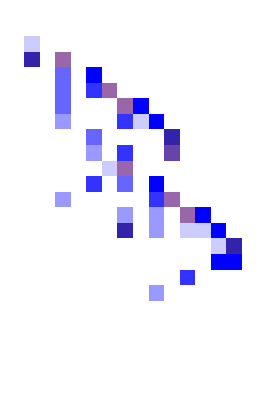
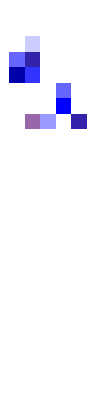
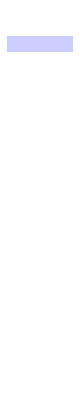
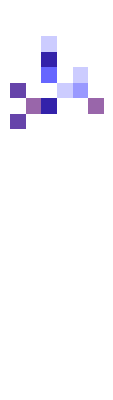
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{colrules =Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]},  ArrayPlot[CellularAutomaton[#, {{1}, 0}, 20], ColorRules->colrules]&/@ evos[[All,1]]]
```

```mathematica
evos2=
ParallelTable[SeedRandom[111211+i];
Nest[CompoundExpression[
ru=RandomRuleMutation[First[#], 1],
life={{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru,{{1}, 0}, 20]],
If[life>=Last[#],{ru,life},#]
]&,{{FromDigits[ReplacePart[Table[0, 10^5], Thread[RandomInteger[{1, 10^5 - 1}, 10000]->RandomInteger[{1, 10}, 10000]]], 10], 10, 2},0},100], {i, 5}];
```

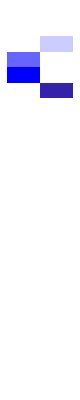
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{colrules =Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]},  ArrayPlot[CellularAutomaton[#, {{1}, 0}, 20], ColorRules->colrules]&/@ evos2[[All,1]]]
```

### v4

```mathematica
evos=
ParallelTable[SeedRandom[111511+i];
Nest[CompoundExpression[
ru=RandomRuleMutation[First[#], 1000],
life={{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru,{{1}, 0}, 40]],
If[life>=Last[#],{ru,life},#]
]&,{{FromDigits[ReplacePart[Table[0, 10^5], Thread[RandomInteger[{1, 10^5 - 1}, 10000]->RandomInteger[{1, 10}, 10000]]], 10], 10, 2},0},200], {i, 10}];
```

```mathematica
With[{colrules =Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]},  ArrayPlot[CellularAutomaton[#, {{1}, 0}, 40], ColorRules->colrules]&/@ evos[[All,1]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram[ParallelTable[SeedRandom[432112 + i];{{"[◼]", "TestCALifeTime"}}[CellularAutomaton[RandomRuleMutation[evos[[1, 1]]], {{1}, 0}, 40]],{i,  10000}], {1}]
```

-Graphics-

```mathematica
aps = {{"[◼]", "allperts"}}[ResourceFunction["PerturbedCellularAutomaton"][evos[[1, 1]], {{1}, 0}, 200][[1]], 10];
```

```mathematica
Length[aps]
```

44802

```mathematica
ByteCount[aps]
```

14336720

```mathematica
With[{colrules =Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]},  Table[{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][evos[[1, 1]], {{1}, 0}, {500, {-100, 100}}],ColorRules->colrules], 10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{colrules =Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]},  SeedRandom[222222];Histogram[ParallelMap[{{"[◼]", "TestCALifeTime"}}[ResourceFunction["PerturbedCellularAutomaton"][evos[[1, 1]], {{1}, 0}, {400, {-100, 100}}, #]]&, RandomSample[aps, 2000]]/.-Infinity->410, PlotRange->All]]
```

-Graphics-

```mathematica
With[{colrules =Thread[Table[i, {i,0, 10}]->Most@*Catenate@Transpose[Table[{Blend[{White, Blue}, i],Blend[{Darker[Blue], Lighter[Pink]}, i]},{i, 0,1, .2}]]]},  SeedRandom[222222];Histogram[ParallelMap[{{"[◼]", "TestCALifeTime"}}[ResourceFunction["PerturbedCellularAutomaton"][evos[[1, 1]], {{1}, 0}, 400, #]]&, RandomSample[aps, 10000]]]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[RandomRuleMutation[evos[[1, 1]]], {{1}, 0}, 40]]
```

-Graphics-